```mathematica
Quit[]
```

```mathematica
datadir="~/Dropbox/heavy_quark_binding_BA/data/";
```

```mathematica
plotdir="~/Dropbox/heavy_quark_binding_BA/plots/";
```

## Functions

```mathematica
LSPolyFit=Function[{X,Y,CovInv,nλ},
Block[{f,T,H,Δ,λ,δλ,χsq,χsqdof,dof,CL},
f[t_,λ_]:=Sum[λ[[a+1]]X[[t]]^a,{a,0,nλ-1}];
T=Length[X];
H=2Table[Table[Sum[Sum[X[[t]]^a X[[tp]]^b CovInv[[t,tp]],{t,1,T}],{tp,1,T}],{a,0,nλ-1}],{b,0,nλ-1}];
Δ=2Inverse[H];
λ=Sum[Δ[[All,b+1]]Sum[X[[t]]^b Y[[t]]Sum[CovInv[[t,tp]],{tp,1,T}],{t,1,T}],{b,0,nλ-1}];
δλ=Sqrt[Diagonal[Δ]];
χsq=Sum[(Y[[t]]-f[t,λ])CovInv[[t,tp]](Y[[tp]]-f[tp,λ]),{t,1,T},{tp,1,T}];
dof=(T-nλ);
(*χsqdof=χsq/dof;*)
(*CL=NIntegrate[(χ2)^(dof/2-1)Exp[-χ2/2],{χ2,χsq,∞}]/NIntegrate[(χ2)^(dof/2-1)Exp[-χ2/2],{χ2,0,∞}];*)
{λ,δλ,χsq/dof}]];
```

```mathematica
LSPolyFitFixed=Function[{X,Y0,CovInv,nλ,fixed},
Block[{f,T,H,Δ,λ,δλ,χsq,χsqdof,dof,CL,nfixed,Y},
T=Length[X];
nfixed=Length[fixed];
Y=Y0-Table[Sum[fixed[[a+1]]X[[t]]^a,{a,0,nfixed-1}],{t,1,T}];
f[t_,λ_]:=Sum[λ[[a+1-nfixed]]X[[t]]^a,{a,nfixed,nλ-1}];
H=2Table[Table[Sum[Sum[X[[t]]^a X[[tp]]^b CovInv[[t,tp]],{t,1,T}],{tp,1,T}],{a,nfixed,nλ-1}],{b,nfixed,nλ-1}];
Δ=2Inverse[H];
λ=Sum[Δ[[All,b+1-nfixed]]Sum[X[[t]]^b Y[[t]]Sum[CovInv[[t,tp]],{tp,1,T}],{t,1,T}],{b,nfixed,nλ-1}];
δλ=Sqrt[Diagonal[Δ]];
χsq=Sum[(Y[[t]]-f[t,λ])CovInv[[t,tp]](Y[[tp]]-f[tp,λ]),{t,1,T},{tp,1,T}];
dof=(T-nλ+nfixed);
(*χsqdof=χsq/dof;*)
(*CL=NIntegrate[(χ2)^(dof/2-1)Exp[-χ2/2],{χ2,χsq,∞}]/NIntegrate[(χ2)^(dof/2-1)Exp[-χ2/2],{χ2,0,∞}];*)
{Join[fixed,λ],Join[0fixed,δλ],χsq/dof}]];
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
(* 3 body potential cross-check *)
```

```mathematica
v3[r1_,r2_]:=Block[{A,R,Rhat,I1,I2,r1hat,r2hat},
R[x_,y_]:=Sqrt[(x r1-y r2).(x r1-y r2)];
Rhat[x_,y_]:=(x r1-y r2)/R[x,y];
A[x_,y_]:=Sqrt[r1.r1]Sqrt[x(1-x)]+Sqrt[r2.r2]Sqrt[y(1-y)];
r1hat=r1/Sqrt[r1.r1];
r2hat=r2/Sqrt[r2.r2];
I1[x_,y_]:=r1hat.r2hat/R[x,y]((1-A[x,y]^2/R[x,y]^2)ArcTan[R[x,y]/A[x,y]]+A[x,y]/R[x,y]);
I2[x_,y_]:=(r1hat.Rhat[x,y])(r2hat.Rhat[x,y])/R[x,y]((1+3A[x,y]^2/R[x,y]^2)ArcTan[R[x,y]/A[x,y]]-3A[x,y]/R[x,y]);
16π NIntegrate[I1[x,y]+I2[x,y],{x,0,1},{y,0,1}]
];
```

```mathematica
v3[{1,2,3},{4,5,18}]
```

6.51269

```mathematica
v3Tab=Table[{r,v3[{r,0,0},{r,0,0}]},{r,0.5,10,.1}];
```

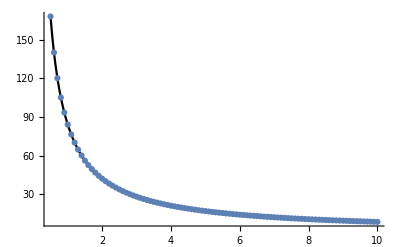

```mathematica
Show[Plot[-4π^2(π^2-12)/r,{r,0.5,10},PlotStyle->Black,PlotRange->All],ListPlot[v3Tab]]
```

## QCD

```mathematica
dtau=0.4;
```

```mathematica
NWalkers=5000;
```

### α

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
Clear[ΛQCD];
Clear[LQ];
Clear[αsNf];
Clear[Mαs];
Clear[αs];
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

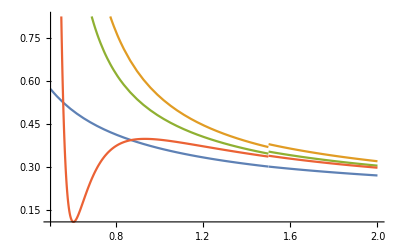

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

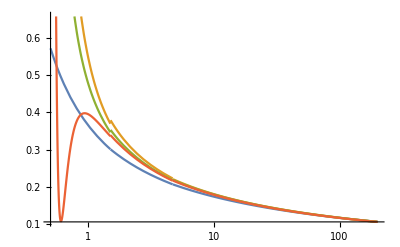

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
Nf4α1LoopMid=Table[αs1Loop[Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopStepTab=Round[4/(.2 Nf4α1LoopMid^2)]
```

{430,411,390,367,342,314,282,245}

```mathematica
Nf4α1LoopBig=Table[αs1Loop[1/2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.268835,0.276665,0.28589,0.296997,0.311546,0.330832,0.357283,0.396841}

```mathematica
Nf4α1LoopSmall=Table[αs1Loop[2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.181799,0.185058,0.188807,0.193197,0.198453,0.204935,0.213849,0.226354}

```mathematica
Length[DeleteDuplicates[Join[Nf4α1LoopMid,Nf4α1LoopBig,Nf4α1LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α1Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.1266,72.9651,62.6156,52.0329,41.1465,29.8326,17.822,4.05254}

```mathematica
Mt
```

173.34

```mathematica
Nf5α1LoopMid=Table[αs1Loop[Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopStepTab=Round[4/(.2 Nf5α1LoopMid^2)]
```

{1391,1339,1278,1207,1120,1006,835,430}

```mathematica
Nf5α1LoopBig=Table[αs1Loop[1/2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.133418,0.136311,0.13987,0.144434,0.150667,0.160132,0.178055,0.268835}

```mathematica
Nf5α1LoopSmall=Table[αs1Loop[2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.108852,0.11077,0.113109,0.116075,0.120067,0.126002,0.136841,0.181799}

```mathematica
Length[DeleteDuplicates[Join[Nf5α1LoopMid,Nf5α1LoopBig,Nf5α1LoopSmall]]]
```

24

```mathematica
Nf4α1LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α1LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α2Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α2LoopMid=Table[αs2Loop[Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopStepTab=Round[4/(.2 Nf4α2LoopMid^2)]
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf4α2LoopBig=Table[αs2Loop[1/2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall=Table[αs2Loop[2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.223621,0.238097}

```mathematica
Nf4α2LoopSmall[[-2]]=0.22362;
```

```mathematica
Length[DeleteDuplicates[Join[Nf4α2LoopMid,Nf4α2LoopBig,Nf4α2LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α2Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α2Loopμ/Nf5mQTab
```

{0.481523,0.491366,0.50345,0.518914,0.539976,0.571839,0.631796,0.917683}

```mathematica
2Nf5α2Loopμ/Nf5mQTab
```

{0.963046,0.982731,1.0069,1.03783,1.07995,1.14368,1.26359,1.83537}

```mathematica
1/2Nf5α2Loopμ/Nf5mQTab
```

{0.240762,0.245683,0.251725,0.259457,0.269988,0.285919,0.315898,0.458842}

```mathematica
Nf5α2LoopMid=Table[αs2Loop[Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopStepTab=Round[4/(.2 Nf5α2LoopMid^2)]
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α2LoopBig=Table[αs2Loop[1/2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall=Table[αs2Loop[2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Length[DeleteDuplicates[Join[Nf5α2LoopMid,Nf5α2LoopBig,Nf5α2LoopSmall]]]
```

24

```mathematica
Nf4α2LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α2LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NNLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α3Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf4α3LoopMid=Table[αs3Loop[Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopStepTab=Round[4/(.2 Nf4α3LoopMid^2)]
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α3LoopBig=Table[αs3Loop[1/2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall=Table[αs3Loop[2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Length[DeleteDuplicates[Join[Nf4α3LoopMid,Nf4α3LoopBig,Nf4α3LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α3Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α3Loopμ/Nf5mQTab
```

{0.481536,0.491353,0.503401,0.518811,0.539782,0.571469,0.630948,0.902505}

```mathematica
2Nf5α3Loopμ/Nf5mQTab
```

{0.963073,0.982706,1.0068,1.03762,1.07956,1.14294,1.2619,1.80501}

```mathematica
1/2Nf5α3Loopμ/Nf5mQTab
```

{0.240768,0.245677,0.251701,0.259405,0.269891,0.285734,0.315474,0.451253}

```mathematica
Nf5α3LoopMid=Table[αs3Loop[Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopStepTab=Round[4/(.2 Nf5α3LoopMid^2)]
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf5α3LoopBig=Table[αs3Loop[1/2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall=Table[αs3Loop[2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Length[DeleteDuplicates[Join[Nf5α3LoopMid,Nf5α3LoopBig,Nf5α3LoopSmall]]]
```

24

```mathematica
Nf4α3LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α3LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

### M_QQbar

```mathematica
qqbarscale=2;
```

```mathematica
Lmur="0.0";
```

#### LO

```mathematica
Nf4α1LoopMid
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopStepTab
```

{430,411,390,367,342,314,282,245}

```mathematica
Nf4α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err]&&err<10,err,10^(-8)]],{i,1,Length[Nf4α1LoopBig]}]
```

{-0.03212100310,-0.03401934310,-0.03632581910,-0.03920320810,-0.04313818210,-0.04864436110,-0.05673384110,-0.06999234610}

```mathematica
Nf4α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-8)]],{i,1,Length[Nf4α1LoopMid]}]
```

{-0.02065160610,-0.02162193810,-0.02277885910,-0.02419041010,-0.02596416610,-0.02828339110,-0.03148921210,-0.03631133510}

```mathematica
Nf4α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-8)]],{i,1,Length[Nf4α1LoopSmall]}]
```

{-0.01468927810,-0.01522065010,-0.01584359310,-0.01658892510,-0.01750381910,-0.01866593510,-0.02032506410,-0.02277161510}

```mathematica
Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.4444425622,-0.4444462021,-0.4444462320,-0.4444462118,-0.4444444517,-0.4444457616,-0.4444442214,-0.4444452512}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

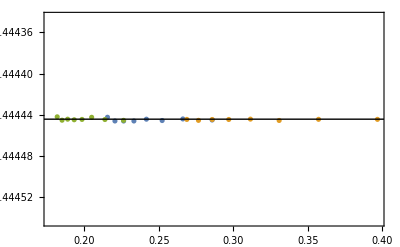

```mathematica
EqqbarNf4α1LoopPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqbarMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqbarBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqbarSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,3}],{MaTeX["\\mu=\\mu_p",Magnification->0.8],MaTeX["\\mu=\\mu_p/2",Magnification->0.8],MaTeX["\\mu=2\\mu_p",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][1]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
Nf4α1LoopBig
```

{0.268835,0.276665,0.28589,0.296997,0.311546,0.330832,0.357283,0.396841}

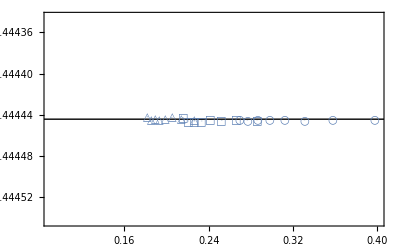

```mathematica
EqqbarNf4α1LoopPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqbarMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqbarBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqbarSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{.09,.4},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1]},PlotStyle->{ColorData[97][1]}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

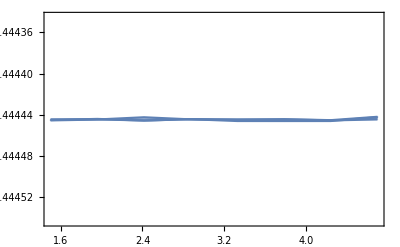

```mathematica
Nf4α1LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

```mathematica
Nf5α1LoopMid
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-8)]],{i,1,Length[Nf5α1LoopBig]}]
```

{-0.00791127210,-0.00825808410,-0.00869494110,-0.00927163610,-0.01008913110,-0.01139655910,-0.01409048110,-0.03212100310}

```mathematica
Nf5α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-8)]],{i,1,Length[Nf5α1LoopMid]}]
```

{-0.00638827210,-0.00663909910,-0.00695266910,-0.00736289810,-0.00793726610,-0.00884001110,-0.01064349910,-0.02065160610}

```mathematica
Nf5α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-8)]],{i,1,Length[Nf5α1LoopSmall]}]
```

{-0.00526611510,-0.00545333010,-0.00568606510,-0.00598818010,-0.00640714910,-0.00705622410,-0.00832242610,-0.01468927810}

```mathematica
Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.44444787,-0.44444647,-0.44444486,-0.44444716,-0.44444286,-0.44444685,-0.44444584,-0.4444425622}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

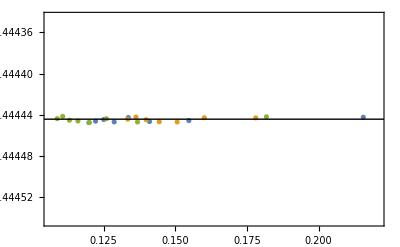

```mathematica
EqqbarNf5α1LoopPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqbarMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqbarBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqbarSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

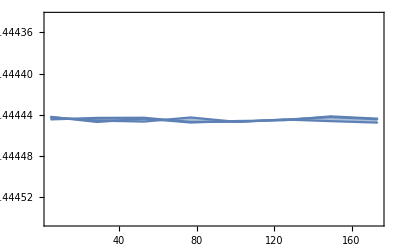

```mathematica
Nf5α1LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

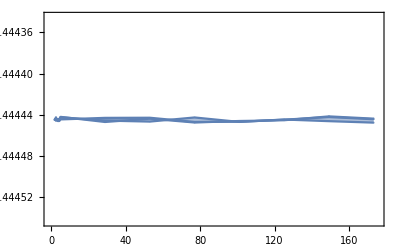

```mathematica
Show[Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mt+2},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}}]
```

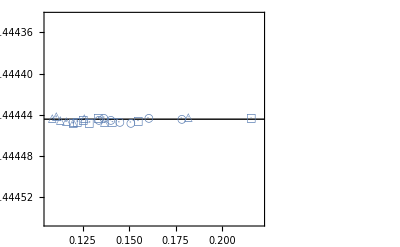

```mathematica
EqqbarNf5α1LoopPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqbarMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqbarBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqbarSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1]},PlotStyle->{ColorData[97][1]}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Eqqbarα1LoopPlot=Show[EqqbarNf4α1LoopPlot,EqqbarNf5α1LoopPlot,PlotRange->{{.095,.41},{ΔEqqbarOα2Exact-.0002,ΔEqqbarOα2Exact+.0002}},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_alpha_LO.pdf",Eqqbarα1LoopPlot];
```

#### NLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.094200.00007,-0.103570.00007,-0.115760.00010,-0.132790.00014,-0.156080.00013,-0.18490.0005,-0.25290.0004,-0.41180.0012}

```mathematica
Nf4α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.062200.00009,-0.066890.00011,-0.072510.00011,-0.079620.00010,-0.089660.00013,-0.103470.00017,-0.123740.00018,-0.159340.00034}

```mathematica
Nf4α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.045670.00014,-0.048050.00013,-0.051040.00011,-0.054680.00013,-0.059160.00021,-0.066060.00034,-0.076020.00028,-0.091780.00026}

```mathematica
Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.18170.0018,-1.20370.0020,-1.22640.0018,-1.25300.0016,-1.29510.0019,-1.34590.0023,-1.40830.0021,-1.51340.0032}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf4α2LoopΔEqqbarBig/Nf4α2LoopBig^2
```

{-0.99670.0007,-1.01290.0007,-1.03310.0009,-1.06280.0011,-1.09340.0009,-1.13230.0029,-1.18900.0017,-1.2900.004}

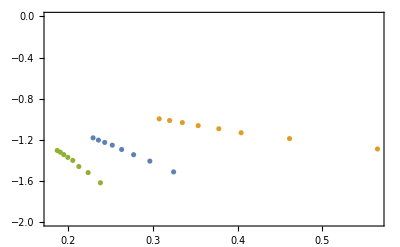

```mathematica
EqqbarNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

```mathematica
αLegendNLO=PointLegend[Table[Directive[ColorData[97][2]],{ii,3}],{MaTeX["\\mu=\\mu_p",Magnification->0.8],MaTeX["\\mu=\\mu_p/2",Magnification->0.8],MaTeX["\\mu=2\\mu_p",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][2]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

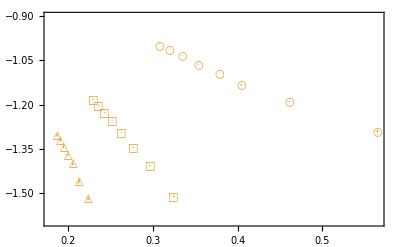

```mathematica
EqqbarNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-1.6,-.9},PlotLegends->Placed[αLegendNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

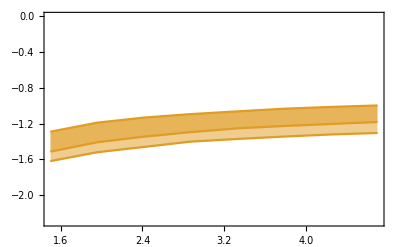

```mathematica
Nf4α2LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.3,0}},Joined->True,Filling->{True},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

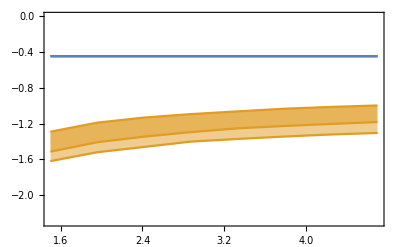

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot]
```

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopBig
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopBig
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.22362,0.238097}

```mathematica
Nf5α2Loopμ
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Nf4α2Loopμ
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf4α2LoopStepTab
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf5α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.0124536,-0.0131490.000012,-0.0140067,-0.0151786,-0.0169039,-0.0197660.000012,-0.0261270.000017,-0.088230.00008}

```mathematica
-0.088274081
```

-0.0882741

```mathematica
Nf5α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.0112280.000014,-0.0118050.000015,-0.0125130.000018,-0.0135080.000012,-0.0149100.000018,-0.0171750.000012,-0.0221090.000025,-0.058010.00008}

```mathematica
Nf5α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.0100860.000017,-0.0105830.000014,-0.0111470.000015,-0.0119340.000025,-0.0130930.000024,-0.0149100.000025,-0.018710.00004,-0.042480.00009}

```mathematica
Nf4α2LoopΔEqqbarBig
```

{-0.094200.00007,-0.103570.00007,-0.115760.00010,-0.132790.00014,-0.156080.00013,-0.18490.0005,-0.25290.0004,-0.41180.0012}

```mathematica
Nf4α2LoopΔEqqbarMid
```

{-0.062200.00009,-0.066890.00011,-0.072510.00011,-0.079620.00010,-0.089660.00013,-0.103470.00017,-0.123740.00018,-0.159340.00034}

```mathematica
Nf4α2LoopΔEqqbarSmall
```

{-0.045670.00014,-0.048050.00013,-0.051040.00011,-0.054680.00013,-0.059160.00021,-0.066060.00034,-0.076020.00028,-0.091780.00026}

```mathematica
Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.77480.0010,-0.78230.0010,-0.78990.0012,-0.80260.0007,-0.81820.0010,-0.84040.0006,-0.88620.0010,-1.10210.0015}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf5α2LoopΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.684340.00034,-0.69030.0006,-0.69580.0004,-0.703750.00030,-0.71540.0004,-0.73270.0004,-0.76610.0005,-0.93350.0008}

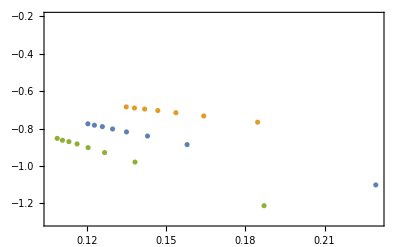

```mathematica
EqqbarNf5α2LoopPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.3,-.2}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

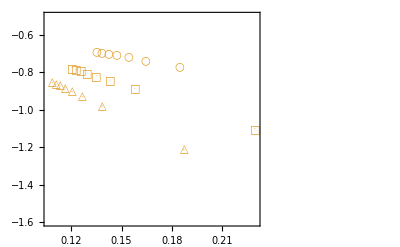

```mathematica
EqqbarNf5α2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.6,-.5},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

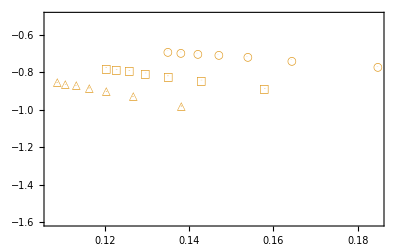

```mathematica
EqqbarNf5α2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]-1}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]-1}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]-1}]},PlotRange->{-1.6,-.5},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopΔEqqbarMid
```

{-0.0112280.000014,-0.0118050.000015,-0.0125130.000018,-0.0135080.000012,-0.0149100.000018,-0.0171750.000012,-0.0221090.000025,-0.058010.00008}

```mathematica
LSPolyFit[Nf5α2LoopMid,Nf5α2LoopΔEqqbarMid[[All,1]],DiagonalMatrix[Nf5α2LoopΔEqqbarMid[[All,2]]^2],2]
```

{{0.0460256,-0.452933},{58920.4,279396.},1.82352×10^-15}

```mathematica
fitPt=4;
```

```mathematica
ΔEqqbarOα2Exact
```

-0.444444

```mathematica
Nf5α1LoopΔEqqbarMid
```

{-0.00638827210,-0.00663909910,-0.00695266910,-0.00736289810,-0.00793726610,-0.00884001110,-0.01064349910,-0.02065160610}

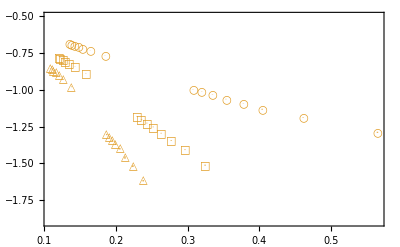

```mathematica
Eqqbarα2LoopPlot=Show[EqqbarNf4α2LoopPlot,EqqbarNf5α2LoopPlot,PlotRange->{All,{-1.9,-.5}},Axes->False]
```

```mathematica
markerlist
```

{□,○,△,▽,◇,▯,◦}

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_alpha_NLO.pdf",Eqqbarα2LoopPlot];
```

```mathematica
Nf5α2LoopΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.684340.00034,-0.69030.0006,-0.69580.0004,-0.703750.00030,-0.71540.0004,-0.73270.0004,-0.76610.0005,-0.93350.0008}

```mathematica
Nf5α2LoopΔEqqbarSmall/Nf5α2LoopSmall^2
```

{-0.85280.0014,-0.86290.0011,-0.87020.0011,-0.88270.0019,-0.90230.0017,-0.92880.0016,-0.97960.0020,-1.21330.0026}

```mathematica
Nf5α2LoopΔEqqbarSmall[[-2]]
```

-0.018710.00004

```mathematica
Nf5α2LoopSmall[[-2]]
```

0.138215

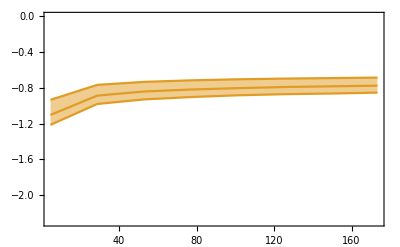

```mathematica
Nf5α2LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.3,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

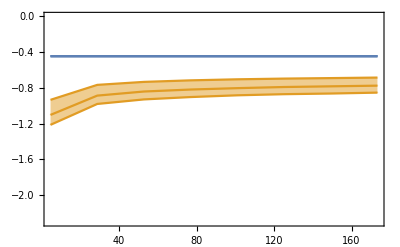

```mathematica
Show[Nf5α2LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot]
```

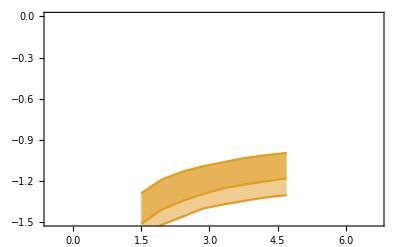

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mb+2},{-1.5,0}}]
```

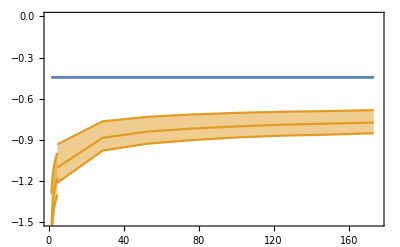

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{2Mc-2,Mt+2},{-1.5,0}}]
```

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopMid[[1;;fitPt]],Nf5α2LoopΔEqqbarMid[[1;;fitPt,1]]/Nf5α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqbarMid[[1;;fitPt,2]]/Nf5α2LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.413391,-2.99538},{0.00197367,0.0139924},1.41349}

```mathematica
Nf5α2LoopΔEqqbarFitMid=LSPolyFitFixed[Nf5α2LoopMid[[1;;fitPt]],Nf5α2LoopΔEqqbarMid[[1;;fitPt,1]]/Nf5α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqbarMid[[1;;fitPt,2]]/Nf5α2LoopMid[[1;;fitPt]]^2)^-2],2,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-2.77798},{0.,0.00220512},36.5766}

```mathematica
fitPt=7;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopBig[[1;;fitPt]],Nf5α2LoopΔEqqbarBig[[1;;fitPt,1]]/Nf5α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqbarBig[[1;;fitPt,2]]/Nf5α2LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.462783,-1.64258},{0.0015707,0.0104496},0.474802}

```mathematica
Nf5α2LoopΔEqqbarFitBig=LSPolyFitFixed[Nf5α2LoopBig[[1;;fitPt]],Nf5α2LoopΔEqqbarBig[[1;;fitPt,1]]/Nf5α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqbarBig[[1;;fitPt,2]]/Nf5α2LoopBig[[1;;fitPt]]^2)^-2],2,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-1.76406},{0.,0.000967153},23.1138}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopSmall[[1;;fitPt]],Nf5α2LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf5α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf5α2LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.356122,-4.5478},{0.00390863,0.0323962},5.02954}

```mathematica
Nf5α2LoopΔEqqbarFitSmall=LSPolyFitFixed[Nf5α2LoopSmall[[1;;fitPt]],Nf5α2LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf5α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf5α2LoopSmall[[1;;fitPt]]^2)^-2],2,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-3.82258},{0.,0.00441563},77.2568}

```mathematica
Around[Nf5α2LoopΔEqqbarFitMid[[1,2]],Nf5α2LoopΔEqqbarFitMid[[2,2]]]
```

-2.77800.0022

```mathematica
Abs[Nf5α2LoopΔEqqbarFitSmall[[1,2]]-Nf5α2LoopΔEqqbarFitBig[[1,2]]]/2
```

1.02926

```mathematica
Around[Nf5α2LoopΔEqqbarFitMid[[1,2]],Abs[Nf5α2LoopΔEqqbarFitSmall[[1,2]]-Nf5α2LoopΔEqqbarFitBig[[1,2]]]/2]
```

-2.81.0

```mathematica
Around[Nf5α2LoopΔEqqbarFitMid[[1,2]],Nf5α2LoopΔEqqbarFitMid[[2,2]]]/-ΔEqqbarOα2Exact
```

-6.2500.005

```mathematica
Around[Nf5α2LoopΔEqqbarFitMid[[1,2]],Abs[Nf5α2LoopΔEqqbarFitSmall[[1,2]]-Nf5α2LoopΔEqqbarFitBig[[1,2]]]/2]/-ΔEqqbarOα2Exact
```

-6.32.3

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],Nf4α2LoopΔEqqbarMid[[1;;fitPt,1]]/Nf4α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqbarMid[[1;;fitPt,2]]/Nf4α2LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.38787,-3.44941},{0.00711593,0.0275168},2.83505}

```mathematica
LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],Nf4α2LoopΔEqqbarMid[[1;;fitPt,1]]/Nf4α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqbarMid[[1;;fitPt,2]]/Nf4α2LoopMid[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.586112,-1.96567,-2.74597},{0.0696558,0.519335,0.959794},1.76499}

```mathematica
Nf4α2LoopΔEqqbarFitMid=LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],Nf4α2LoopΔEqqbarMid[[1;;fitPt,1]]/Nf4α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqbarMid[[1;;fitPt,2]]/Nf4α2LoopMid[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-3.0206,-0.80413},{0.,0.0258754,0.098051},2.16024}

```mathematica
fitPt=8;
```

```mathematica
Nf4α2LoopΔEqqbarFitBig=LSPolyFitFixed[Nf4α2LoopBig[[1;;fitPt]],Nf4α2LoopΔEqqbarBig[[1;;fitPt,1]]/Nf4α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqbarBig[[1;;fitPt,2]]/Nf4α2LoopBig[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.416203,-2.29377,1.32927},{0.015593,0.0812723,0.103738},3.53989}

```mathematica
Nf4α2LoopΔEqqbarFitBig=LSPolyFitFixed[Nf4α2LoopBig[[1;;fitPt]],Nf4α2LoopΔEqqbarBig[[1;;fitPt,1]]/Nf4α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqbarBig[[1;;fitPt,2]]/Nf4α2LoopBig[[1;;fitPt]]^2)^-2],2,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-1.74285},{0.,0.0010364},504.639}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α2LoopSmall[[1;;fitPt]],Nf4α2LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf4α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf4α2LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.137409,-6.19924},{0.0193738,0.0958579},1.84553}

```mathematica
Nf4α2LoopΔEqqbarFitSmall=LSPolyFitFixed[Nf4α2LoopSmall[[1;;fitPt]],Nf4α2LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf4α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf4α2LoopSmall[[1;;fitPt]]^2)^-2],2,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-4.68415},{0.,0.00700412},37.4618}

```mathematica
Around[Nf4α2LoopΔEqqbarFitMid[[1,2]],Nf4α2LoopΔEqqbarFitMid[[2,2]]]
```

-3.0210.026

```mathematica
Abs[Nf4α2LoopΔEqqbarFitSmall[[1,2]]-Nf4α2LoopΔEqqbarFitBig[[1,2]]]/2
```

1.47065

```mathematica
Around[Nf4α2LoopΔEqqbarFitMid[[1,2]],Abs[Nf4α2LoopΔEqqbarFitSmall[[1,2]]-Nf4α2LoopΔEqqbarFitBig[[1,2]]]/2]
```

-3.01.5

```mathematica
Around[Nf4α2LoopΔEqqbarFitMid[[1,2]],Nf4α2LoopΔEqqbarFitMid[[2,2]]]/-ΔEqqbarOα2Exact
```

-6.800.06

```mathematica
Around[Nf4α2LoopΔEqqbarFitMid[[1,2]],Abs[Nf4α2LoopΔEqqbarFitSmall[[1,2]]-Nf4α2LoopΔEqqbarFitBig[[1,2]]]/2]/-ΔEqqbarOα2Exact
```

-6.83.3

#### mNLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.11740.0017,-0.12750.0019,-0.14830.0020,-0.17220.0025,-0.21130.0025,-0.2600.004,-0.3810.006,-0.6410.009}

```mathematica
Nf4α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.06360.0010,-0.06760.0011,-0.07540.0010,-0.08530.0015,-0.09580.0013,-0.10890.0020,-0.13250.0021,-0.17220.0034}

```mathematica
Nf4α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.04150.0006,-0.04450.0007,-0.04900.0009,-0.05410.0010,-0.05790.0010,-0.06360.0017,-0.07180.0013,-0.08350.0015}

```mathematica
Nf4α2LoopmΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.2080.019,-1.2170.019,-1.2750.016,-1.3420.023,-1.3840.019,-1.4160.026,-1.5080.023,-1.6360.032}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf4α2LoopmΔEqqbarBig/Nf4α2LoopBig^2
```

{-1.2420.018,-1.2470.018,-1.3230.018,-1.3780.020,-1.4800.018,-1.5950.026,-1.7920.030,-2.0060.027}

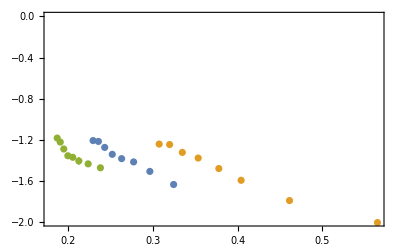

```mathematica
EqqbarNf4α2LoopmPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopmΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopmΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopmΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

```mathematica
αLegendmNLO=PointLegend[Table[Directive[ColorData[97][5]],{ii,3}],{MaTeX["\\mu=\\mu_p",Magnification->0.8],MaTeX["\\mu=\\mu_p/2",Magnification->0.8],MaTeX["\\mu=2\\mu_p",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][5]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

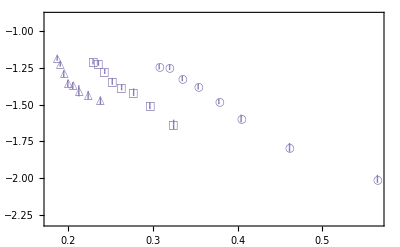

```mathematica
EqqbarNf4α2LoopmPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopmΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopmΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopmΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2.3,-.9},PlotLegends->Placed[αLegendmNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][5]},PlotStyle->{ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

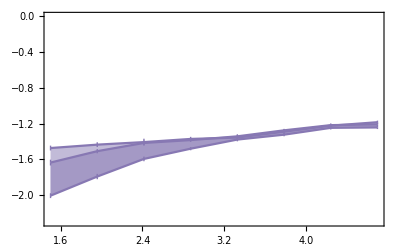

```mathematica
Nf4α2LoopmΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.3,0}},Joined->True,Filling->{True},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

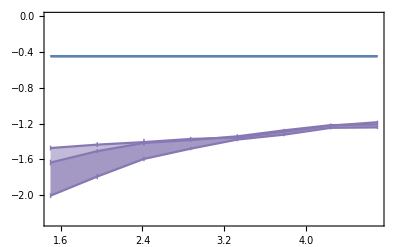

```mathematica
Show[Nf4α2LoopmΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot]
```

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopBig
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopBig
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.22362,0.238097}

```mathematica
Nf5α2Loopμ
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Nf4α2Loopμ
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf4α2LoopStepTab
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf5α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.013210.00008,-0.013880.00010,-0.015040.00011,-0.016290.00013,-0.018410.00013,-0.021260.00014,-0.029200.00026,-0.11210.0016}

```mathematica
Nf5α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.011480.00012,-0.012060.00013,-0.012650.00023,-0.013770.00014,-0.015400.00014,-0.017190.00014,-0.023090.00023,-0.06050.0009}

```mathematica
Nf5α1LoopΔEqqbarMid[[-1]]-Nf4α1LoopΔEqqbarMid[[1]]
```

0.01.410^-8

```mathematica
Nf5α2LoopΔEqqbarMid[[-1]]-Nf4α2LoopΔEqqbarMid[[1]]
```

0.00320.0009

```mathematica
Nf5α2LoopmΔEqqbarMid[[-1]]-Nf4α2LoopmΔEqqbarMid[[1]]
```

0.00310.0014

```mathematica
Nf5α3LoopΔEqqbarMid[[-1]]-Nf4α3LoopΔEqqbarMid[[1]]
```

0.01020.0012

```mathematica
Nf5α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.009640.00010,-0.010280.00012,-0.011100.00014,-0.011610.00012,-0.012890.00013,-0.014620.00014,-0.018030.00022,-0.03940.0006}

```mathematica
Nf4α2LoopmΔEqqbarBig
```

{-0.11740.0017,-0.12750.0019,-0.14830.0020,-0.17220.0025,-0.21130.0025,-0.2600.004,-0.3810.006,-0.6410.009}

```mathematica
Nf4α2LoopmΔEqqbarMid
```

{-0.06360.0010,-0.06760.0011,-0.07540.0010,-0.08530.0015,-0.09580.0013,-0.10890.0020,-0.13250.0021,-0.17220.0034}

```mathematica
Nf4α2LoopmΔEqqbarSmall
```

{-0.04150.0006,-0.04450.0007,-0.04900.0009,-0.05410.0010,-0.05790.0010,-0.06360.0017,-0.07180.0013,-0.08350.0015}

```mathematica
Nf5α2LoopmΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.7920.008,-0.7990.009,-0.7980.015,-0.8180.008,-0.8450.008,-0.8410.007,-0.9260.009,-1.1490.018}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf5α2LoopmΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.7260.004,-0.7290.005,-0.7470.006,-0.7550.006,-0.7790.006,-0.7880.005,-0.8560.008,-1.1860.017}

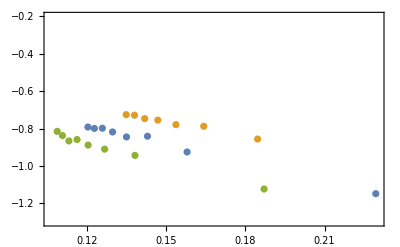

```mathematica
EqqbarNf5α2LoopmPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopMid[[i]],Nf5α2LoopmΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopBig[[i]],Nf5α2LoopmΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopmΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.3,-.2}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

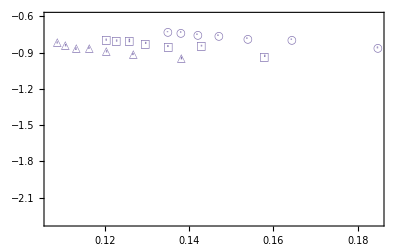

```mathematica
EqqbarNf5α2LoopmPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopmΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]-1}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopmΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]-1}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopmΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]-1}]},PlotRange->{-2.3,-.6},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][5]},PlotStyle->{ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

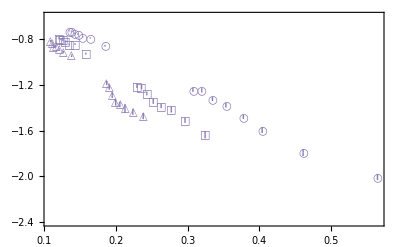

```mathematica
Eqqbarα2LoopmPlot=Show[EqqbarNf5α2LoopmPlot,EqqbarNf4α2LoopmPlot,PlotRange->{All,{-2.4,-.6}}]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_alpha_mNLO.pdf",Eqqbarα2LoopmPlot];
```

```mathematica
Nf5α2LoopmΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.7260.004,-0.7290.005,-0.7470.006,-0.7550.006,-0.7790.006,-0.7880.005,-0.8560.008,-1.1860.017}

```mathematica
Nf5α2LoopmΔEqqbarSmall/Nf5α2LoopSmall^2
```

{-0.8150.008,-0.8380.009,-0.8660.011,-0.8590.009,-0.8890.009,-0.9100.009,-0.9440.011,-1.1240.016}

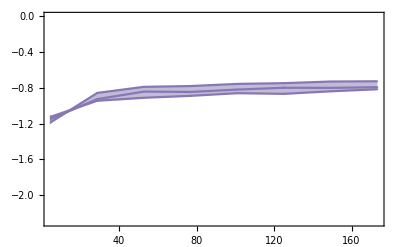

```mathematica
Nf5α2LoopmΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.3,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

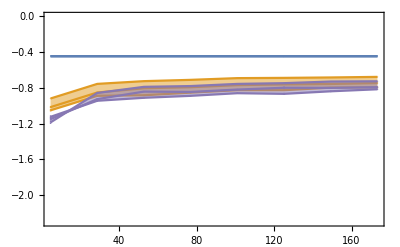

```mathematica
Show[Nf5α2LoopΔEqqbarPlot,Nf5α2LoopmΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot]
```

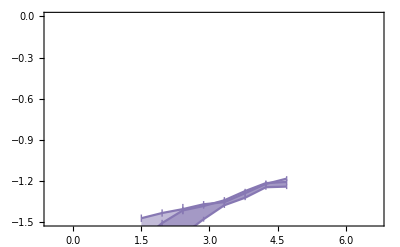

```mathematica
Show[Nf4α2LoopmΔEqqbarPlot,PlotRange->{{Mc-2,Mb+2},{-1.5,0}}]
```

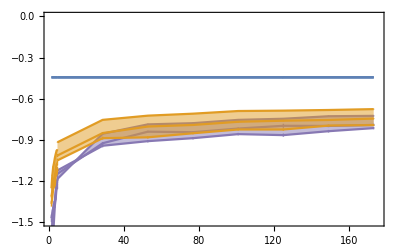

```mathematica
Show[Nf4α2LoopmΔEqqbarPlot,Nf5α2LoopmΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{2Mc-2,Mt+2},{-1.5,0}}]
```

#### NNLO

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.157970.00017,-0.176750.00015,-0.200590.00019,-0.23670.0013,-0.28680.0030,-0.37870.0014,-0.56910.0030,-1.0350.012}

```mathematica
Nf4α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.105930.00009,-0.115420.00010,-0.127370.00011,-0.143380.00015,-0.165250.00026,-0.195680.00017,-0.244500.00024,-0.330000.00033}

```mathematica
Nf4α3LoopSmall
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Nf4α3LoopStepTab
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.082430.00016,-0.088490.00027,-0.095540.00021,-0.103870.00021,-0.115740.00029,-0.13160.0004,-0.15290.0004,-0.19450.0007}

```mathematica
Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-2.08080.0018,-2.15200.0018,-2.23770.0020,-2.35100.0024,-2.4970.004,-2.67670.0024,-2.94780.0028,-3.35710.0033}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf4α3LoopΔEqqbarBig/Nf4α3LoopBig^2
```

{-1.80190.0020,-1.87640.0016,-1.95960.0019,-2.0960.012,-2.3450.025,-2.6170.009,-3.1260.017,-4.010.05}

```mathematica
αLegendNNLO=PointLegend[Table[Directive[ColorData[97][3]],{ii,3}],{MaTeX["\\mu=\\mu_p",Magnification->0.8],MaTeX["\\mu=\\mu_p/2",Magnification->0.8],MaTeX["\\mu=2\\mu_p",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

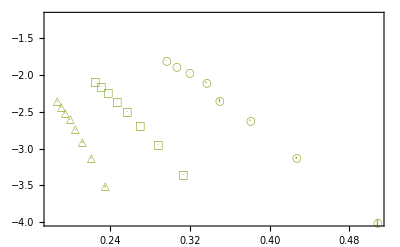

```mathematica
EqqbarNf4α3LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqbarMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqbarBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqbarSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-4,-1.2},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

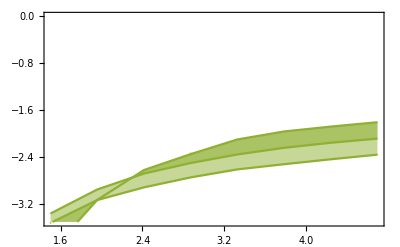

```mathematica
Nf4α3LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-3.5,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

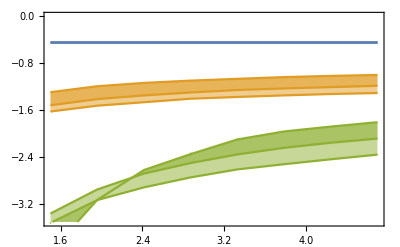

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,PlotRange->{-3.5,0}]
```

```mathematica
Nf5α3LoopMid
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopBig
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopBig
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Nf5α3Loopμ
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Nf4α3Loopμ
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf4α3LoopStepTab
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf5α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0150766,-0.0160128,-0.0172224,-0.0188760.000013,-0.0212954,-0.0254510.000019,-0.0349890.000012,-0.139240.00025}

```mathematica
Nf5α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.0140410.000015,-0.0148870.000014,-0.0159000.000023,-0.0173430.000026,-0.0193920.000024,-0.022870.00004,-0.0305280.000034,-0.092670.00006}

```mathematica
Nf5α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.0130620.000024,-0.0137920.000021,-0.0146760.000027,-0.0158870.000026,-0.0176260.000022,-0.0206600.000030,-0.026890.00005,-0.072040.00013}

```mathematica
Nf4α3LoopΔEqqbarBig
```

{-0.157970.00017,-0.176750.00015,-0.200590.00019,-0.23670.0013,-0.28680.0030,-0.37870.0014,-0.56910.0030,-1.0350.012}

```mathematica
Nf4α3LoopΔEqqbarMid
```

{-0.105930.00009,-0.115420.00010,-0.127370.00011,-0.143380.00015,-0.165250.00026,-0.195680.00017,-0.244500.00024,-0.330000.00033}

```mathematica
Nf4α3LoopΔEqqbarSmall
```

{-0.082430.00016,-0.088490.00027,-0.095540.00021,-0.103870.00021,-0.115740.00029,-0.13160.0004,-0.15290.0004,-0.19450.0007}

```mathematica
Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-0.96890.0010,-0.98660.0009,-1.00390.0014,-1.03090.0016,-1.06490.0013,-1.12050.0018,-1.22700.0014,-1.82040.0011}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf5α3LoopΔEqqbarBig/Nf5α3LoopBig^2
```

{-0.829150.00031,-0.84140.0004,-0.856760.00019,-0.87680.0006,-0.903610.00018,-0.94700.0007,-1.03320.0004,-1.58820.0028}

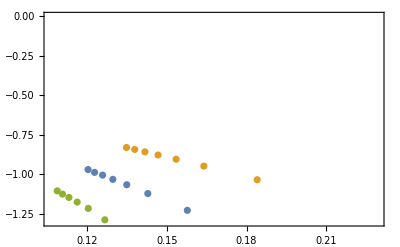

```mathematica
EqqbarNf5α3LoopPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqbarMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqbarBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqbarSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

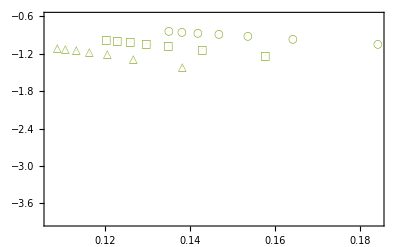

```mathematica
EqqbarNf5α3LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqbarMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]-1}],Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqbarBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]-1}],Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqbarSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]-1}]},PlotRange->{-3.9,-.6},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

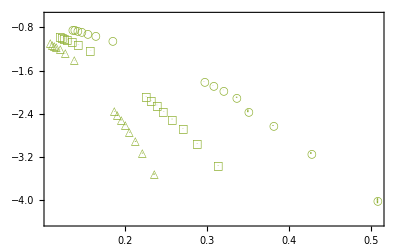

```mathematica
Eqqbarα3LoopPlot=Show[EqqbarNf4α3LoopPlot,EqqbarNf5α3LoopPlot,PlotRange->{All,{-4.4 ,-.6 }},Axes->False]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_alpha_NNLO.pdf",Eqqbarα3LoopPlot];
```

```mathematica
Nf5α3LoopΔEqqbarBig/Nf5α3LoopBig^2
```

{-0.829150.00031,-0.84140.0004,-0.856760.00019,-0.87680.0006,-0.903610.00018,-0.94700.0007,-1.03320.0004,-1.58820.0028}

```mathematica
Nf5α3LoopΔEqqbarSmall/Nf5α3LoopSmall^2
```

{-1.10380.0020,-1.12400.0017,-1.14520.0021,-1.17470.0019,-1.21450.0015,-1.28700.0018,-1.40820.0026,-2.0580.004}

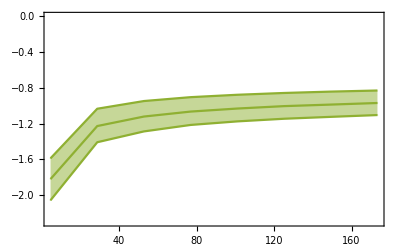

```mathematica
Nf5α3LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.3,0}},Joined->True,Filling->{2->{3}},PlotLegends->Placed[OLegend,{0.5,0.2}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

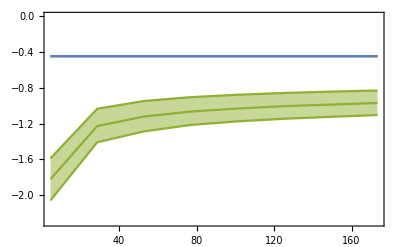

```mathematica
Show[Nf5α3LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot]
```

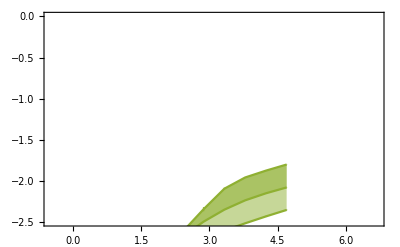

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mb+2},{-2.5,0}}]
```

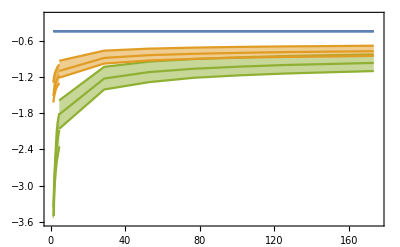

```mathematica
EqqbarNf45α3LoopPlotMQ=Show[Nf4α3LoopΔEqqbarPlot,Nf5α3LoopΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{0,Mt+2},{-3.6,-.2}},Axes->False]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_mQ.pdf",EqqbarNf45α3LoopPlotMQ];
```

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],Nf5α3LoopΔEqqbarMid[[1;;fitPt,1]]/Nf5α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarMid[[1;;fitPt,2]]/Nf5α3LoopMid[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.469897,-2.06174,-17.3907},{0.0151189,0.186387,0.535824},0.878692}

```mathematica
LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],Nf5α3LoopΔEqqbarMid[[1;;fitPt,1]]/Nf5α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarMid[[1;;fitPt,2]]/Nf5α3LoopMid[[1;;fitPt]]^2)^-2],2,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-5.08529},{0.,0.00295627},9144.46}

```mathematica
Nf5α3LoopΔEqqbarFitMid=LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],Nf5α3LoopΔEqqbarMid[[1;;fitPt,1]]/Nf5α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarMid[[1;;fitPt,2]]/Nf5α3LoopMid[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-2.37497,-16.4953},{0.,0.0111136,0.0652014},1.20462}

```mathematica
Nf5α3LoopΔEqqbarFitMid=LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],Nf5α3LoopΔEqqbarMid[[1;;fitPt,1]]/Nf5α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarMid[[1;;fitPt,2]]/Nf5α3LoopMid[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact,Nf5α2LoopΔEqqbarFitMid[[1,2]]}]
```

{{-0.444444,-2.77798,-14.2161},{0.,0.,0.017344},188.885}

```mathematica
Nf5α3LoopΔEqqbarFitMid[[2,2]]=Nf5α2LoopΔEqqbarFitMid[[2,2]];
```

```mathematica
fitPt=7;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],Nf5α3LoopΔEqqbarBig[[1;;fitPt,1]]/Nf5α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarBig[[1;;fitPt,2]]/Nf5α3LoopBig[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.402731,-2.44707,-5.3183},{0.012289,0.155932,0.490809},0.718579}

```mathematica
Nf5α3LoopΔEqqbarFitBig=LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],Nf5α3LoopΔEqqbarBig[[1;;fitPt,1]]/Nf5α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarBig[[1;;fitPt,2]]/Nf5α3LoopBig[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-1.91841,-6.97569},{0.,0.00758246,0.049806},2.8792}

```mathematica
Nf5α3LoopΔEqqbarFitBig=LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],Nf5α3LoopΔEqqbarBig[[1;;fitPt,1]]/Nf5α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarBig[[1;;fitPt,2]]/Nf5α3LoopBig[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact,Nf5α2LoopΔEqqbarFitBig[[1,2]]}]
```

{{-0.444444,-1.76406,-7.98504},{0.,0.,0.00468593},71.4609}

```mathematica
Nf5α3LoopΔEqqbarFitBig[[2,2]]=Nf5α2LoopΔEqqbarFitBig[[2,2]];
```

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],Nf5α3LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf5α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf5α3LoopSmall[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.519686,-1.40707,-36.4139},{0.0336873,0.482302,1.67105},2.33312}

```mathematica
Nf5α3LoopΔEqqbarFitSmall=LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],Nf5α3LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf5α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf5α3LoopSmall[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-2.48143,-32.7336},{0.,0.0352192,0.277981},2.77572}

```mathematica
Nf5α3LoopΔEqqbarFitSmall=LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],Nf5α3LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf5α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf5α3LoopSmall[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact,Nf5α2LoopΔEqqbarFitSmall[[1,2]]}]
```

{{-0.444444,-3.82258,-22.288},{0.,0.,0.0450506},209.536}

```mathematica
Nf5α3LoopΔEqqbarFitSmall[[2,2]]=Nf5α2LoopΔEqqbarFitSmall[[2,2]];
```

```mathematica
Around[Nf5α3LoopΔEqqbarFitMid[[1,2]],Nf5α3LoopΔEqqbarFitMid[[2,2]]]
```

-2.77800.0022

```mathematica
Abs[Nf5α3LoopΔEqqbarFitSmall[[1,2]]-Nf5α3LoopΔEqqbarFitBig[[1,2]]]/2
```

1.02926

```mathematica
Around[Nf5α3LoopΔEqqbarFitMid[[1,2]],Abs[Nf5α3LoopΔEqqbarFitSmall[[1,2]]-Nf5α3LoopΔEqqbarFitBig[[1,2]]]/2]
```

-2.81.0

```mathematica
Around[Nf5α3LoopΔEqqbarFitMid[[1,3]],Nf5α3LoopΔEqqbarFitMid[[2,3]]]
```

-14.2160.017

```mathematica
Abs[Nf5α3LoopΔEqqbarFitSmall[[1,3]]-Nf5α3LoopΔEqqbarFitBig[[1,3]]]/2
```

7.15146

```mathematica
Around[Nf5α3LoopΔEqqbarFitMid[[1,3]],Abs[Nf5α3LoopΔEqqbarFitSmall[[1,3]]-Nf5α3LoopΔEqqbarFitBig[[1,3]]]/2]/-ΔEqqbarOα2Exact
```

-32.16.

```mathematica
Around[Nf5α3LoopΔEqqbarFitMid[[1,3]],Nf5α3LoopΔEqqbarFitMid[[2,3]]]/-ΔEqqbarOα2Exact
```

-31.990.04

```mathematica
Around[Nf5α3LoopΔEqqbarFitMid[[1,3]],Abs[Nf5α3LoopΔEqqbarFitSmall[[1,3]]-Nf5α3LoopΔEqqbarFitBig[[1,3]]]/2]/-ΔEqqbarOα2Exact
```

-32.16.

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α3LoopMid[[1;;fitPt]],Nf4α3LoopΔEqqbarMid[[1;;fitPt,1]]/Nf4α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqbarMid[[1;;fitPt,2]]/Nf4α3LoopMid[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.715122,0.0903119,-27.1872},{0.0898265,0.686963,1.2997},1.81553}

```mathematica
Nf4α3LoopΔEqqbarFitMid=LSPolyFitFixed[Nf4α3LoopMid[[1;;fitPt]],Nf4α3LoopΔEqqbarMid[[1;;fitPt,1]]/Nf4α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqbarMid[[1;;fitPt,2]]/Nf4α3LoopMid[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-1.97773,-23.2871},{0.,0.03028,0.118443},3.02631}

```mathematica
fitPt=8;
```

```mathematica
Nf4α3LoopΔEqqbarFitBig=LSPolyFitFixed[Nf4α3LoopBig[[1;;fitPt]],Nf4α3LoopΔEqqbarBig[[1;;fitPt,1]]/Nf4α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqbarBig[[1;;fitPt,2]]/Nf4α3LoopBig[[1;;fitPt]]^2)^-2],3,{}]
```

{{-2.03733,8.27075,-25.2023},{0.129458,0.759948,1.10992},38.4162}

```mathematica
Nf4α3LoopΔEqqbarFitBig=LSPolyFitFixed[Nf4α3LoopBig[[1;;fitPt]],Nf4α3LoopΔEqqbarBig[[1;;fitPt,1]]/Nf4α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqbarBig[[1;;fitPt,2]]/Nf4α3LoopBig[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact}]
```

{{-0.444444,-1.05355,-11.7319},{0.,0.0569876,0.182737},57.2461}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α3LoopSmall[[1;;fitPt]],Nf4α3LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf4α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf4α3LoopSmall[[1;;fitPt]]^2)^-2],3,{}]
```

{{-2.54261,20.9899,-106.887},{0.547776,5.32347,12.8889},0.946251}

```mathematica
Nf4α3LoopΔEqqbarFitSmall=LSPolyFitFixed[Nf4α3LoopSmall[[1;;fitPt]],Nf4α3LoopΔEqqbarSmall[[1;;fitPt,1]]/Nf4α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqbarSmall[[1;;fitPt,2]]/Nf4α3LoopSmall[[1;;fitPt]]^2)^-2],3,{ΔEqqbarOα2Exact}]
```

{{-0.444444,0.610716,-57.635},{0.,0.17859,0.886824},3.23379}

```mathematica
Around[Nf4α3LoopΔEqqbarFitMid[[1,2]],Nf4α3LoopΔEqqbarFitMid[[2,2]]]
```

-1.9780.030

```mathematica
Abs[Nf4α3LoopΔEqqbarFitSmall[[1,2]]-Nf4α3LoopΔEqqbarFitBig[[1,2]]]/2
```

0.832131

```mathematica
Around[Nf4α3LoopΔEqqbarFitMid[[1,2]],Abs[Nf4α3LoopΔEqqbarFitSmall[[1,2]]-Nf4α3LoopΔEqqbarFitBig[[1,2]]]/2]
```

-2.00.8

```mathematica
Around[Nf4α3LoopΔEqqbarFitMid[[1,3]],Nf4α3LoopΔEqqbarFitMid[[2,3]]]
```

-23.290.12

```mathematica
Abs[Nf4α3LoopΔEqqbarFitSmall[[1,3]]-Nf4α3LoopΔEqqbarFitBig[[1,3]]]/2
```

22.9516

```mathematica
Around[Nf4α3LoopΔEqqbarFitMid[[1,3]],Abs[Nf4α3LoopΔEqqbarFitSmall[[1,3]]-Nf4α3LoopΔEqqbarFitBig[[1,3]]]/2]
```

-23.23.

```mathematica
EqqbarNf4αm2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopmΔEqqbarMid[[i]]-Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopmΔEqqbarBig[[i]]-Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqbarBig[[i]]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopmΔEqqbarSmall[[i]]-Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{Q\\overline{Q}}^{\\text{(mNLO)}}-\\Delta E_{Q\\overline{Q}}^{\\text{(NLO)}} \\right]/\\Delta E_{Q\\overline{Q}}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf4α2LoopmΔEqqbarMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqbarMid⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

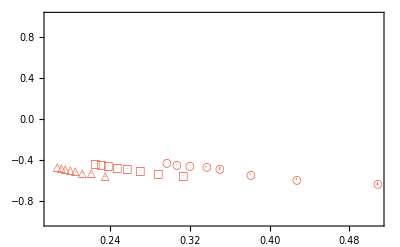

```mathematica
EqqbarNf4α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqbarMid[[i]]-Nf4α2LoopΔEqqbarMid[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqbarBig[[i]]-Nf4α2LoopΔEqqbarBig[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqbarSmall[[i]]-Nf4α2LoopΔEqqbarSmall[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{Q\\overline{Q}}^{\\text{(NNLO)}}-\\Delta E_{Q\\overline{Q}}^{\\text{(NLO)}} \\right]/\\Delta E_{Q\\overline{Q}}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

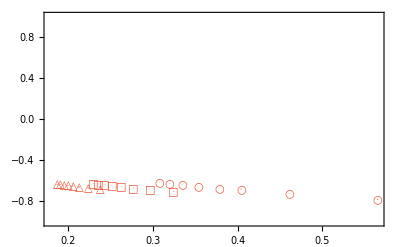

```mathematica
EqqbarNf4α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopΔEqqbarMid[[i]]-Nf4α1LoopΔEqqbarMid[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopΔEqqbarBig[[i]]-Nf4α1LoopΔEqqbarBig[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopΔEqqbarSmall[[i]]-Nf4α1LoopΔEqqbarSmall[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{Q\\overline{Q}}^{\\text{(NLO)}}-\\Delta E_{Q\\overline{Q}}^{\\text{(LO)}} \\right]/\\Delta E_{Q\\overline{Q}}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

```mathematica
EqqbarNf5αm2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopmΔEqqbarMid[[i]]-Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqbarMid[[i]]]},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopmΔEqqbarBig[[i]]-Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqbarBig[[i]]]},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopmΔEqqbarSmall[[i]]-Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqbarSmall[[i]]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{Q\\overline{Q}}^{\\text{(mNLO)}}-\\Delta E_{Q\\overline{Q}}^{\\text{(NLO)}} \\right]/\\Delta E_{Q\\overline{Q}}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf5α2LoopmΔEqqbarMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf5α2LoopmΔEqqbarMid⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

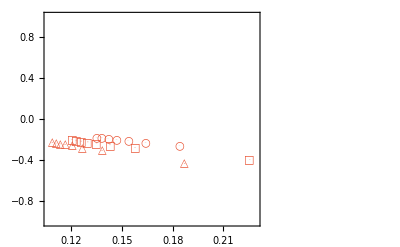

```mathematica
EqqbarNf5α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqbarMid[[i]]-Nf5α2LoopΔEqqbarMid[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqbarBig[[i]]-Nf5α2LoopΔEqqbarBig[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqbarSmall[[i]]-Nf5α2LoopΔEqqbarSmall[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{Q\\overline{Q}}^{\\text{(NNLO)}}-\\Delta E_{Q\\overline{Q}}^{\\text{(NLO)}} \\right]/\\Delta E_{Q\\overline{Q}}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

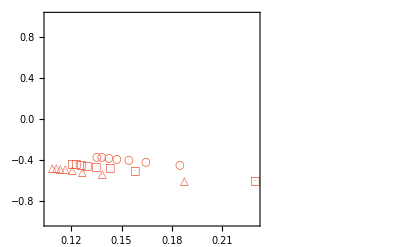

```mathematica
EqqbarNf5α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopΔEqqbarMid[[i]]-Nf5α1LoopΔEqqbarMid[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopΔEqqbarBig[[i]]-Nf5α1LoopΔEqqbarBig[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopΔEqqbarSmall[[i]]-Nf5α1LoopΔEqqbarSmall[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{Q\\overline{Q}}^{\\text{(NLO)}}-\\Delta E_{Q\\overline{Q}}^{\\text{(LO)}} \\right]/\\Delta E_{Q\\overline{Q}}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

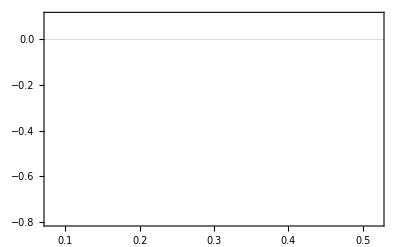

```mathematica
Eqqbarαm2LoopPlot=Show[EqqbarNf4αm2LoopPlot,EqqbarNf5αm2LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

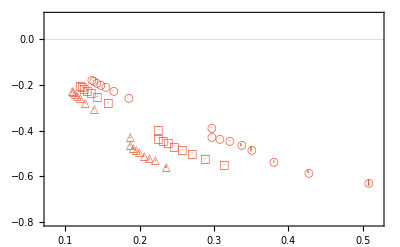

```mathematica
Eqqbarα3Loop2LoopPlot=Show[EqqbarNf4α3Loop2LoopPlot,EqqbarNf5α3Loop2LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

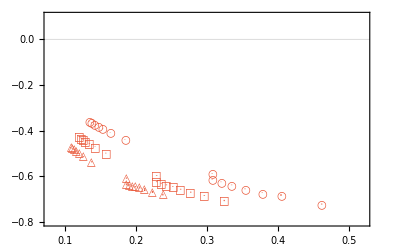

```mathematica
Eqqbarα2Loop1LoopPlot=Show[EqqbarNf4α2Loop1LoopPlot,EqqbarNf5α2Loop1LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_mNLO_vs_NLO.pdf",Eqqbarαm2LoopPlot];
```

```mathematica
Export[plotdir<>"DeltaEQQbar_NNLO_vs_NLO.pdf",Eqqbarα3Loop2LoopPlot];
```

```mathematica
Export[plotdir<>"DeltaEQQbar_NLO_vs_LO.pdf",Eqqbarα2Loop1LoopPlot];
```

### Quark mass fitting

```mathematica
moops=9.46030;
```

```mathematica
metab=9.3909;
```

```mathematica
(moops-metab)/moops
```

0.00733592

```mathematica
mJPsi=3.096;
```

```mathematica
metac=2.983;
```

```mathematica
(mJPsi-metac)/mJPsi
```

0.0364987

```mathematica
αs1Loop[4.8]
```

0.205705

```mathematica
muFROMmQ[mQ_]:=Block[{mu},mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}][[1]]]
```

```mathematica
muFROMmQ[4.8]
```

4.11947

```mathematica
mbFromOops[αsFun_,ΔEfun_,M_]:=Block[{mboops,αsmb,mbsol,mb},
αsmb[mb_?NumericQ]:=αsFun[muFROMmQ[mb]];
mboops[mb_]:=2mb +mb ΔEfun[αsmb[mb]];
mbsol=FindRoot[mboops[mb]-M,{mb,M/2}];
mb/.mbsol[[1]]];
```

```mathematica
Nf5α2LoopΔEqqbarFitMid[[1,2]]
```

-2.77798

```mathematica
(4/3)^2/4
```

4/9

```mathematica
ΔEqqbar1Loop[α_]:=-(4/3)^2/4α^2;
```

```mathematica
ΔEqqbar2Loop[α_]:=-(4/3)^2/4α^2+Nf4α2LoopΔEqqbarFitMid[[1,2]]α^3;
```

```mathematica
ΔEqqbar3Loop[α_]:=-(4/3)^2/4α^2+Nf4α3LoopΔEqqbarFitMid[[1,2]]α^3+Nf4α3LoopΔEqqbarFitMid[[1,3]]α^4;
```

```mathematica
ΔEqqbar1Loop[αs3Loop[4.8]]4.8
```

-0.101199

```mathematica
mb1Loop=mbFromOops[αs1Loop,ΔEqqbar1Loop,(3moops+metab)/4]
```

4.77041

```mathematica
mb2Loop=mbFromOops[αs2Loop,ΔEqqbar2Loop,(3moops+metab)/4]
```

4.87206

```mathematica
mb3Loop=mbFromOops[αs3Loop,ΔEqqbar3Loop,(3moops+metab)/4]
```

4.98485

```mathematica
mc1Loop=mbFromOops[αs1Loop,ΔEqqbar1Loop,(3mJPsi+metac)/4]
```

1.56161

```mathematica
mc2Loop=mbFromOops[αs2Loop,ΔEqqbar2Loop,(3mJPsi+metac)/4]
```

1.66856

```mathematica
mc3Loop=mbFromOops[αs3Loop,ΔEqqbar3Loop,(3mJPsi+metac)/4]
```

1.81005

```mathematica
αs1Loop[mu/.FindRoot[mu==fudge αs1Loop[mu]mb1Loop,{mu,10}][[1]]]
```

0.21485

```mathematica
αs2Loop[mu/.FindRoot[mu==fudge αs2Loop[mu]mb2Loop,{mu,10}][[1]]]
```

0.227279

```mathematica
αs3Loop[mu/.FindRoot[mu==fudge αs3Loop[mu]mb3Loop,{mu,10}][[1]]]
```

0.222324

```mathematica
αs1Loop[mu/.FindRoot[mu==fudge αs1Loop[mu]mc1Loop,{mu,10}][[1]]]
```

0.2827

```mathematica
αs2Loop[mu/.FindRoot[mu==fudge αs2Loop[mu]mc2Loop,{mu,10}][[1]]]
```

0.31268

```mathematica
αs3Loop[mu/.FindRoot[mu==fudge αs3Loop[mu]mc3Loop,{mu,10}][[1]]]
```

0.295094

```mathematica
mbMSbar=4.18
```

4.18

```mathematica
mcMSbar=1.280
```

1.28

```mathematica
Abs[mbMSbar-mb1Loop]/mbMSbar
```

0.141246

```mathematica
Abs[mbMSbar-mb2Loop]/mbMSbar
```

0.165565

```mathematica
Abs[mbMSbar-mb3Loop]/mbMSbar
```

0.192547

```mathematica
Abs[mcMSbar-mc1Loop]/mcMSbar
```

0.220007

```mathematica
Abs[mcMSbar-mc2Loop]/mcMSbar
```

0.303566

```mathematica
Abs[mcMSbar-mc3Loop]/mcMSbar
```

0.414099

```mathematica
1.280
```

1.28

```mathematica
4.198/4.576
```

0.917395

### M_QQQ

```mathematica
Lmur="0.5";
```

```mathematica
MbbbLQCD=Around[14.366,Sqrt[.009^2+.020^2]]
```

14.3660.022

```mathematica
MbbbLQCD/3
```

4.7890.007

```mathematica
MbbcLQCD=Around[11.195,Sqrt[.008^2+.020^2]]
```

11.1950.022

```mathematica
MbccLQCD=Around[8.007,Sqrt[.009^2+.020^2]]
```

8.0070.022

```mathematica
McccLQCD=Around[4.796,Sqrt[.008^2+.018^2]]
```

4.7960.020

```mathematica
moops=9.46030;
```

```mathematica
mJPsi=3.096;
```

```mathematica
(* 1S0 *)
```

```mathematica
mJPsi=Around[2.9839,.0005];
```

```mathematica
moops=Around[9.46030,.00026];
```

```mathematica
mJPsi=1/2(Around[2.9839,.0005]+Around[3.096900,.000006])
```

3.040400.00025

```mathematica
moops=1/2(Around[9.46030,.00026]+Around[9.3987,.0020])
```

9.42950.0010

```mathematica
mJPsi=(Around[3.096900,.000006])
```

3.0969006

```mathematica
moops=(Around[9.46030,.00026])
```

9.460300.00026

```mathematica
McccLQCD/mJPsi
```

1.5490.006

```mathematica
mJPsi
```

3.0969006

#### LO

```mathematica
Nf4α1LoopMid
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α1LoopBig]}]
```

{-0.0344255,-0.0364418,-0.0389357,-0.04201410,-0.0462277,-0.0521569,-0.0607898,-0.0750020.000011}

```mathematica
Nf4α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α1LoopMid]}]
```

{-0.0221254,-0.0231714,-0.024420433,-0.0259294,-0.0278274,-0.0303104,-0.0337455,-0.0389226}

```mathematica
Nf4α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α1LoopSmall]}]
```

{-0.015743524,-0.016314925,-0.016986324,-0.0177784,-0.0187625,-0.020008828,-0.0217884,-0.0244054}

```mathematica
ΔEqqqOα2=Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.4444425622,-0.4444462021,-0.4444462320,-0.4444462118,-0.4444444517,-0.4444457616,-0.4444442214,-0.4444452512}

```mathematica
Nf4α1LoopΔEqqqMid/Nf4α1LoopMid^2
```

{-0.476160.00010,-0.476290.00008,-0.476480.00006,-0.476390.00008,-0.476320.00007,-0.476290.00006,-0.476280.00007,-0.476400.00008}

```mathematica
ΔEqqqOα2WD=3/2Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.6666638332,-0.6666693131,-0.6666693429,-0.6666693128,-0.6666666826,-0.6666686424,-0.6666663321,-0.6666678718}

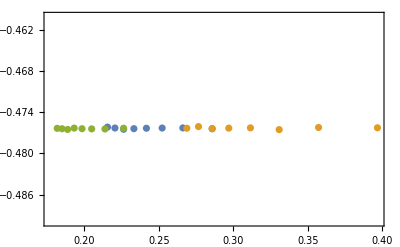

```mathematica
EqqqNf4α1LoopPlot=Show[ListPlot[{Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

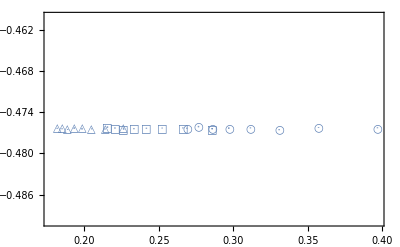

```mathematica
EqqqNf4α1LoopPlot=Show[ListPlot[{Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{-.49,-.46},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1]},PlotStyle->{ColorData[97][1]}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

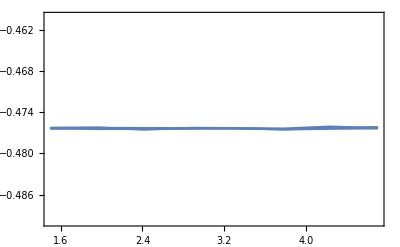

```mathematica
Nf4α1LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

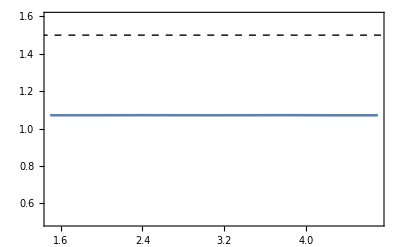

```mathematica
Nf4α1LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

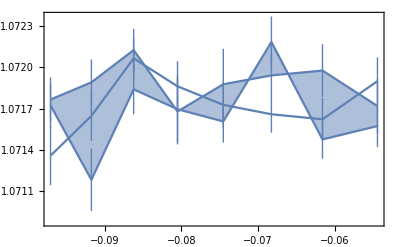

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

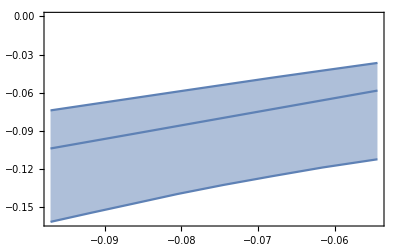

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

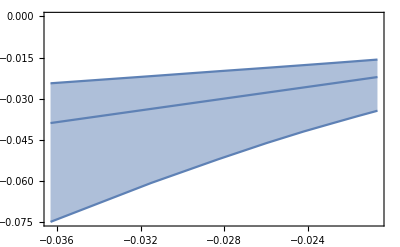

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Nf5α1LoopMid
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α1LoopBig]}]
```

{-0.008477727,-0.008851019,-0.009321432,-0.009935622,-0.010814221,-0.012212511,-0.015107525,-0.0344255}

```mathematica
Nf5α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α1LoopMid]}]
```

{-0.006844510,-0.007116816,-0.007450517,-0.007890420,-0.008509821,-0.009473724,-0.011408517,-0.0221254}

```mathematica
Nf5α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α1LoopSmall]}]
```

{-0.005644714,-0.005845214,-0.006091918,-0.006415718,-0.006870616,-0.007564020,-0.008918616,-0.015743524}

```mathematica
ΔEqqqOα2=Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.44444787,-0.44444647,-0.44444486,-0.44444716,-0.44444286,-0.44444685,-0.44444584,-0.4444425622}

```mathematica
Nf5α1LoopΔEqqqMid/Nf5α1LoopMid^2
```

{-0.476190.00007,-0.476420.00011,-0.476270.00011,-0.476290.00012,-0.476500.00012,-0.476310.00012,-0.476390.00007,-0.476160.00010}

```mathematica
ΔEqqqOα2WD=3/2Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.666671710,-0.666669610,-0.666667210,-0.66667079,-0.66666428,-0.66667028,-0.66666886,-0.6666638332}

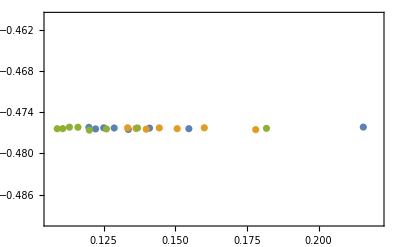

```mathematica
EqqqNf5α1LoopPlot=Show[ListPlot[{Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

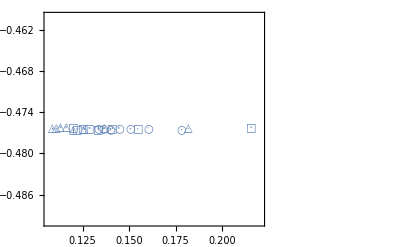

```mathematica
EqqqNf5α1LoopPlot=Show[ListPlot[{Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{-.49,-.46},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1]},PlotStyle->{ColorData[97][1]}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

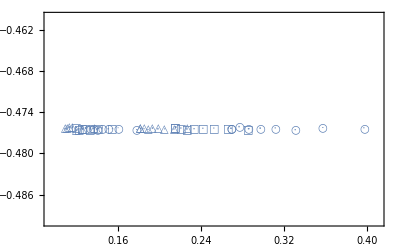

```mathematica
Eqqqα1LoopPlot=Show[EqqqNf4α1LoopPlot,EqqqNf5α1LoopPlot,PlotRange->{{.095,.41},{-.49,-.46}},Axes->False]
```

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_LO.pdf",Eqqqα1LoopPlot];
```

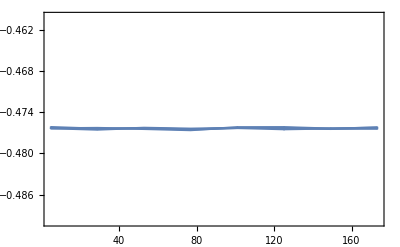

```mathematica
Nf5α1LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

```mathematica
Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α1LoopMid]}]
```

{{4.7,1.071360.00022},{28.7914,1.071870.00016},{52.8829,1.071680.00027},{76.9743,1.072130.00026},{101.066,1.071640.00028},{125.157,1.071600.00025},{149.249,1.071950.00025},{173.34,1.071420.00015}}

```mathematica
Nf5α1LoopΔEqqbarMid
```

{-0.00638827210,-0.00663909910,-0.00695266910,-0.00736289810,-0.00793726610,-0.00884001110,-0.01064349910,-0.02065160610}

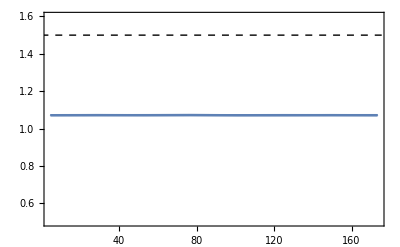

```mathematica
Nf5α1LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

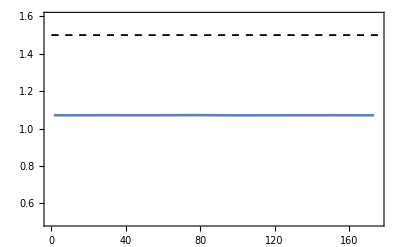

```mathematica
Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,PlotRange->{{Mc-2,Mt+2},{.5,1.6}}]
```

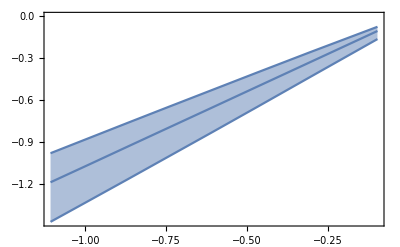

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

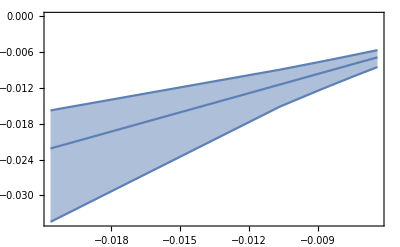

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqMid[[i]]},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqBig[[i]]},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqSmall[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

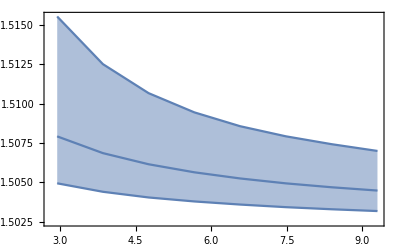

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqMid[[i]])/(2+Nf4α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqBig[[i]])/(2+Nf4α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqSmall[[i]])/(2+Nf4α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

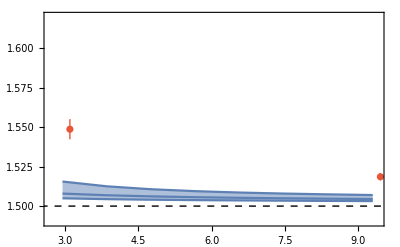

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.8Mc,2Mb},{1.49,1.62}},Axes->False]
```

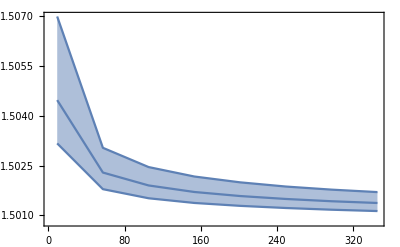

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqMid[[i]])/(2+Nf5α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqBig[[i]])/(2+Nf5α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqSmall[[i]])/(2+Nf5α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

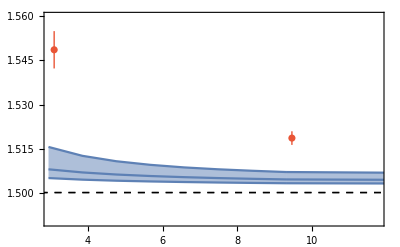

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{2Mc,2.5Mb},{1.49,1.56}},Axes->False]
```

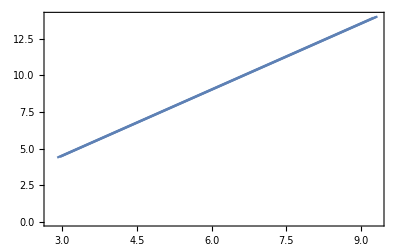

```mathematica
Nf4α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqqMid[[i]]Nf4α1LoopmQ[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarBig[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopmQ[[i]]Nf4α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarSmall[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopmQ[[i]]Nf4α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

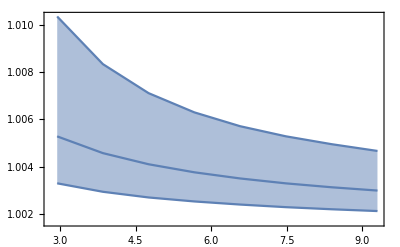

```mathematica
Nf4α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqMid[[i]])/(2+Nf4α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqBig[[i]])/(2+Nf4α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqSmall[[i]])/(2+Nf4α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

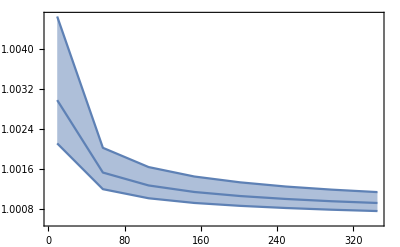

```mathematica
Nf5α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqMid[[i]])/(2+Nf5α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqBig[[i]])/(2+Nf5α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqSmall[[i]])/(2+Nf5α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

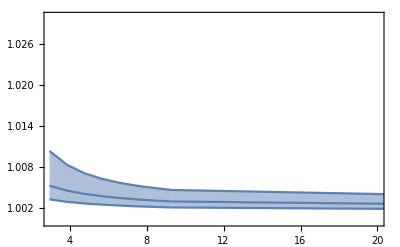

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,PlotRange->{{3,20},{1,1.03}}]
```

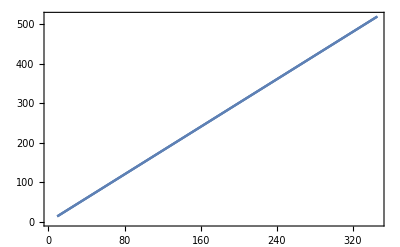

```mathematica
Nf5α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqqMid[[i]]Nf5α1LoopmQ[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarBig[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopmQ[[i]]Nf5α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarSmall[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopmQ[[i]]Nf5α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α1LoopMid[[1;;fitPt]],Nf5α1LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α1LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α1LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.476416,0.000807141},{0.000163019,0.00111413},1.74809}

```mathematica
Nf5α1LoopΔEqqqFitMid=LSPolyFitFixed[Nf5α1LoopMid[[1;;fitPt]],Nf5α1LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α1LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α1LoopMid[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.476301},{0.0000330833},1.57334}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α1LoopBig[[1;;fitPt]],Nf5α1LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α1LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α1LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.476306,-0.000139514},{0.000119806,0.00066863},1.67611}

```mathematica
Nf5α1LoopΔEqqqFitBig=LSPolyFitFixed[Nf5α1LoopBig[[1;;fitPt]],Nf5α1LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α1LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α1LoopBig[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.47633},{0.0000283025},1.44288}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α1LoopSmall[[1;;fitPt]],Nf5α1LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α1LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α1LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.476398,0.000352807},{0.000184071,0.00130959},1.52343}

```mathematica
Nf5α1LoopΔEqqqFitSmall=LSPolyFitFixed[Nf5α1LoopSmall[[1;;fitPt]],Nf5α1LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α1LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α1LoopSmall[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.476349},{0.0000372536},1.31616}

```mathematica
Around[Nf5α1LoopΔEqqqFitMid[[1,1]],Nf5α1LoopΔEqqqFitMid[[2,1]]]
```

-0.4763010.000033

```mathematica
Abs[Nf5α1LoopΔEqqqFitSmall[[1,1]]-Nf5α1LoopΔEqqqFitBig[[1,1]]]/2
```

9.37431×10^-6

```mathematica
Around[Nf5α1LoopΔEqqqFitMid[[1,1]],Abs[Nf5α1LoopΔEqqqFitSmall[[1,1]]-Nf5α1LoopΔEqqqFitBig[[1,1]]]/2]
```

-0.4763019

```mathematica
Around[Nf5α1LoopΔEqqqFitMid[[1,1]],Nf5α1LoopΔEqqqFitMid[[2,1]]]/-ΔEqqbarOα2Exact
```

-1.071680.00007

```mathematica
Around[Nf5α1LoopΔEqqqFitMid[[1,1]],Abs[Nf5α1LoopΔEqqqFitSmall[[1,1]]-Nf5α1LoopΔEqqqFitBig[[1,1]]]/2]/-ΔEqqbarOα2Exact
```

-1.0716770.000021

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α1LoopMid[[1;;fitPt]],Nf4α1LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α1LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α1LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.47629,-0.000185313},{0.000295987,0.0012052},1.83267}

```mathematica
Nf4α1LoopΔEqqqFitMid=LSPolyFitFixed[Nf4α1LoopMid[[1;;fitPt]],Nf4α1LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α1LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α1LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.47629,-0.000185313},{0.000295987,0.0012052},1.83267}

```mathematica
fitPt=8;
```

```mathematica
Nf4α1LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α1LoopBig[[1;;fitPt]],Nf4α1LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α1LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α1LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.476398,0.000328346},{0.000203482,0.000623622},2.58092}

```mathematica
Nf4α1LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α1LoopBig[[1;;fitPt]],Nf4α1LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α1LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α1LoopBig[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.476292},{0.0000270558},2.25182}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α1LoopSmall[[1;;fitPt]],Nf4α1LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α1LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α1LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.476511,0.000572995},{0.000395094,0.00199419},0.782768}

```mathematica
Nf4α1LoopΔEqqqFitSmall=LSPolyFitFixed[Nf4α1LoopSmall[[1;;fitPt]],Nf4α1LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α1LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α1LoopSmall[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.476398},{0.0000283938},0.682738}

```mathematica
Around[Nf4α1LoopΔEqqqFitMid[[1,1]],Nf4α1LoopΔEqqqFitMid[[2,1]]]
```

-0.476290.00030

```mathematica
Abs[Nf4α1LoopΔEqqqFitSmall[[1,1]]-Nf4α1LoopΔEqqqFitBig[[1,1]]]/2
```

0.0000527821

```mathematica
Around[Nf4α1LoopΔEqqqFitMid[[1,1]],Abs[Nf4α1LoopΔEqqqFitSmall[[1,1]]-Nf4α1LoopΔEqqqFitBig[[1,1]]]/2]
```

-0.476290.00005

```mathematica
Around[Nf4α1LoopΔEqqqFitMid[[1,1]],Nf4α1LoopΔEqqqFitMid[[2,1]]]/-ΔEqqbarOα2Exact
```

-1.07170.0007

```mathematica
Around[Nf4α1LoopΔEqqqFitMid[[1,1]],Abs[Nf4α1LoopΔEqqqFitSmall[[1,1]]-Nf4α1LoopΔEqqqFitBig[[1,1]]]/2]/-ΔEqqbarOα2Exact
```

-1.071650.00012

#### NLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.116690.00009,-0.128920.00009,-0.144950.00030,-0.166180.00021,-0.196770.00020,-0.234430.00032,-0.32550.0006,-0.53310.0018}

```mathematica
Nf4α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.074100.00008,-0.080010.00006,-0.086890.00007,-0.096070.00012,-0.107970.00011,-0.125110.00010,-0.150980.00014,-0.194280.00025}

```mathematica
Nf4α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.053140.00010,-0.056560.00009,-0.060120.00014,-0.064570.00013,-0.069940.00014,-0.077470.00021,-0.090340.00024,-0.107970.00021}

```mathematica
ΔEqqqOα2=Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.18170.0018,-1.20370.0020,-1.22640.0018,-1.25300.0016,-1.29510.0019,-1.34590.0023,-1.40830.0021,-1.51340.0032}

```mathematica
Nf4α2LoopΔEqqqMid/Nf4α2LoopMid^2
```

{-1.40790.0015,-1.43990.0011,-1.46970.0011,-1.51190.0019,-1.55960.0016,-1.62740.0014,-1.71830.0016,-1.84530.0023}

```mathematica
ΔEqqqOα2WD=3/2Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.77250.0026,-1.80560.0030,-1.83960.0028,-1.87950.0024,-1.94270.0028,-2.01890.0034,-2.11240.0031,-2.2700.005}

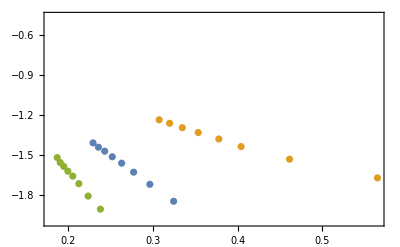

```mathematica
EqqqNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

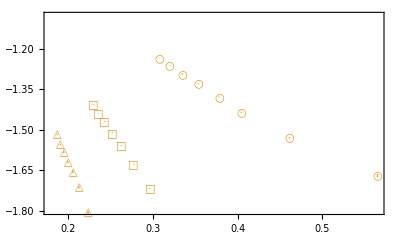

```mathematica
EqqqNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-1.5 1.2,-.9 1.2},PlotLegends->Placed[αLegendNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

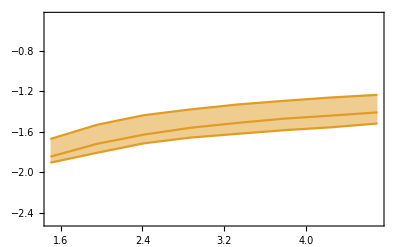

```mathematica
Nf4α2LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

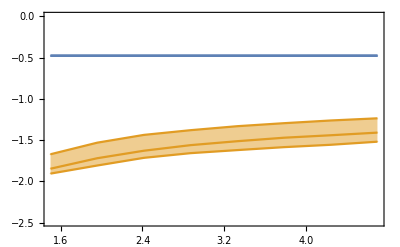

```mathematica
Show[Nf4α2LoopΔEqqqPlot,Nf4α1LoopΔEqqqPlot,PlotRange->{-2.49,0}]
```

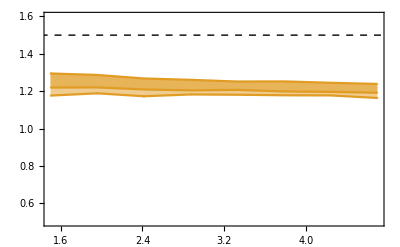

```mathematica
Nf4α2LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

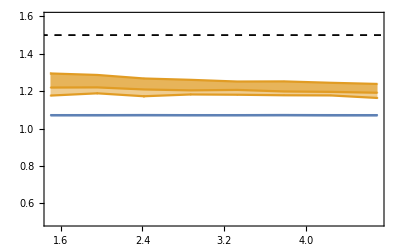

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot]
```

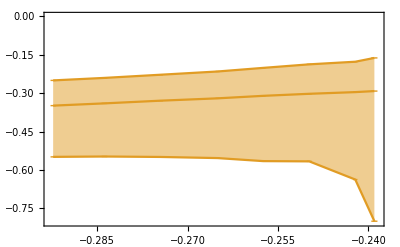

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

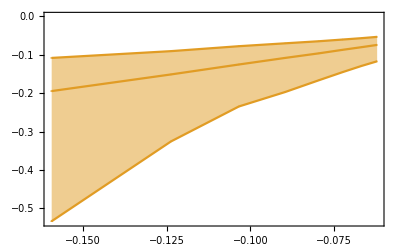

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Show[Nf4α2LoopΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.0145256,-0.0153206,-0.0164030.000010,-0.0177910.000010,-0.0198470.000015,-0.0233190.000015,-0.0310410.000020,-0.109100.00006}

```mathematica
Nf5α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.0129549,-0.0136169,-0.0144920.000010,-0.01560310,-0.0172960.000018,-0.0199670.000018,-0.0258020.000020,-0.069000.00006}

```mathematica
Nf5α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.0115380.000013,-0.0120580.000013,-0.0127710.000015,-0.0137170.000015,-0.0150220.000017,-0.0171650.000023,-0.021670.00004,-0.049430.00010}

```mathematica
ΔEqqqOα2=Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.77480.0010,-0.78230.0010,-0.78990.0012,-0.80260.0007,-0.81820.0010,-0.84040.0006,-0.88620.0010,-1.10210.0015}

```mathematica
Nf5α2LoopΔEqqqMid/Nf5α2LoopMid^2
```

{-0.89390.0006,-0.90230.0006,-0.91480.0007,-0.92710.0006,-0.94910.0010,-0.97700.0009,-1.03420.0008,-1.31100.0011}

```mathematica
ΔEqqqOα2WD=3/2Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-1.16220.0014,-1.17350.0015,-1.18480.0017,-1.20400.0011,-1.22730.0014,-1.26060.0009,-1.32930.0015,-1.65310.0022}

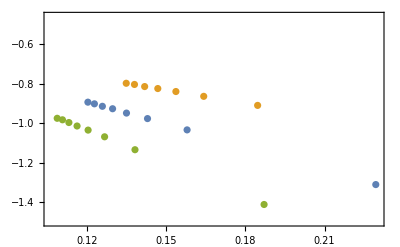

```mathematica
Eqqbarα2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.5,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

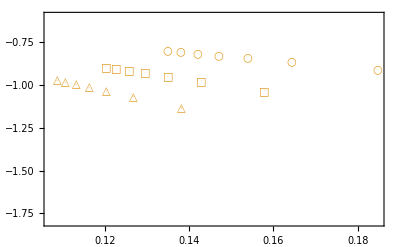

```mathematica
EqqqNf5α2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]-1}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]-1}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]-1}]},PlotRange->{-1.5 1.2,-.5 1.2},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

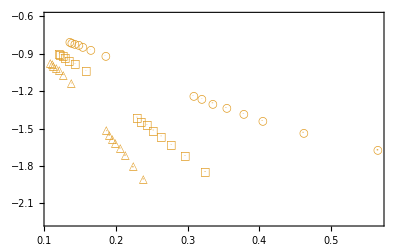

```mathematica
Eqqqα2LoopPlot=Show[EqqqNf4α2LoopPlot,EqqqNf5α2LoopPlot,PlotRange->{All,{-1.5 1.5,-.5 1.2}},Axes->False]
```

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_NLO.pdf",Eqqqα2LoopPlot];
```

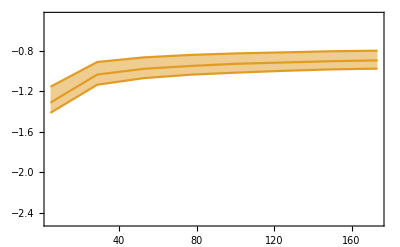

```mathematica
Nf5α2LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

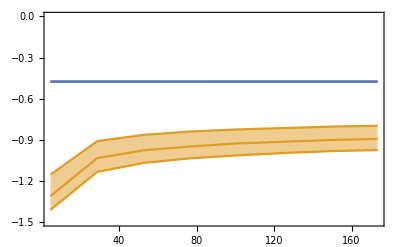

```mathematica
Show[Nf5α2LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-1.5,0},Axes->False]
```

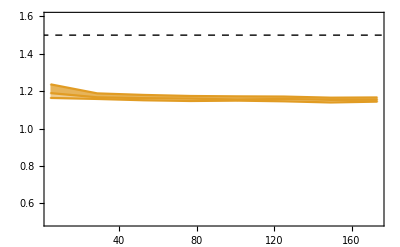

```mathematica
Nf5α2LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

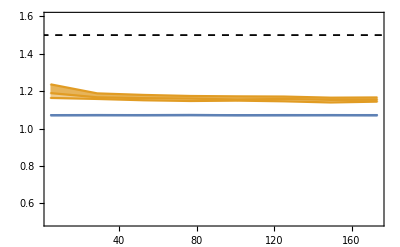

```mathematica
Show[Nf5α2LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot]
```

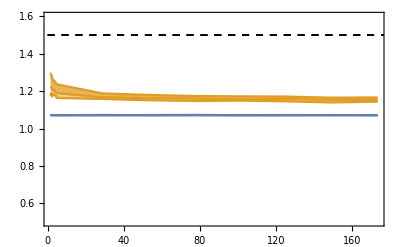

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mt},{.5,1.6}}]
```

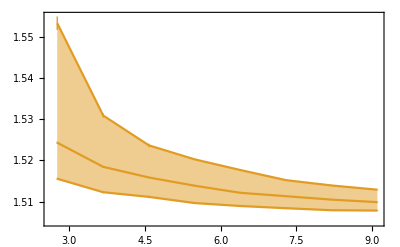

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqMid[[i]])/(2+Nf4α2LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqBig[[i]])/(2+Nf4α2LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqSmall[[i]])/(2+Nf4α2LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
mJPsi
```

3.0969006

```mathematica
McccLQCD/mJPsi
```

1.5490.006

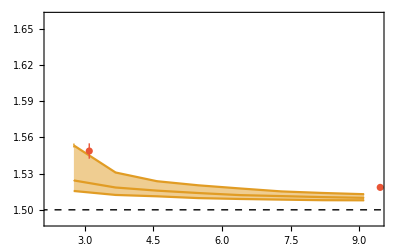

```mathematica
Show[Nf4α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi[[1]],McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.5Mc,2Mb},{1.49,1.66}},Axes->False]
```

```mathematica
Table[Series[(3+Nf5α1LoopΔEqqqBig[[ii]]  αα^2/Nf5α1LoopMid[[ii]]^2)/(2+Nf5α1LoopΔEqqbarBig[[ii]] αα^2/Nf5α1LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.117900.00009) αα^2+O[αα]^3,3/2+(0.118360.00007) αα^2+O[αα]^3,3/2+(0.118930.00010) αα^2+O[αα]^3,3/2+(0.119880.00007) αα^2+O[αα]^3,3/2+(0.120930.00006) αα^2+O[αα]^3,3/2+(0.1227350.000028) αα^2+O[αα]^3,3/2+(0.125860.00005) αα^2+O[αα]^3,3/2+(0.148030.00006) αα^2+O[αα]^3}

```mathematica
Table[Series[(3+Nf5α2LoopΔEqqqBig[[ii]]  αα^2/Nf5α2LoopMid[[ii]]^2)/(2+Nf5α2LoopΔEqqbarBig[[ii]] αα^2/Nf5α2LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.14340.0004) αα^2+O[αα]^3,3/2+(0.14590.0006) αα^2+O[αα]^3,3/2+(0.14540.0005) αα^2+O[αα]^3,3/2+(0.14780.0004) αα^2+O[αα]^3,3/2+(0.15110.0005) αα^2+O[αα]^3,3/2+(0.15480.0006) αα^2+O[αα]^3,3/2+(0.16330.0006) αα^2+O[αα]^3,3/2+(0.22080.0013) αα^2+O[αα]^3}

```mathematica
.12 .4^2
```

0.0192

```mathematica
.12 .2^2
```

0.0048

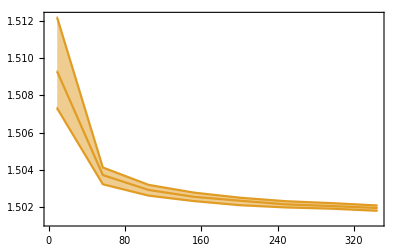

```mathematica
Nf5α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

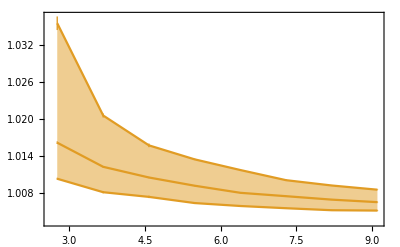

```mathematica
Nf4α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

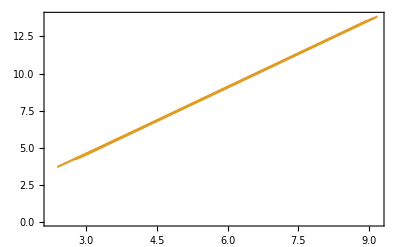

```mathematica
Nf4α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

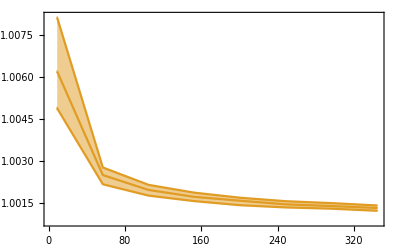

```mathematica
Nf5α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

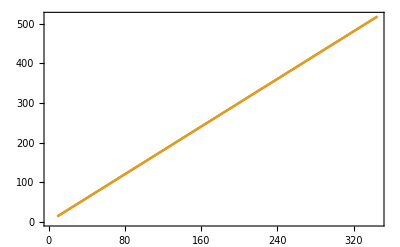

```mathematica
Nf5α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

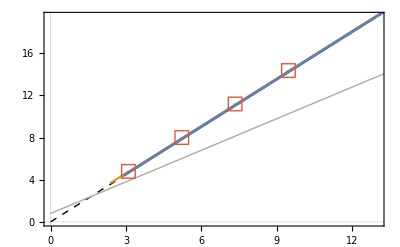

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Graphics[{Lighter[Gray],Line[{{0,.800},{1000,.800+1000}}]}],Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

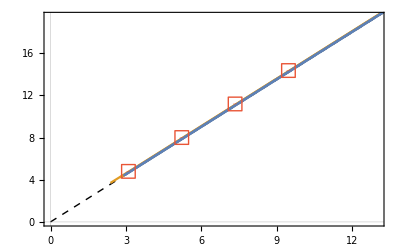

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

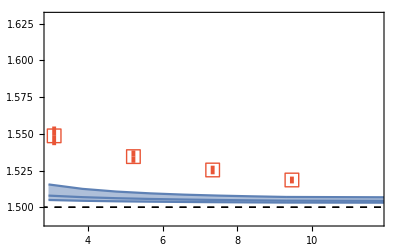

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.63}},Axes->False]
```

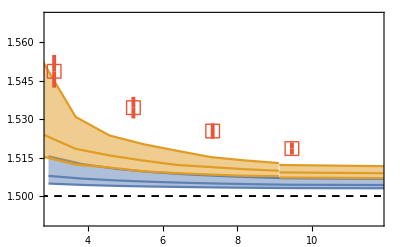

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.57}},Axes->False]
```

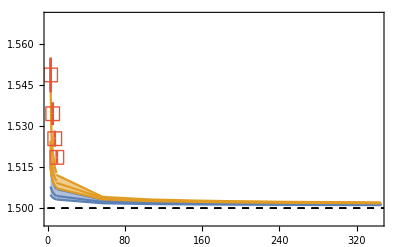

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,1.97Mt},{1.495,1.57}},Axes->False]
```

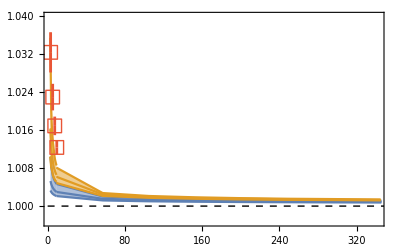

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopMid[[1;;fitPt]],Nf5α2LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α2LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.432988,-3.81824},{0.0014441,0.0104894},4.38581}

```mathematica
Nf5α2LoopΔEqqqFitMid=LSPolyFitFixed[Nf5α2LoopMid[[1;;fitPt]],Nf5α2LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α2LoopMid[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitMid[[1,1]]}]
```

{{-0.476301,-3.50845},{0.,0.00182909},132.273}

```mathematica
fitPt=5;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopBig[[1;;fitPt]],Nf5α2LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α2LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.493612,-2.25551},{0.00452412,0.0321691},3.89813}

```mathematica
Nf5α2LoopΔEqqqFitBig=LSPolyFitFixed[Nf5α2LoopBig[[1;;fitPt]],Nf5α2LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α2LoopBig[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitBig[[1,1]]}]
```

{{-0.47633,-2.37829},{0.,0.00132435},6.57138}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopSmall[[1;;fitPt]],Nf5α2LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α2LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.370014,-5.53942},{0.00416907,0.0351409},3.01061}

```mathematica
Nf5α2LoopΔEqqqFitSmall=LSPolyFitFixed[Nf5α2LoopSmall[[1;;fitPt]],Nf5α2LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α2LoopSmall[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitSmall[[1,1]]}]
```

{{-0.476349,-4.64848},{0.,0.00383332},95.5138}

```mathematica
Around[Nf5α2LoopΔEqqqFitMid[[1,2]],Nf5α2LoopΔEqqqFitMid[[2,2]]]
```

-3.50840.0018

```mathematica
Abs[Nf5α2LoopΔEqqqFitSmall[[1,2]]-Nf5α2LoopΔEqqqFitBig[[1,2]]]/2
```

1.1351

```mathematica
Around[Nf5α2LoopΔEqqqFitMid[[1,2]],Abs[Nf5α2LoopΔEqqqFitSmall[[1,2]]-Nf5α2LoopΔEqqqFitBig[[1,2]]]/2]
```

-3.51.1

```mathematica
Abs[Nf5α2LoopΔEqqqFitSmall[[1,2]]-Nf5α2LoopΔEqqqFitBig[[1,2]]]/2/ΔEqqbarOα2Exact
```

-2.55397

```mathematica
Around[Nf5α2LoopΔEqqqFitMid[[1,2]],Nf5α2LoopΔEqqqFitMid[[2,2]]]/ΔEqqbarOα2Exact
```

7.8940.004

```mathematica
Around[Nf5α2LoopΔEqqqFitMid[[1,2]],Abs[Nf5α2LoopΔEqqqFitSmall[[1,2]]-Nf5α2LoopΔEqqqFitBig[[1,2]]]/2]/ΔEqqbarOα2Exact
```

7.92.6

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],Nf4α2LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α2LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.353967,-4.59509},{0.00510926,0.019777},2.4435}

```mathematica
Nf4α2LoopΔEqqqFitMid=LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],Nf4α2LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α2LoopMid[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitMid[[1,1]]}]
```

{{-0.476301,-4.12392},{0.,0.00197294},83.9934}

```mathematica
fitPt=5;
```

```mathematica
Nf4α2LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α2LoopBig[[1;;fitPt]],Nf4α2LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α2LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.606655,-2.04486},{0.00729188,0.022155},0.749539}

```mathematica
Nf4α2LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α2LoopBig[[1;;fitPt]],Nf4α2LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α2LoopBig[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitBig[[1,1]]}]
```

{{-0.47633,-2.43977},{0.,0.00162233},80.42}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α2LoopSmall[[1;;fitPt]],Nf4α2LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α2LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.116758,-7.51829},{0.0151976,0.0749594},2.38503}

```mathematica
Nf4α2LoopΔEqqqFitSmall=LSPolyFitFixed[Nf4α2LoopSmall[[1;;fitPt]],Nf4α2LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α2LoopSmall[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitSmall[[1,1]]}]
```

{{-0.476349,-5.75008},{0.,0.00584698},82.0223}

```mathematica
Around[Nf4α2LoopΔEqqqFitMid[[1,2]],Nf4α2LoopΔEqqqFitMid[[2,2]]]
```

-4.12390.0020

```mathematica
Abs[Nf4α2LoopΔEqqqFitSmall[[1,2]]-Nf4α2LoopΔEqqqFitBig[[1,2]]]/2
```

1.65515

```mathematica
Around[Nf4α2LoopΔEqqqFitMid[[1,2]],Abs[Nf4α2LoopΔEqqqFitSmall[[1,2]]-Nf4α2LoopΔEqqqFitBig[[1,2]]]/2]
```

-4.11.7

```mathematica
Around[Nf4α2LoopΔEqqqFitMid[[1,2]],Nf4α2LoopΔEqqqFitMid[[2,2]]]/ΔEqqbarOα2Exact
```

9.2790.004

```mathematica
Around[Nf4α2LoopΔEqqqFitMid[[1,2]],Abs[Nf4α2LoopΔEqqqFitSmall[[1,2]]-Nf4α2LoopΔEqqqFitBig[[1,2]]]/2]/ΔEqqbarOα2Exact
```

9.4.

#### NNLO

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{0.674708,1.24639,1.08495,0.950356,nan,2.53485,1.99492,2.87011}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{0.873175,0.884225,1.17849,0.907973,1.1341,0.937408,nan,1.06153}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{0.680258,1.29448,1.20338,1.1205,0.919548,1.01325,0.633804,1.18448}

```mathematica
Nf4α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.204300.00015,-0.229710.00020,-0.26290.0004,-0.30840.0005,-0.35210.0009,-0.4810.012,-0.6820.006,-1.2870.025}

```mathematica
Nf4α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.133580.00005,-0.146280.00011,-0.161640.00014,-0.182540.00017,-0.210160.00014,-0.250990.00021,-0.314910.00019,-0.427650.00033}

```mathematica
Nf4α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.102040.00021,-0.110000.00020,-0.118130.00018,-0.130250.00025,-0.143870.00026,-0.164610.00027,-0.19610.0014,-0.24320.0007}

```mathematica
ΔEqqqOα2=Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-2.08080.0018,-2.15200.0018,-2.23770.0020,-2.35100.0024,-2.4970.004,-2.67670.0024,-2.94780.0028,-3.35710.0033}

```mathematica
Nf4α3LoopΔEqqqMid/Nf4α3LoopMid^2
```

{-2.62400.0010,-2.72740.0021,-2.83970.0025,-2.99320.0028,-3.17560.0021,-3.43320.0029,-3.79670.0022,-4.35050.0033}

```mathematica
ΔEqqqOα2WD=3/2Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-3.12110.0027,-3.22800.0027,-3.35650.0030,-3.5260.004,-3.7450.006,-4.0150.004,-4.4220.004,-5.0360.005}

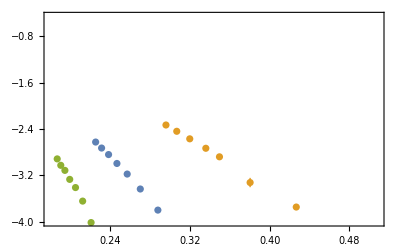

```mathematica
EqqqNf4α3LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-4,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

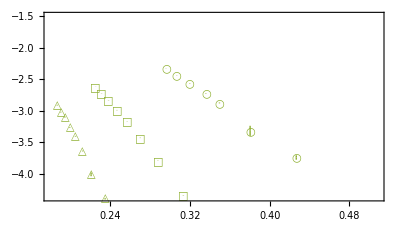

```mathematica
EqqqNf4α3LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-3.5 1.25,-1.2 1.25},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

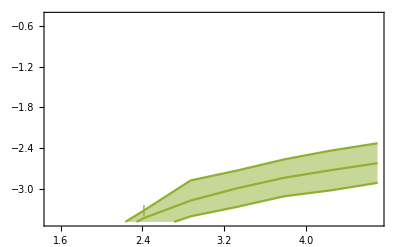

```mathematica
Nf4α3LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-3.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

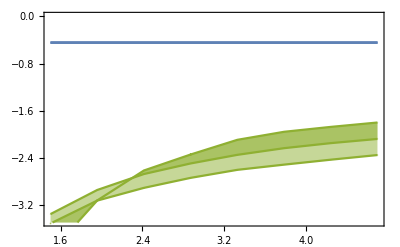

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,PlotRange->{-3.49,0}]
```

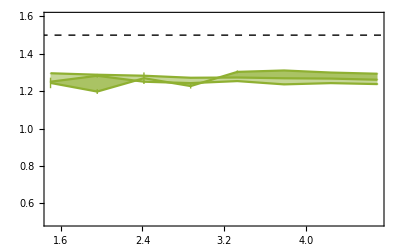

```mathematica
Nf4α3LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

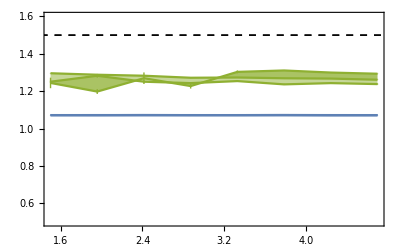

```mathematica
Show[Nf4α3LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot]
```

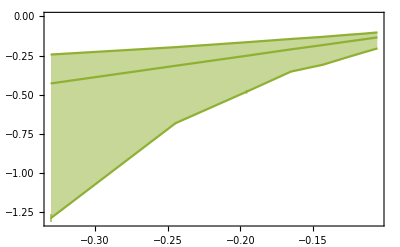

```mathematica
Nf4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Show[Nf4α3LoopΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α3LoopMid
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0180337,-0.0191815,-0.0206890.000013,-0.0227620.000011,-0.0257420.000016,-0.0309209,-0.0429520.000022,-0.178010.00018}

```mathematica
Nf5α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.0166770.000011,-0.0176860.000012,-0.0189760.000013,-0.0206940.000015,-0.0232740.000018,-0.0275020.000035,-0.0370520.000027,-0.115960.00009}

```mathematica
Nf5α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.0154020.000015,-0.0162220.000018,-0.0173270.000020,-0.0188060.000021,-0.0209940.000024,-0.0245040.000032,-0.032070.00004,-0.088780.00024}

```mathematica
ΔEqqqOα2=Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-0.96890.0010,-0.98660.0009,-1.00390.0014,-1.03090.0016,-1.06490.0013,-1.12050.0018,-1.22700.0014,-1.82040.0011}

```mathematica
Nf5α3LoopΔEqqqMid/Nf5α3LoopMid^2
```

{-1.15070.0008,-1.17210.0008,-1.19810.0008,-1.23010.0009,-1.27810.0010,-1.34740.0017,-1.48920.0011,-2.27800.0017}

```mathematica
ΔEqqqOα2WD=3/2Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-1.45330.0016,-1.47990.0014,-1.50590.0021,-1.54640.0024,-1.59730.0020,-1.68080.0028,-1.84050.0021,-2.73070.0017}

```mathematica
Nf5α3LoopΔEqqqMid
```

{-0.0166770.000011,-0.0176860.000012,-0.0189760.000013,-0.0206940.000015,-0.0232740.000018,-0.0275020.000035,-0.0370520.000027,-0.115960.00009}

```mathematica
Nf4α3LoopΔEqqqMid
```

{-0.133580.00005,-0.146280.00011,-0.161640.00014,-0.182540.00017,-0.210160.00014,-0.250990.00021,-0.314910.00019,-0.427650.00033}

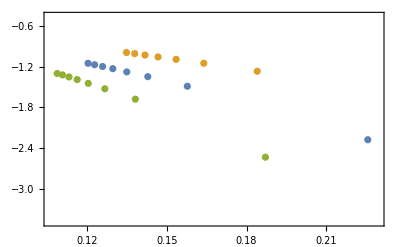

```mathematica
EqqqNf5α3LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

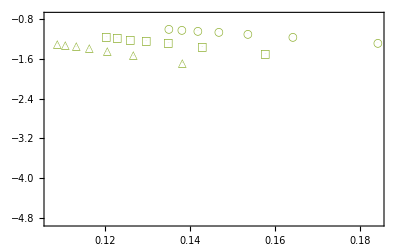

```mathematica
EqqqNf5α3LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]-1}],Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]-1}],Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]-1}]},PlotRange->{-3.9 1.25,-.6 1.25},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

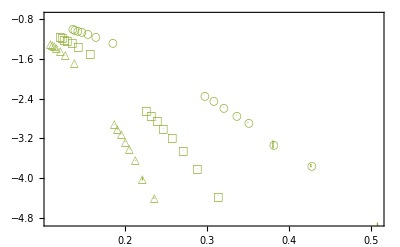

```mathematica
Eqqqα3LoopPlot=Show[EqqqNf4α3LoopPlot,EqqqNf5α3LoopPlot,PlotRange->{All,{-3.9 1.25,-.6 1.25}},Axes->False]
```

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_NNLO.pdf",Eqqqα3LoopPlot];
```

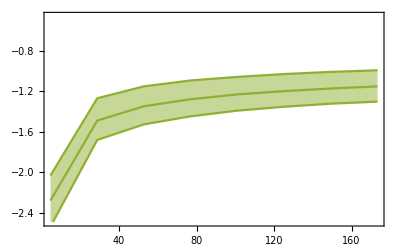

```mathematica
Nf5α3LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

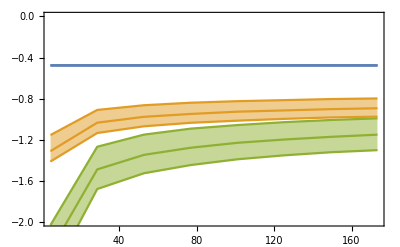

```mathematica
Show[Nf5α3LoopΔEqqqPlot,Nf5α2LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-2.,0},Axes->False]
```

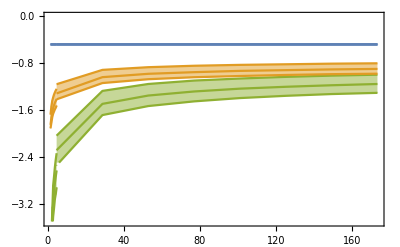

```mathematica
EqqqNf45α3LoopPlotMQ=Show[Nf4α3LoopΔEqqqPlot,Nf5α3LoopΔEqqqPlot,Nf4α2LoopΔEqqqPlot,Nf5α2LoopΔEqqqPlot,Nf4α1LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-3.5,0},Axes->False]
```

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_mQ.pdf",EqqqNf45α3LoopPlotMQ];
```

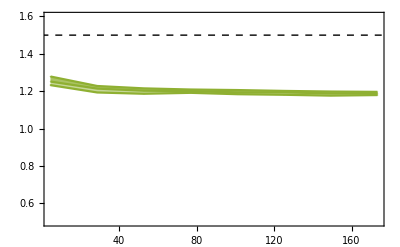

```mathematica
Nf5α3LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

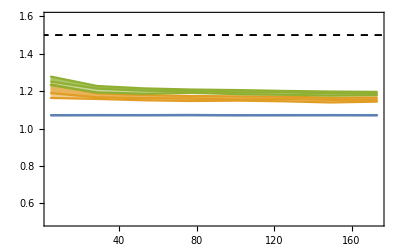

```mathematica
Show[Nf5α1LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot]
```

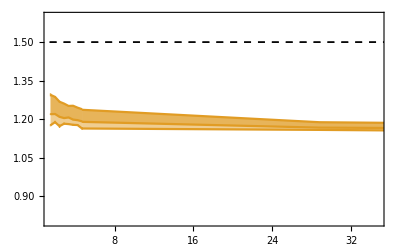

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,PlotRange->{{Mc,.2Mt},{.8,1.6}}]
```

```mathematica
Nf5α2LoopΔEqqqRatioPlot
```

-Graphics-

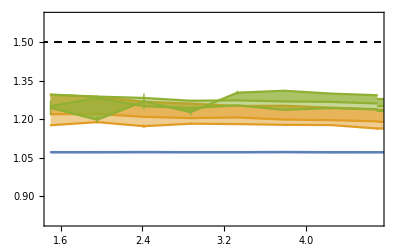

```mathematica
EqqqNf4α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α3LoopΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mb},{.8,1.6}}]
```

```mathematica
Export[plotdir<>"DeltaE_ratio_vs_mQ.pdf",EqqqNf4α3LoopPlotMQratio];
```

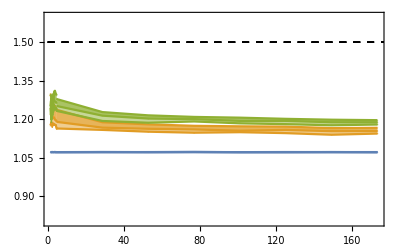

```mathematica
EqqqNf45α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α3LoopΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mt},{.8,1.6}}]
```

```mathematica
Export[plotdir<>"DeltaE_ratio_vs_mQ_big.pdf",EqqqNf45α3LoopPlotMQratio];
```

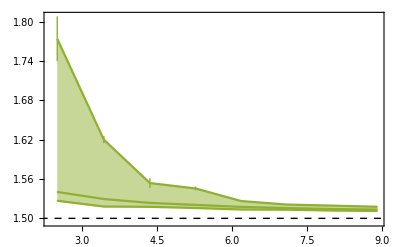

```mathematica
Nf4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqBig[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqSmall[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

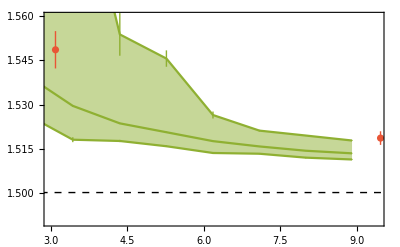

```mathematica
Show[Nf4α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{2Mc,2Mb},{1.49,1.56}},Axes->False]
```

```mathematica
Nf5α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqBig[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqSmall[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"M_ratio_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQratio];
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2Mt},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratioBig=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{1.495,1.57}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2Mt},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratioBig=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.4Mt},{1.495,1.57}},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"M_ratio_vs_MQQbar_big.pdf",MqqqNf45α3LoopPlotMQratioBig];
```

```mathematica
Nf4α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqBig[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqSmall[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopmQ[[i]]Nf4α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopmQ[[i]]Nf4α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf5α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqBig[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqSmall[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf5α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopmQ[[i]]Nf5α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopmQ[[i]]Nf5α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend,{0.35,0.85}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
scale=13;MqqqNf45α3LoopPlotMQQbar=Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α3LoopΔEqqbarVsPlotNoRatio,Nf5α3LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
(*scale=13;MqqqNf45α3LoopPlotMQQbar=Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α3LoopΔEqqbarVsPlotNoRatio,Nf5α3LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopmΔEqqbarVsPlotNoRatio,Nf5α2LoopmΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]*)
```

```mathematica
Export[plotdir<>"MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{2/3 1.495,2/3 1.57}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{2/3 1.495,2/3 1.57}},Axes->False]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqqBigNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.202840.00021,-0.227620.00022,-0.260510.00032,-0.30730.0005,-0.35350.0009,-0.46160.0009,-0.6930.010,-1.3800.028}

```mathematica
Nf4α3LoopΔEqqqMidNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.133080.00006,-0.145770.00009,-0.161110.00010,-0.181910.00018,-0.209430.00013,-0.249930.00020,-0.313480.00017,-0.425920.00028}

```mathematica
Nf4α3LoopΔEqqqSmallNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.101770.00021,-0.109740.00019,-0.117800.00017,-0.129950.00026,-0.143520.00025,-0.164170.00026,-0.19420.0008,-0.24260.0005}

```mathematica
Nf5α3LoopΔEqqqBigNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0179977,-0.0191366,-0.0206470.000013,-0.0227030.000011,-0.0256690.000017,-0.0308439,-0.0427990.000022,-0.176720.00018}

```mathematica
Nf5α3LoopΔEqqqMidNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.0166500.000011,-0.0176480.000015,-0.0189430.000012,-0.0206540.000014,-0.0232290.000018,-0.0274680.000022,-0.0369480.000031,-0.115520.00007}

```mathematica
Nf5α3LoopΔEqqqSmallNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.0153750.000015,-0.0162020.000018,-0.0173040.000019,-0.0188020.000028,-0.0209740.000029,-0.0244650.000031,-0.032060.00006,-0.088620.00019}

```mathematica
Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-.3,.3}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-.4,.2},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Table[(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]]),{i,1,Length[Nf4α3LoopMid]}]
```

{-0.000500.00008,-0.000510.00014,-0.000530.00017,-0.000640.00024,-0.000730.00019,-0.001060.00029,-0.001430.00025,-0.00170.0004}

```mathematica
Table[(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]]),{i,1,Length[Nf4α3LoopMid]}]
```

{-0.000270.00030,-0.000260.00028,-0.000320.00025,-0.00030.0004,-0.00030.0004,-0.00040.0004,-0.00190.0016,-0.00060.0009}

```mathematica
EqqqNf4α3Loop3BodyPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-.1,.1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\Delta E_{QQQ}"]},PlotLabel->MaTeX["\\text{NNLO 3-body effects}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf4αm2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopmΔEqqqMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqqMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopmΔEqqqBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqqBig[[i]]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopmΔEqqqSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqqSmall[[i]]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(mNLO)}}-\\Delta E_{QQQ}^{\\text{(NLO)}} \\right]/\\Delta E_{QQQ}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
EqqqNf4α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(NNLO)}}-\\Delta E_{QQQ}^{\\text{(NLO)}} \\right]/\\Delta E_{QQQ}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf4α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopΔEqqqMid[[i]]-Nf4α1LoopΔEqqqMid[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopΔEqqqBig[[i]]-Nf4α1LoopΔEqqqBig[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopΔEqqqSmall[[i]]-Nf4α1LoopΔEqqqSmall[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(NLO)}}-\\Delta E_{QQQ}^{\\text{(LO)}} \\right]/\\Delta E_{QQQ}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5α3Loop3BodyPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqqMid[[i]]-Nf5α3LoopΔEqqqMidNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqqBig[[i]]-Nf5α3LoopΔEqqqBigNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqqSmall[[i]]-Nf5α3LoopΔEqqqSmallNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-.01,.005},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\Delta E_{QQQ}"]},PlotLabel->MaTeX["\\text{NNLO 3-body effects}",Magnification->1.2]]
```

-Graphics-

```mathematica
threeBodyDiffPlot=Show[EqqqNf4α3Loop3BodyPlot,EqqqNf5α3Loop3BodyPlot,PlotRange->{{.08,.52},{-.045,.03}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Export[plotdir<>"qqq_three_body_forces.pdf",threeBodyDiffPlot];
```

```mathematica
Export[plotdir<>"qqq_three_body_forces_nf5.pdf",EqqqNf5α3Loop3BodyPlot];
```

```mathematica
EqqqNf5αm2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopmΔEqqqMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqqMid[[i]]]},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopmΔEqqqBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqqBig[[i]]]},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopmΔEqqqSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqqSmall[[i]]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(mNLO)}}-\\Delta E_{QQQ}^{\\text{(NLO)}} \\right]/\\Delta E_{QQQ}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf5α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf5α2LoopmΔEqqqMid⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
EqqqNf5α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqqMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqqBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqqSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(NNLO)}}-\\Delta E_{QQQ}^{\\text{(NLO)}} \\right]/\\Delta E_{QQQ}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopΔEqqqMid[[i]]-Nf5α1LoopΔEqqqMid[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopΔEqqqBig[[i]]-Nf5α1LoopΔEqqqBig[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopΔEqqqSmall[[i]]-Nf5α1LoopΔEqqqSmall[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(NLO)}}-\\Delta E_{QQQ}^{\\text{(LO)}} \\right]/\\Delta E_{QQQ}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Show[EqqqNf4αm2LoopPlot,EqqqNf5αm2LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Show[EqqqNf4α3Loop2LoopPlot,EqqqNf5α3Loop2LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Show[EqqqNf4α2Loop1LoopPlot,EqqqNf5α2Loop1LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]])/Abs[Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}]
```

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqbarMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{0.229421,((-1.19140.0022)+Nf4α2LoopmΔEqqqMid⟦1⟧/Nf4α2LoopmΔEqqbarMid⟦1⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦1⟧/Nf4α2LoopmΔEqqbarMid⟦1⟧]},{0.235729,((-1.19620.0022)+Nf4α2LoopmΔEqqqMid⟦2⟧/Nf4α2LoopmΔEqqbarMid⟦2⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦2⟧/Nf4α2LoopmΔEqqbarMid⟦2⟧]},{0.243152,((-1.19840.0020)+Nf4α2LoopmΔEqqqMid⟦3⟧/Nf4α2LoopmΔEqqbarMid⟦3⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦3⟧/Nf4α2LoopmΔEqqbarMid⟦3⟧]},{0.252078,((-1.20660.0021)+Nf4α2LoopmΔEqqqMid⟦4⟧/Nf4α2LoopmΔEqqbarMid⟦4⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦4⟧/Nf4α2LoopmΔEqqbarMid⟦4⟧]},{0.263112,((-1.20420.0021)+Nf4α2LoopmΔEqqqMid⟦5⟧/Nf4α2LoopmΔEqqbarMid⟦5⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦5⟧/Nf4α2LoopmΔEqqbarMid⟦5⟧]},{0.277271,((-1.20910.0023)+Nf4α2LoopmΔEqqqMid⟦6⟧/Nf4α2LoopmΔEqqbarMid⟦6⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦6⟧/Nf4α2LoopmΔEqqbarMid⟦6⟧]},{0.29642,((-1.22010.0021)+Nf4α2LoopmΔEqqqMid⟦7⟧/Nf4α2LoopmΔEqqbarMid⟦7⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦7⟧/Nf4α2LoopmΔEqqbarMid⟦7⟧]},{0.324475,((-1.21930.0030)+Nf4α2LoopmΔEqqqMid⟦8⟧/Nf4α2LoopmΔEqqbarMid⟦8⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦8⟧/Nf4α2LoopmΔEqqbarMid⟦8⟧]}}

```mathematica
Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]-Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]])/Abs[Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}]
```

{{0.229421,0.10080.0018},{0.235729,0.10410.0018},{0.243152,0.10540.0017},{0.252078,0.11170.0018},{0.263112,0.11000.0018},{0.277271,0.11370.0019},{0.29642,0.12170.0017},{0.324475,0.12090.0025}}

```mathematica
Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig)/Abs[Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]]},{i,1,Length[Nf4α2LoopBig]}]
```

Part::partd: Part specification Nf4α2LoopmΔEqqqBig⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqbarBig⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqqBig⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{0.307437,{((-1.23870.0013)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-1.12670.0012)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-1.00810.0012)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.87880.0011)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.74760.0008)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.63110.0017)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.46130.0007)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.28340.0009)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧]}},{0.319756,{((-1.36860.0013)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-1.24480.0012)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-1.11380.0012)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.97090.0012)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.82600.0009)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.69730.0018)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.50970.0008)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.31310.0010)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧]}},{0.334731,{((-1.53870.0034)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-1.39960.0031)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-1.25220.0028)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-1.09160.0025)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-0.92870.0021)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-0.78390.0026)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-0.57310.0014)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-0.35200.0013)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧]}},{0.353465,{((-1.76400.0025)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-1.60460.0023)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-1.43560.0022)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-1.25150.0020)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-1.06470.0016)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-0.89870.0026)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-0.65700.0012)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-0.40360.0013)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧]}},{0.377818,{((-2.08870.0026)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.89990.0023)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.69990.0023)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.48180.0022)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.26070.0017)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.06420.0029)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-0.77790.0014)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-0.47790.0015)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧]}},{0.404105,{((-2.4890.004)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-2.26360.0035)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-2.02520.0033)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-1.76550.0031)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-1.50200.0024)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-1.2680.004)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-0.92680.0018)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-0.56930.0019)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧]}},{0.461228,{((-3.4550.007)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-3.1430.007)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-2.8120.006)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-2.4510.005)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-2.0850.004)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-1.7600.006)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-1.28680.0031)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-0.79040.0028)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧]}},{0.564997,{((-5.6590.019)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-5.1480.018)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-4.6060.016)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-4.0150.014)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-3.4160.012)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-2.8830.012)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-2.1080.008)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-1.2950.006)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧]}}}

```mathematica
Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]-Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]])/Abs[Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}]
```

{{0.307437,0.13480.0011},{0.319756,0.13950.0010},{0.334731,0.14410.0023},{0.353465,0.14370.0017},{0.377818,0.15000.0013},{0.404105,0.15430.0029},{0.461228,0.16730.0024},{0.564997,0.1720.005}}

```mathematica
EqqqNf4αm2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]])/Abs[Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]])/Abs[Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopmΔEqqqSmall[[i]]/Nf4α2LoopmΔEqqbarSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]])/Abs[Nf4α2LoopmΔEqqqSmall[[i]]/Nf4α2LoopmΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(mNLO)}}-R_{QQQ}^{\\text{(NLO)}} \\right]/R_{QQQ}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqbarMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
EqqqNf4α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopΔEqqbarMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]])/Abs[Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopΔEqqbarBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]])/Abs[Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopΔEqqbarSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]])/Abs[Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(NNLO)}}-R_{QQQ}^{\\text{(NLO)}} \\right]/R_{QQQ}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf4α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]-Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]])/Abs[Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]-Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]])/Abs[Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]]-Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]])/Abs[Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(NLO)}}-R_{QQQ}^{\\text{(LO)}} \\right]/R_{QQQ}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5αm2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopmΔEqqqMid[[i]]/Nf5α2LoopmΔEqqbarMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]])/Abs[Nf5α2LoopmΔEqqqMid[[i]]/Nf5α2LoopmΔEqqbarMid[[i]]]},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopmΔEqqqBig[[i]]/Nf5α2LoopmΔEqqbarBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]])/Abs[Nf5α2LoopmΔEqqqBig[[i]]/Nf5α2LoopmΔEqqbarBig[[i]]]},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopmΔEqqqSmall[[i]]/Nf5α2LoopmΔEqqbarSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]])/Abs[Nf5α2LoopmΔEqqqSmall[[i]]/Nf5α2LoopmΔEqqbarSmall[[i]]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(mNLO)}}-R_{QQQ}^{\\text{(NLO)}} \\right]/R_{QQQ}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf5α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf5α2LoopmΔEqqbarMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf5α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
EqqqNf5α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopΔEqqbarMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]])/Abs[Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopΔEqqbarBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]])/Abs[Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopΔEqqbarSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]])/Abs[Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(NNLO)}}-R_{QQQ}^{\\text{(NLO)}} \\right]/R_{QQQ}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]]-Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopΔEqqbarMid[[i]])/Abs[Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]]-Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopΔEqqbarBig[[i]])/Abs[Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]]-Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopΔEqqbarSmall[[i]])/Abs[Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(NLO)}}-R_{QQQ}^{\\text{(LO)}} \\right]/R_{QQQ}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
RmNLODiffPlot=Show[EqqqNf4αm2LoopPlot,EqqqNf5αm2LoopPlot,PlotRange->{{.08,.52},{-.19,.05}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Export[plotdir<>"RQQQ_mNLO_vs_NLO.pdf",RmNLODiffPlot];
```

```mathematica
RNNLODiffPlot=Show[EqqqNf4α3Loop2LoopPlot,EqqqNf5α3Loop2LoopPlot,PlotRange->{{.08,.52},{-.08,.16}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Export[plotdir<>"RQQQ_NNLO_vs_NLO.pdf",RNNLODiffPlot];
```

```mathematica
RNLODiffPlot=Show[EqqqNf4α2Loop1LoopPlot,EqqqNf5α2Loop1LoopPlot,PlotRange->{{.08,.52},{-.08,.16}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Export[plotdir<>"RQQQ_NLO_vs_LO.pdf",RNLODiffPlot];
```

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],Nf5α3LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α3LoopMid[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.515674,-2.39827,-23.981},{0.0126366,0.158637,0.471701},1.90381}

```mathematica
Nf5α3LoopΔEqqqFitMid=LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],Nf5α3LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α3LoopMid[[1;;fitPt]]^2)^-2],3,{Nf5α1LoopΔEqqqFitMid[[1,1]],Nf5α2LoopΔEqqqFitMid[[1,2]]}]
```

{{-0.476301,-3.50845,-18.3799},{0.,0.,0.0174347},395.05}

```mathematica
fitPt=5;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],Nf5α3LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α3LoopBig[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.151047,-6.92666,5.15667},{0.133101,1.85851,6.47662},4.50529}

```mathematica
Nf5α3LoopΔEqqqFitBig=LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],Nf5α3LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α3LoopBig[[1;;fitPt]]^2)^-2],3,{Nf5α1LoopΔEqqqFitBig[[1,1]],Nf5α2LoopΔEqqqFitBig[[1,2]]}]
```

{{-0.47633,-2.37829,-10.7113},{0.,0.,0.00968985},3.75704}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],Nf5α3LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α3LoopSmall[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.698472,0.366532,-54.3128},{0.0345617,0.52566,1.97364},3.25593}

```mathematica
Nf5α3LoopΔEqqqFitSmall=LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],Nf5α3LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α3LoopSmall[[1;;fitPt]]^2)^-2],3,{Nf5α1LoopΔEqqqFitSmall[[1,1]],Nf5α2LoopΔEqqqFitSmall[[1,2]]}]
```

{{-0.476349,-4.64848,-28.193},{0.,0.,0.0421351},194.864}

```mathematica
Around[Nf5α3LoopΔEqqqFitMid[[1,3]],Nf5α3LoopΔEqqqFitMid[[2,3]]]
```

-18.3800.017

```mathematica
Abs[Nf5α3LoopΔEqqqFitSmall[[1,3]]-Nf5α3LoopΔEqqqFitBig[[1,3]]]/2
```

8.74083

```mathematica
Around[Nf5α3LoopΔEqqqFitMid[[1,3]],Abs[Nf5α3LoopΔEqqqFitSmall[[1,3]]-Nf5α3LoopΔEqqqFitBig[[1,3]]]/2]
```

-18.9.

```mathematica
Abs[Nf5α3LoopΔEqqqFitSmall[[1,3]]-Nf5α3LoopΔEqqqFitBig[[1,3]]]/2/ΔEqqbarOα2Exact
```

-19.6669

```mathematica
Around[Nf5α3LoopΔEqqqFitMid[[1,3]],Nf5α3LoopΔEqqqFitMid[[2,3]]]/ΔEqqbarOα2Exact
```

41.350.04

```mathematica
Around[Nf5α3LoopΔEqqqFitMid[[1,3]],Abs[Nf5α3LoopΔEqqqFitSmall[[1,3]]-Nf5α3LoopΔEqqqFitBig[[1,3]]]/2]/ΔEqqbarOα2Exact
```

41.20.

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α3LoopMid[[1;;fitPt]],Nf4α3LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α3LoopMid[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.828242,0.473848,-37.3816},{0.076517,0.593232,1.13673},3.19724}

```mathematica
Nf4α3LoopΔEqqqFitMid=LSPolyFitFixed[Nf4α3LoopMid[[1;;fitPt]],Nf4α3LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α3LoopMid[[1;;fitPt]]^2)^-2],3,{Nf4α1LoopΔEqqqFitMid[[1,1]],Nf4α2LoopΔEqqqFitMid[[1,2]]}]
```

{{-0.47629,-4.12392,-24.7629},{0.,0.,0.0111962},783.721}

```mathematica
fitPt=5;
```

```mathematica
Nf4α3LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α3LoopBig[[1;;fitPt]],Nf4α3LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α3LoopBig[[1;;fitPt]]^2)^-2],3,{}]
```

{{0.069801,-6.36479,-5.88337},{0.556275,3.51604,5.54185},0.272692}

```mathematica
Nf4α3LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α3LoopBig[[1;;fitPt]],Nf4α3LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α3LoopBig[[1;;fitPt]]^2)^-2],3,{Nf4α1LoopΔEqqqFitBig[[1,1]],Nf4α2LoopΔEqqqFitBig[[1,2]]}]
```

{{-0.476292,-2.43977,-12.8547},{0.,0.,0.0127485},8.90004}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α3LoopSmall[[1;;fitPt]],Nf4α3LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α3LoopSmall[[1;;fitPt]]^2)^-2],3,{}]
```

{{-2.3828,19.4039,-119.056},{0.54754,5.31625,12.8698},6.25397}

```mathematica
Nf4α3LoopΔEqqqFitSmall=LSPolyFitFixed[Nf4α3LoopSmall[[1;;fitPt]],Nf4α3LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α3LoopSmall[[1;;fitPt]]^2)^-2],3,{Nf4α1LoopΔEqqqFitSmall[[1,1]],Nf4α2LoopΔEqqqFitSmall[[1,2]]}]
```

{{-0.476398,-5.75008,-41.2488},{0.,0.,0.0563661},171.584}

```mathematica
Around[Nf4α3LoopΔEqqqFitMid[[1,3]],Nf4α3LoopΔEqqqFitMid[[2,3]]]
```

-24.7630.011

```mathematica
Abs[Nf4α3LoopΔEqqqFitSmall[[1,3]]-Nf4α3LoopΔEqqqFitBig[[1,3]]]/2
```

14.1971

```mathematica
Around[Nf4α3LoopΔEqqqFitMid[[1,3]],Abs[Nf4α3LoopΔEqqqFitSmall[[1,3]]-Nf4α3LoopΔEqqqFitBig[[1,3]]]/2]
```

-25.14.

```mathematica
Around[Nf4α3LoopΔEqqqFitMid[[1,3]],Nf4α3LoopΔEqqqFitMid[[2,3]]]/ΔEqqbarOα2Exact
```

55.7160.025

```mathematica
Around[Nf4α3LoopΔEqqqFitMid[[1,3]],Abs[Nf4α3LoopΔEqqqFitSmall[[1,3]]-Nf4α3LoopΔEqqqFitBig[[1,3]]]/2]/ΔEqqbarOα2Exact
```

56.32.

```mathematica
(* ratios *)
```

```mathematica
fitPt=8;
```

```mathematica
Nf5α1LoopRatioFitMid=LSPolyFitFixed[Nf5α1LoopMid[[1;;fitPt]],(Nf5α1LoopΔEqqqMid[[1;;fitPt]]/Nf5α1LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α1LoopΔEqqqMid[[1;;fitPt]]/Nf5α1LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07167},{0.0000744392},1.58436}

```mathematica
Nf5α1LoopRatioFitBig=LSPolyFitFixed[Nf5α1LoopBig[[1;;fitPt]],(Nf5α1LoopΔEqqqBig[[1;;fitPt]]/Nf5α1LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α1LoopΔEqqqBig[[1;;fitPt]]/Nf5α1LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07174},{0.0000636821},1.43954}

```mathematica
Nf5α1LoopRatioFitSmall=LSPolyFitFixed[Nf5α1LoopSmall[[1;;fitPt]],(Nf5α1LoopΔEqqqSmall[[1;;fitPt]]/Nf5α1LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α1LoopΔEqqqSmall[[1;;fitPt]]/Nf5α1LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07178},{0.0000838221},1.31426}

```mathematica
Around[Nf5α1LoopRatioFitMid[[1,1]],Nf5α1LoopRatioFitMid[[2,1]]]
```

1.071670.00007

```mathematica
Abs[Nf5α1LoopRatioFitSmall[[1,1]]-Nf5α1LoopRatioFitBig[[1,1]]]/2
```

0.000020529

```mathematica
Around[Nf5α1LoopRatioFitMid[[1,1]],Abs[Nf5α1LoopRatioFitSmall[[1,1]]-Nf5α1LoopRatioFitBig[[1,1]]]/2]
```

1.0716740.000021

```mathematica
Nf4α1LoopRatioFitMid=LSPolyFitFixed[Nf4α1LoopMid[[1;;fitPt]],(Nf4α1LoopΔEqqqMid[[1;;fitPt]]/Nf4α1LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α1LoopΔEqqqMid[[1;;fitPt]]/Nf4α1LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07175},{0.0000579565},1.54524}

```mathematica
Nf4α1LoopRatioFitBig=LSPolyFitFixed[Nf4α1LoopBig[[1;;fitPt]],(Nf4α1LoopΔEqqqBig[[1;;fitPt]]/Nf4α1LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α1LoopΔEqqqBig[[1;;fitPt]]/Nf4α1LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07166},{0.0000608756},2.24534}

```mathematica
Nf4α1LoopRatioFitSmall=LSPolyFitFixed[Nf4α1LoopSmall[[1;;fitPt]],(Nf4α1LoopΔEqqqSmall[[1;;fitPt]]/Nf4α1LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α1LoopΔEqqqSmall[[1;;fitPt]]/Nf4α1LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.0719},{0.0000638866},0.681669}

```mathematica
Around[Nf4α1LoopRatioFitMid[[1,1]],Nf4α1LoopRatioFitMid[[2,1]]]
```

1.071750.00006

```mathematica
Abs[Nf4α1LoopRatioFitSmall[[1,1]]-Nf4α1LoopRatioFitBig[[1,1]]]/2
```

0.000119576

```mathematica
Around[Nf4α1LoopRatioFitMid[[1,1]],Abs[Nf4α1LoopRatioFitSmall[[1,1]]-Nf4α1LoopRatioFitBig[[1,1]]]/2]
```

1.071750.00012

```mathematica
fitPt=8;
```

```mathematica
Nf5α2LoopRatioFitMid=LSPolyFitFixed[Nf5α2LoopMid[[1;;fitPt]],(Nf5α2LoopΔEqqqMid[[1;;fitPt]]/Nf5α2LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α2LoopΔEqqqMid[[1;;fitPt]]/Nf5α2LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.16124},{0.000555547},44.0787}

```mathematica
Nf5α2LoopRatioFitBig=LSPolyFitFixed[Nf5α2LoopBig[[1;;fitPt]],(Nf5α2LoopΔEqqqBig[[1;;fitPt]]/Nf5α2LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α2LoopΔEqqqBig[[1;;fitPt]]/Nf5α2LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.17747},{0.000347522},363.481}

```mathematica
Nf5α2LoopRatioFitSmall=LSPolyFitFixed[Nf5α2LoopSmall[[1;;fitPt]],(Nf5α2LoopΔEqqqSmall[[1;;fitPt]]/Nf5α2LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α2LoopΔEqqqSmall[[1;;fitPt]]/Nf5α2LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.1474},{0.000861714},8.22915}

```mathematica
Around[Nf5α2LoopRatioFitMid[[1,1]],Nf5α2LoopRatioFitMid[[2,1]]]
```

1.16120.0006

```mathematica
Abs[Nf5α2LoopRatioFitSmall[[1,1]]-Nf5α2LoopRatioFitBig[[1,1]]]/2
```

0.0150348

```mathematica
Around[Nf5α2LoopRatioFitMid[[1,1]],Abs[Nf5α2LoopRatioFitSmall[[1,1]]-Nf5α2LoopRatioFitBig[[1,1]]]/2]
```

1.1610.015

```mathematica
Nf4α2LoopRatioFitMid=LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],(Nf4α2LoopΔEqqqMid[[1;;fitPt]]/Nf4α2LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α2LoopΔEqqqMid[[1;;fitPt]]/Nf4α2LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.20476},{0.000781469},20.5423}

```mathematica
Nf4α2LoopRatioFitBig=LSPolyFitFixed[Nf4α2LoopBig[[1;;fitPt]],(Nf4α2LoopΔEqqqBig[[1;;fitPt]]/Nf4α2LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α2LoopΔEqqqBig[[1;;fitPt]]/Nf4α2LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.25031},{0.000669399},51.4504}

```mathematica
Nf4α2LoopRatioFitSmall=LSPolyFitFixed[Nf4α2LoopSmall[[1;;fitPt]],(Nf4α2LoopΔEqqqSmall[[1;;fitPt]]/Nf4α2LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α2LoopΔEqqqSmall[[1;;fitPt]]/Nf4α2LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.17727},{0.00150969},2.4784}

```mathematica
Around[Nf4α2LoopRatioFitMid[[1,1]],Nf4α2LoopRatioFitMid[[2,1]]]
```

1.20480.0008

```mathematica
Abs[Nf4α2LoopRatioFitSmall[[1,1]]-Nf4α2LoopRatioFitBig[[1,1]]]/2
```

0.0365177

```mathematica
Around[Nf4α2LoopRatioFitMid[[1,1]],Abs[Nf4α2LoopRatioFitSmall[[1,1]]-Nf4α2LoopRatioFitBig[[1,1]]]/2]
```

1.200.04

```mathematica
fitPt=8;
```

```mathematica
Nf5α3LoopRatioFitMid=LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],(Nf5α3LoopΔEqqqMid[[1;;fitPt]]/Nf5α3LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α3LoopΔEqqqMid[[1;;fitPt]]/Nf5α3LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.20779},{0.000575672},252.125}

```mathematica
Nf5α3LoopRatioFitBig=LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],(Nf5α3LoopΔEqqqBig[[1;;fitPt]]/Nf5α3LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α3LoopΔEqqqBig[[1;;fitPt]]/Nf5α3LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.20701},{0.000293855},292.831}

```mathematica
Nf5α3LoopRatioFitSmall=LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],(Nf5α3LoopΔEqqqSmall[[1;;fitPt]]/Nf5α3LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α3LoopΔEqqqSmall[[1;;fitPt]]/Nf5α3LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.18662},{0.000854606},26.2626}

```mathematica
Around[Nf5α3LoopRatioFitMid[[1,1]],Nf5α3LoopRatioFitMid[[2,1]]]
```

1.20780.0006

```mathematica
Abs[Nf5α3LoopRatioFitSmall[[1,1]]-Nf5α3LoopRatioFitBig[[1,1]]]/2
```

0.0101977

```mathematica
Around[Nf5α3LoopRatioFitMid[[1,1]],Abs[Nf5α3LoopRatioFitSmall[[1,1]]-Nf5α3LoopRatioFitBig[[1,1]]]/2]
```

1.2080.010

```mathematica
Nf4α3LoopRatioFitMid=LSPolyFitFixed[Nf4α3LoopMid[[1;;fitPt]],(Nf4α3LoopΔEqqqMid[[1;;fitPt]]/Nf4α3LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α3LoopΔEqqqMid[[1;;fitPt]]/Nf4α3LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.2751},{0.000545882},63.686}

```mathematica
Nf4α3LoopRatioFitBig=LSPolyFitFixed[Nf4α3LoopBig[[1;;fitPt]],(Nf4α3LoopΔEqqqBig[[1;;fitPt]]/Nf4α3LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α3LoopΔEqqqBig[[1;;fitPt]]/Nf4α3LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.29834},{0.00103333},18.9664}

```mathematica
Nf4α3LoopRatioFitSmall=LSPolyFitFixed[Nf4α3LoopSmall[[1;;fitPt]],(Nf4α3LoopΔEqqqSmall[[1;;fitPt]]/Nf4α3LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α3LoopΔEqqqSmall[[1;;fitPt]]/Nf4α3LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.24483},{0.0014617},5.00518}

```mathematica
Around[Nf4α3LoopRatioFitMid[[1,1]],Nf4α3LoopRatioFitMid[[2,1]]]
```

1.27510.0005

```mathematica
Abs[Nf4α3LoopRatioFitSmall[[1,1]]-Nf4α3LoopRatioFitBig[[1,1]]]/2
```

0.0267558

```mathematica
Around[Nf4α3LoopRatioFitMid[[1,1]],Abs[Nf4α3LoopRatioFitSmall[[1,1]]-Nf4α3LoopRatioFitBig[[1,1]]]/2]
```

1.2750.027

### M_tetra

```mathematica
Lmur="0.0";
```

```mathematica
MbbbLQCD=Around[14.366,Sqrt[.009^2+.020^2]]
```

14.3660.022

```mathematica
MbbbLQCD/3
```

4.7890.007

```mathematica
MbbcLQCD=Around[11.195,Sqrt[.008^2+.020^2]]
```

11.1950.022

```mathematica
MbccLQCD=Around[8.007,Sqrt[.009^2+.020^2]]
```

8.0070.022

```mathematica
McccLQCD=Around[4.796,Sqrt[.008^2+.018^2]]
```

4.7960.020

```mathematica
moops=9.46030;
```

```mathematica
mJPsi=3.096;
```

```mathematica
(* 1S0 *)
```

```mathematica
mJPsi=Around[2.9839,.0005];
```

```mathematica
moops=Around[9.46030,.00026];
```

```mathematica
mJPsi=1/2(Around[2.9839,.0005]+Around[3.096900,.000006])
```

3.040400.00025

```mathematica
moops=1/2(Around[9.46030,.00026]+Around[9.3987,.0020])
```

9.42950.0010

```mathematica
mJPsi=(Around[3.096900,.000006])
```

3.0969006

```mathematica
moops=(Around[9.46030,.00026])
```

9.460300.00026

```mathematica
McccLQCD/mJPsi
```

1.5490.006

```mathematica
mJPsi
```

3.0969006

#### LO

```mathematica
Nf4α1LoopMid
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α1LoopBig]}]
```

{-0.0643495,-0.068145119,-0.0727816,-0.0785225,-0.0863985,-0.0974407,-0.1136509,-0.14028010}

```mathematica
Nf4α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α1LoopMid]}]
```

{-0.041360629,-0.0433114,-0.0456244,-0.0484525,-0.0520064,-0.0566474,-0.0630776,-0.0727426}

```mathematica
Nf4α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α1LoopSmall]}]
```

{-0.0294264,-0.030480822,-0.0317354,-0.033225321,-0.035064226,-0.037386125,-0.0407204,-0.0456255}

```mathematica
ΔEqqqOα2=2 Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.88888514,-0.88889244,-0.88889254,-0.88889244,-0.8888889134,-0.8888915131,-0.8888884428,-0.8888905024}

```mathematica
Nf4α1LoopΔEqqqMid/Nf4α1LoopMid^2
```

{-0.890120.00006,-0.890270.00008,-0.890190.00007,-0.890210.00008,-0.890220.00007,-0.890150.00006,-0.890280.00009,-0.890350.00008}

```mathematica
ΔEqqqOα2WD=2 3/2Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-1.33332776,-1.33333866,-1.33333876,-1.33333866,-1.33333345,-1.33333735,-1.33333274,-1.33333574}

```mathematica
EqqqNf4α1LoopPlot=Show[ListPlot[{Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->Automatic],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNf4α1LoopPlot=Show[ListPlot[{Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->Automatic,PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1]},PlotStyle->{ColorData[97][1]}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Nf4α1LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},Automatic},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nf4α1LoopΔEqqqMid
```

{-0.041360629,-0.0433114,-0.0456244,-0.0484525,-0.0520064,-0.0566474,-0.0630776,-0.0727426}

```mathematica
Nf4α1LoopΔEqqbarMid
```

{-0.02065160610,-0.02162193810,-0.02277885910,-0.02419041010,-0.02596416610,-0.02828339110,-0.03148921210,-0.03631133510}

```mathematica
Nf4α1LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]-2*Nf4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]-2*Nf4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]-2*Nf4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->Automatic,Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}-2\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

-Graphics-

```mathematica
Nf5α1LoopMid
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α1LoopBig]}]
```

{-0.015843310,-0.016535712,-0.01741039,-0.018566110,-0.020203113,-0.022819617,-0.028224131,-0.0643526}

```mathematica
Nf5α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α1LoopMid]}]
```

{-0.01279296,-0.01329618,-0.01392329,-0.014745810,-0.015895217,-0.017701114,-0.021314615,-0.0413665}

```mathematica
Nf5α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord4_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α1LoopSmall]}]
```

{-0.01054396,-0.010923515,-0.01139145,-0.01199016,-0.01282897,-0.01413047,-0.016665817,-0.029431927}

```mathematica
ΔEqqqOα2=2Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.888895614,-0.888892813,-0.888889613,-0.888894212,-0.888885611,-0.888893610,-0.88889178,-0.88888514}

```mathematica
Nf5α1LoopΔEqqqMid/Nf5α1LoopMid^2
```

{-0.890030.00004,-0.890090.00005,-0.890030.00006,-0.890100.00006,-0.890040.00009,-0.889950.00007,-0.890040.00006,-0.890240.00010}

```mathematica
ΔEqqqOα2WD=2 3/2Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-1.333343421,-1.333339120,-1.333334319,-1.333341318,-1.333328417,-1.333340315,-1.333337513,-1.33332776}

```mathematica
EqqqNf5α1LoopPlot=Show[ListPlot[{Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->Automatic],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNf5α1LoopPlot=Show[ListPlot[{Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->Automatic,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1]},PlotStyle->{ColorData[97][1]}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Eqqqα1LoopPlot=Show[EqqqNf4α1LoopPlot,EqqqNf5α1LoopPlot,PlotRange->Automatic,Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_LO.pdf",Eqqqα1LoopPlot];
```

```mathematica
Nf5α1LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},Automatic},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α1LoopMid]}]
```

(4.7 | 2.003050.00023
28.7914 | 2.002590.00014
52.8829 | 2.002380.00016
76.9743 | 2.002600.00021
101.066 | 2.002720.00014
125.157 | 2.002570.00013
149.249 | 2.002700.00012
173.34 | 2.002560.00010)

```mathematica
Nf5α1LoopΔEqqbarMid
```

{-0.00638827210,-0.00663909910,-0.00695266910,-0.00736289810,-0.00793726610,-0.00884001110,-0.01064349910,-0.02065160610}

```mathematica
Nf5α1LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]-2*Nf5α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]-2*Nf5α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]-2*Nf5α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},All},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,PlotRange->{{Mc-2,Mt+2},{-0.0001,0.0001}}]
```

-Graphics-

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqMid[[i]]},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqBig[[i]]},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqSmall[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

-Graphics-

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqMid[[i]])/(2+Nf4α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqBig[[i]])/(2+Nf4α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqSmall[[i]])/(2+Nf4α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.8Mc,2Mb},{1.49,1.62}},Axes->False]
```

-Graphics-

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqMid[[i]])/(2+Nf5α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqBig[[i]])/(2+Nf5α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqSmall[[i]])/(2+Nf5α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{2Mc,2.5Mb},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
Nf4α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqqMid[[i]]Nf4α1LoopmQ[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarBig[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopmQ[[i]]Nf4α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarSmall[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopmQ[[i]]Nf4α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf4α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqMid[[i]])/(2+Nf4α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqBig[[i]])/(2+Nf4α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqSmall[[i]])/(2+Nf4α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf5α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqMid[[i]])/(2+Nf5α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqBig[[i]])/(2+Nf5α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqSmall[[i]])/(2+Nf5α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23(*,PlotRange->{{3,20},{1,1.03}}*)]
```

-Graphics-

```mathematica
Nf5α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqqMid[[i]]Nf5α1LoopmQ[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarBig[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopmQ[[i]]Nf5α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarSmall[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopmQ[[i]]Nf5α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α1LoopMid[[1;;fitPt]],Nf5α1LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α1LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α1LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.889884,-0.00128345},{0.000140324,0.00103884},0.917855}

```mathematica
Nf5α1LoopΔEqqqFitMid=LSPolyFitFixed[Nf5α1LoopMid[[1;;fitPt]],Nf5α1LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α1LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α1LoopMid[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.890055},{0.0000217428},1.00479}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α1LoopBig[[1;;fitPt]],Nf5α1LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α1LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α1LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.889493,-0.00339204},{0.000100864,0.000640965},1.63102}

```mathematica
Nf5α1LoopΔEqqqFitBig=LSPolyFitFixed[Nf5α1LoopBig[[1;;fitPt]],Nf5α1LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α1LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α1LoopBig[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.890015},{0.0000211724},5.39889}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α1LoopSmall[[1;;fitPt]],Nf5α1LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α1LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α1LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.889559,-0.00437618},{0.000144192,0.00117712},20.4835}

```mathematica
Nf5α1LoopΔEqqqFitSmall=LSPolyFitFixed[Nf5α1LoopSmall[[1;;fitPt]],Nf5α1LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α1LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α1LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α1LoopSmall[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.89009},{0.0000192162},19.5317}

```mathematica
Around[Nf5α1LoopΔEqqqFitMid[[1,1]],Nf5α1LoopΔEqqqFitMid[[2,1]]]
```

-0.8900550.000022

```mathematica
Abs[Nf5α1LoopΔEqqqFitSmall[[1,1]]-Nf5α1LoopΔEqqqFitBig[[1,1]]]/2
```

0.0000376614

```mathematica
Around[Nf5α1LoopΔEqqqFitMid[[1,1]],Abs[Nf5α1LoopΔEqqqFitSmall[[1,1]]-Nf5α1LoopΔEqqqFitBig[[1,1]]]/2]
```

-0.890060.00004

```mathematica
Around[Nf5α1LoopΔEqqqFitMid[[1,1]],Nf5α1LoopΔEqqqFitMid[[2,1]]]/-ΔEqqbarOα2Exact
```

-2.002620.00005

```mathematica
Around[Nf5α1LoopΔEqqqFitMid[[1,1]],Abs[Nf5α1LoopΔEqqqFitSmall[[1,1]]-Nf5α1LoopΔEqqqFitBig[[1,1]]]/2]/-ΔEqqbarOα2Exact
```

-2.002620.00008

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α1LoopMid[[1;;fitPt]],Nf4α1LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α1LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α1LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.889691,-0.00215657},{0.000282041,0.00116328},0.659243}

```mathematica
Nf4α1LoopΔEqqqFitMid=LSPolyFitFixed[Nf4α1LoopMid[[1;;fitPt]],Nf4α1LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α1LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α1LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.889691,-0.00215657},{0.000282041,0.00116328},0.659243}

```mathematica
fitPt=8;
```

```mathematica
Nf4α1LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α1LoopBig[[1;;fitPt]],Nf4α1LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α1LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α1LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.889588,-0.00241081},{0.000144964,0.000478175},7.85541}

```mathematica
Nf4α1LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α1LoopBig[[1;;fitPt]],Nf4α1LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α1LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α1LoopBig[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.890313},{0.0000175179},10.3644}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α1LoopSmall[[1;;fitPt]],Nf4α1LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α1LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α1LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.888602,-0.0081992},{0.000435788,0.00219189},1.89659}

```mathematica
Nf4α1LoopΔEqqqFitSmall=LSPolyFitFixed[Nf4α1LoopSmall[[1;;fitPt]],Nf4α1LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α1LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α1LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α1LoopSmall[[1;;fitPt]]^2)^-2],1,{}]
```

{{-0.890229},{0.0000260673},3.62463}

```mathematica
Around[Nf4α1LoopΔEqqqFitMid[[1,1]],Nf4α1LoopΔEqqqFitMid[[2,1]]]
```

-0.889690.00028

```mathematica
Abs[Nf4α1LoopΔEqqqFitSmall[[1,1]]-Nf4α1LoopΔEqqqFitBig[[1,1]]]/2
```

0.0000419705

```mathematica
Around[Nf4α1LoopΔEqqqFitMid[[1,1]],Abs[Nf4α1LoopΔEqqqFitSmall[[1,1]]-Nf4α1LoopΔEqqqFitBig[[1,1]]]/2]
```

-0.889690.00004

```mathematica
Around[Nf4α1LoopΔEqqqFitMid[[1,1]],Nf4α1LoopΔEqqqFitMid[[2,1]]]/-ΔEqqbarOα2Exact
```

-2.00180.0006

```mathematica
Around[Nf4α1LoopΔEqqqFitMid[[1,1]],Abs[Nf4α1LoopΔEqqqFitSmall[[1,1]]-Nf4α1LoopΔEqqqFitBig[[1,1]]]/2]/-ΔEqqbarOα2Exact
```

-2.001800.00009

#### NLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopSmall
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.22362,0.238097}

```mathematica
Nf4α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,-0.265700.00033,-0.312320.00028,-0.370520.00027,-0.50840.0009,-0.8310.004}

```mathematica
Nf4α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,-0.144980.00017,-0.160060.00024,-0.179180.00024,-0.20720.0004,-0.24870.0005,-0.31990.0010}

```mathematica
Nf4α2LoopSmall[[7]]=0.223621
```

0.223621

```mathematica
Nf4α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,-0.102320.00018,-0.109730.00019,-0.11980.0004,-0.131550.00032,-0.15250.0004,-0.18320.0005}

```mathematica
ΔEqqqOα2=2Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-2.36330.0035,-2.4070.004,-2.4530.004,-2.50600.0031,-2.5900.004,-2.6920.005,-2.8170.004,-3.0270.006}

```mathematica
Nf4α2LoopΔEqqqMid/Nf4α2LoopMid^2
```

{18.9992 $Failed⟦2,1⟧0.0000019,17.996 $Failed⟦2,1⟧0.0000018,-2.45220.0029,-2.5190.004,-2.58820.0035,-2.6950.006,-2.8300.005,-3.0390.009}

```mathematica
ΔEqqqOα2WD=2 3/2Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-3.5450.005,-3.6110.006,-3.6790.006,-3.7590.005,-3.8850.006,-4.0380.007,-4.2250.006,-4.5400.010}

```mathematica
EqqqNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->Automatic],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->Automatic,PlotLegends->Placed[αLegendNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Nf4α2LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},Automatic},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nf4α2LoopΔEqqqPlot,Nf4α1LoopΔEqqqPlot,PlotRange->{-2.49,0}]
```

-Graphics-

```mathematica
Nf4α2LoopΔEqqqSmall
```

{-0.09180.0004,-0.096260.00025,-0.10270.0004,-0.109660.00027,-0.11940.0004,-0.13210.0005,-0.15280.0010,-0.18300.0012}

```mathematica
2*Nf4α2LoopΔEqqbarSmall
```

{-0.091350.00029,-0.096100.00025,-0.102080.00022,-0.109360.00026,-0.11830.0004,-0.13210.0007,-0.15200.0006,-0.18360.0005}

```mathematica
Nf4α2LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]-2*Nf4α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]-2*Nf4α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]-2*Nf4α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},Automatic},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}Q\\overline{Q}}-2\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

-Graphics-

```mathematica
Show[Nf4α2LoopΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α2LoopBig
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
-0.088274081*2
```

-0.176548

```mathematica
Nf5α2LoopMid[[2]]
Nf5α2LoopStepTab[[2]]
```

0.122841

1325

```mathematica
Nf5α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.0225330.000014,-0.0236510.000020,-0.0251140.000027,-0.0271270.000019,-0.0298550.000030,-0.034490.00004,-0.044320.00004,-0.115950.00017}

```mathematica
Nf5α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>"10000"<>"_Ncoord4_Nc3_nskip100_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_spoilS1_log_mu_r"<>Lmur<>"_wavefunction_product_potential_full.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.0202320.000023,-0.0211500.000019,-0.0223910.000022,-0.024030.00004,-0.026210.00004,-0.029860.00004,-0.037510.00009,-0.084920.00020}

```mathematica
ΔEqqqOα2=2Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-1.54950.0019,-1.56460.0020,-1.57980.0023,-1.60530.0014,-1.63640.0019,-1.68080.0012,-1.77240.0020,-2.20420.0030}

```mathematica
Nf5α2LoopΔEqqqMid/Nf5α2LoopMid^2
```

{-1.55490.0010,-1.56730.0014,-1.58530.0017,-1.61190.0011,-1.63830.0016,-1.68740.0020,-1.77670.0016,-2.20290.0032}

```mathematica
ΔEqqqOα2WD=2 3/2Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-2.32430.0029,-2.34690.0030,-2.36970.0035,-2.40790.0021,-2.45450.0029,-2.52110.0017,-2.65860.0030,-3.3060.004}

```mathematica
Eqqbarα2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->Automatic],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNf5α2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]-1}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]-1}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]-1}]},PlotRange->Automatic,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Eqqqα2LoopPlot=Show[EqqqNf4α2LoopPlot,EqqqNf5α2LoopPlot,PlotRange->{All,Automatic},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_NLO.pdf",Eqqqα2LoopPlot];
```

```mathematica
Nf5α2LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nf5α2LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->Automatic,Axes->False]
```

-Graphics-

```mathematica
Nf5α2LoopΔEqqqMid
```

{-0.0225330.000014,-0.0236510.000020,-0.0251140.000027,-0.0271270.000019,-0.0298550.000030,-0.034490.00004,-0.044320.00004,-0.115950.00017}

```mathematica
2*Nf5α2LoopΔEqqbarMid
```

{-0.0224550.000028,-0.0236100.000030,-0.025030.00004,-0.0270160.000024,-0.0298200.000035,-0.0343500.000024,-0.044220.00005,-0.116010.00016}

```mathematica
Nf5α2LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqMid[[i]]-2Nf5α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqBig[[i]]-2Nf5α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqSmall[[i]]-2Nf5α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},Automatic},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}-2\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
zs
```

```mathematica
Show[Nf5α2LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mt},Automatic}]
```

-Graphics-

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqMid[[i]])/(2+Nf4α2LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqBig[[i]])/(2+Nf4α2LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqSmall[[i]])/(2+Nf4α2LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
mJPsi
```

3.0969006

```mathematica
McccLQCD/mJPsi
```

1.5490.006

```mathematica
Show[Nf4α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi[[1]],McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.5Mc,2Mb},{1.49,1.66}},Axes->False]
```

-Graphics-

```mathematica
Table[Series[(3+Nf5α1LoopΔEqqqBig[[ii]]  αα^2/Nf5α1LoopMid[[ii]]^2)/(2+Nf5α1LoopΔEqqbarBig[[ii]] αα^2/Nf5α1LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.117900.00009) αα^2+O[αα]^3,3/2+(0.118360.00007) αα^2+O[αα]^3,3/2+(0.118930.00010) αα^2+O[αα]^3,3/2+(0.119880.00007) αα^2+O[αα]^3,3/2+(0.120930.00006) αα^2+O[αα]^3,3/2+(0.1227350.000028) αα^2+O[αα]^3,3/2+(0.125860.00005) αα^2+O[αα]^3,3/2+(0.148030.00006) αα^2+O[αα]^3}

```mathematica
Table[Series[(3+Nf5α2LoopΔEqqqBig[[ii]]  αα^2/Nf5α2LoopMid[[ii]]^2)/(2+Nf5α2LoopΔEqqbarBig[[ii]] αα^2/Nf5α2LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.14340.0004) αα^2+O[αα]^3,3/2+(0.14590.0006) αα^2+O[αα]^3,3/2+(0.14540.0005) αα^2+O[αα]^3,3/2+(0.14780.0004) αα^2+O[αα]^3,3/2+(0.15110.0005) αα^2+O[αα]^3,3/2+(0.15480.0006) αα^2+O[αα]^3,3/2+(0.16330.0006) αα^2+O[αα]^3,3/2+(0.22080.0013) αα^2+O[αα]^3}

```mathematica
.12 .4^2
```

0.0192

```mathematica
.12 .2^2
```

0.0048

```mathematica
Nf5α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf4α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf4α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf5α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf5α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Graphics[{Lighter[Gray],Line[{{0,.800},{1000,.800+1000}}]}],Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.63}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.57}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,1.97Mt},{1.495,1.57}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

-Graphics-

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopMid[[1;;fitPt]],Nf5α2LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α2LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.432988,-3.81824},{0.0014441,0.0104894},4.38581}

```mathematica
Nf5α2LoopΔEqqqFitMid=LSPolyFitFixed[Nf5α2LoopMid[[1;;fitPt]],Nf5α2LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α2LoopMid[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitMid[[1,1]]}]
```

{{-0.476301,-3.50845},{0.,0.00182909},132.273}

```mathematica
fitPt=5;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopBig[[1;;fitPt]],Nf5α2LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α2LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.493612,-2.25551},{0.00452412,0.0321691},3.89813}

```mathematica
Nf5α2LoopΔEqqqFitBig=LSPolyFitFixed[Nf5α2LoopBig[[1;;fitPt]],Nf5α2LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α2LoopBig[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitBig[[1,1]]}]
```

{{-0.47633,-2.37829},{0.,0.00132435},6.57138}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α2LoopSmall[[1;;fitPt]],Nf5α2LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α2LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.370014,-5.53942},{0.00416907,0.0351409},3.01061}

```mathematica
Nf5α2LoopΔEqqqFitSmall=LSPolyFitFixed[Nf5α2LoopSmall[[1;;fitPt]],Nf5α2LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α2LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α2LoopSmall[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitSmall[[1,1]]}]
```

{{-0.476349,-4.64848},{0.,0.00383332},95.5138}

```mathematica
Around[Nf5α2LoopΔEqqqFitMid[[1,2]],Nf5α2LoopΔEqqqFitMid[[2,2]]]
```

-3.50840.0018

```mathematica
Abs[Nf5α2LoopΔEqqqFitSmall[[1,2]]-Nf5α2LoopΔEqqqFitBig[[1,2]]]/2
```

1.1351

```mathematica
Around[Nf5α2LoopΔEqqqFitMid[[1,2]],Abs[Nf5α2LoopΔEqqqFitSmall[[1,2]]-Nf5α2LoopΔEqqqFitBig[[1,2]]]/2]
```

-3.51.1

```mathematica
Abs[Nf5α2LoopΔEqqqFitSmall[[1,2]]-Nf5α2LoopΔEqqqFitBig[[1,2]]]/2/ΔEqqbarOα2Exact
```

-2.55397

```mathematica
Around[Nf5α2LoopΔEqqqFitMid[[1,2]],Nf5α2LoopΔEqqqFitMid[[2,2]]]/ΔEqqbarOα2Exact
```

7.8940.004

```mathematica
Around[Nf5α2LoopΔEqqqFitMid[[1,2]],Abs[Nf5α2LoopΔEqqqFitSmall[[1,2]]-Nf5α2LoopΔEqqqFitBig[[1,2]]]/2]/ΔEqqbarOα2Exact
```

7.92.6

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],Nf4α2LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α2LoopMid[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.353967,-4.59509},{0.00510926,0.019777},2.4435}

```mathematica
Nf4α2LoopΔEqqqFitMid=LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],Nf4α2LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α2LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α2LoopMid[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitMid[[1,1]]}]
```

{{-0.476301,-4.12392},{0.,0.00197294},83.9934}

```mathematica
fitPt=5;
```

```mathematica
Nf4α2LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α2LoopBig[[1;;fitPt]],Nf4α2LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α2LoopBig[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.606655,-2.04486},{0.00729188,0.022155},0.749539}

```mathematica
Nf4α2LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α2LoopBig[[1;;fitPt]],Nf4α2LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α2LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α2LoopBig[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitBig[[1,1]]}]
```

{{-0.47633,-2.43977},{0.,0.00162233},80.42}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α2LoopSmall[[1;;fitPt]],Nf4α2LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α2LoopSmall[[1;;fitPt]]^2)^-2],2,{}]
```

{{-0.116758,-7.51829},{0.0151976,0.0749594},2.38503}

```mathematica
Nf4α2LoopΔEqqqFitSmall=LSPolyFitFixed[Nf4α2LoopSmall[[1;;fitPt]],Nf4α2LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α2LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α2LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α2LoopSmall[[1;;fitPt]]^2)^-2],2,{Nf5α1LoopΔEqqqFitSmall[[1,1]]}]
```

{{-0.476349,-5.75008},{0.,0.00584698},82.0223}

```mathematica
Around[Nf4α2LoopΔEqqqFitMid[[1,2]],Nf4α2LoopΔEqqqFitMid[[2,2]]]
```

-4.12390.0020

```mathematica
Abs[Nf4α2LoopΔEqqqFitSmall[[1,2]]-Nf4α2LoopΔEqqqFitBig[[1,2]]]/2
```

1.65515

```mathematica
Around[Nf4α2LoopΔEqqqFitMid[[1,2]],Abs[Nf4α2LoopΔEqqqFitSmall[[1,2]]-Nf4α2LoopΔEqqqFitBig[[1,2]]]/2]
```

-4.11.7

```mathematica
Around[Nf4α2LoopΔEqqqFitMid[[1,2]],Nf4α2LoopΔEqqqFitMid[[2,2]]]/ΔEqqbarOα2Exact
```

9.2790.004

```mathematica
Around[Nf4α2LoopΔEqqqFitMid[[1,2]],Abs[Nf4α2LoopΔEqqqFitSmall[[1,2]]-Nf4α2LoopΔEqqqFitBig[[1,2]]]/2]/ΔEqqbarOα2Exact
```

9.4.

#### NNLO

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{0.674708,1.24639,1.08495,0.950356,nan,2.53485,1.99492,2.87011}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{0.873175,0.884225,1.17849,0.907973,1.1341,0.937408,nan,1.06153}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{0.680258,1.29448,1.20338,1.1205,0.919548,1.01325,0.633804,1.18448}

```mathematica
Nf4α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.204300.00015,-0.229710.00020,-0.26290.0004,-0.30840.0005,-0.35210.0009,-0.4810.012,-0.6820.006,-1.2870.025}

```mathematica
Nf4α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.133580.00005,-0.146280.00011,-0.161640.00014,-0.182540.00017,-0.210160.00014,-0.250990.00021,-0.314910.00019,-0.427650.00033}

```mathematica
Nf4α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.102040.00021,-0.110000.00020,-0.118130.00018,-0.130250.00025,-0.143870.00026,-0.164610.00027,-0.19610.0014,-0.24320.0007}

```mathematica
ΔEqqqOα2=Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-2.08080.0018,-2.15200.0018,-2.23770.0020,-2.35100.0024,-2.4970.004,-2.67670.0024,-2.94780.0028,-3.35710.0033}

```mathematica
Nf4α3LoopΔEqqqMid/Nf4α3LoopMid^2
```

{-2.62400.0010,-2.72740.0021,-2.83970.0025,-2.99320.0028,-3.17560.0021,-3.43320.0029,-3.79670.0022,-4.35050.0033}

```mathematica
ΔEqqqOα2WD=3/2Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-3.12110.0027,-3.22800.0027,-3.35650.0030,-3.5260.004,-3.7450.006,-4.0150.004,-4.4220.004,-5.0360.005}

```mathematica
EqqqNf4α3LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-4,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNf4α3LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-3.5 1.25,-1.2 1.25},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-3.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,PlotRange->{-3.49,0}]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf4α3LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

-Graphics-

```mathematica
Show[Nf4α3LoopΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α3LoopMid
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0180337,-0.0191815,-0.0206890.000013,-0.0227620.000011,-0.0257420.000016,-0.0309209,-0.0429520.000022,-0.178010.00018}

```mathematica
Nf5α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.0166770.000011,-0.0176860.000012,-0.0189760.000013,-0.0206940.000015,-0.0232740.000018,-0.0275020.000035,-0.0370520.000027,-0.115960.00009}

```mathematica
Nf5α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.0154020.000015,-0.0162220.000018,-0.0173270.000020,-0.0188060.000021,-0.0209940.000024,-0.0245040.000032,-0.032070.00004,-0.088780.00024}

```mathematica
ΔEqqqOα2=Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-0.96890.0010,-0.98660.0009,-1.00390.0014,-1.03090.0016,-1.06490.0013,-1.12050.0018,-1.22700.0014,-1.82040.0011}

```mathematica
Nf5α3LoopΔEqqqMid/Nf5α3LoopMid^2
```

{-1.15070.0008,-1.17210.0008,-1.19810.0008,-1.23010.0009,-1.27810.0010,-1.34740.0017,-1.48920.0011,-2.27800.0017}

```mathematica
ΔEqqqOα2WD=3/2Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-1.45330.0016,-1.47990.0014,-1.50590.0021,-1.54640.0024,-1.59730.0020,-1.68080.0028,-1.84050.0021,-2.73070.0017}

```mathematica
Nf5α3LoopΔEqqqMid
```

{-0.0166770.000011,-0.0176860.000012,-0.0189760.000013,-0.0206940.000015,-0.0232740.000018,-0.0275020.000035,-0.0370520.000027,-0.115960.00009}

```mathematica
Nf4α3LoopΔEqqqMid
```

{-0.133580.00005,-0.146280.00011,-0.161640.00014,-0.182540.00017,-0.210160.00014,-0.250990.00021,-0.314910.00019,-0.427650.00033}

```mathematica
EqqqNf5α3LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNf5α3LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]-1}],Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]-1}],Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]-1}]},PlotRange->{-3.9 1.25,-.6 1.25},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Eqqqα3LoopPlot=Show[EqqqNf4α3LoopPlot,EqqqNf5α3LoopPlot,PlotRange->{All,{-3.9 1.25,-.6 1.25}},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_NNLO.pdf",Eqqqα3LoopPlot];
```

```mathematica
Nf5α3LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nf5α3LoopΔEqqqPlot,Nf5α2LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-2.,0},Axes->False]
```

-Graphics-

```mathematica
EqqqNf45α3LoopPlotMQ=Show[Nf4α3LoopΔEqqqPlot,Nf5α3LoopΔEqqqPlot,Nf4α2LoopΔEqqqPlot,Nf5α2LoopΔEqqqPlot,Nf4α1LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-3.5,0},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_mQ.pdf",EqqqNf45α3LoopPlotMQ];
```

```mathematica
Nf5α3LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf5α1LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,PlotRange->{{Mc,.2Mt},{.8,1.6}}]
```

-Graphics-

```mathematica
Nf5α2LoopΔEqqqRatioPlot
```

-Graphics-

```mathematica
EqqqNf4α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α3LoopΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mb},{.8,1.6}}]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaE_ratio_vs_mQ.pdf",EqqqNf4α3LoopPlotMQratio];
```

```mathematica
EqqqNf45α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α3LoopΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mt},{.8,1.6}}]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaE_ratio_vs_mQ_big.pdf",EqqqNf45α3LoopPlotMQratio];
```

```mathematica
Nf4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqBig[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqSmall[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf4α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{2Mc,2Mb},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
Nf5α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqBig[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqSmall[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"M_ratio_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQratio];
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2Mt},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratioBig=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{1.495,1.57}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2Mt},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratioBig=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.4Mt},{1.495,1.57}},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"M_ratio_vs_MQQbar_big.pdf",MqqqNf45α3LoopPlotMQratioBig];
```

```mathematica
Nf4α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqBig[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqSmall[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopmQ[[i]]Nf4α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopmQ[[i]]Nf4α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf5α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqBig[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqSmall[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf5α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopmQ[[i]]Nf5α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopmQ[[i]]Nf5α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend,{0.35,0.85}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
scale=13;MqqqNf45α3LoopPlotMQQbar=Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α3LoopΔEqqbarVsPlotNoRatio,Nf5α3LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
(*scale=13;MqqqNf45α3LoopPlotMQQbar=Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α3LoopΔEqqbarVsPlotNoRatio,Nf5α3LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopmΔEqqbarVsPlotNoRatio,Nf5α2LoopmΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]*)
```

```mathematica
Export[plotdir<>"MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{2/3 1.495,2/3 1.57}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{2/3 1.495,2/3 1.57}},Axes->False]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqqBigNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.202840.00021,-0.227620.00022,-0.260510.00032,-0.30730.0005,-0.35350.0009,-0.46160.0009,-0.6930.010,-1.3800.028}

```mathematica
Nf4α3LoopΔEqqqMidNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.133080.00006,-0.145770.00009,-0.161110.00010,-0.181910.00018,-0.209430.00013,-0.249930.00020,-0.313480.00017,-0.425920.00028}

```mathematica
Nf4α3LoopΔEqqqSmallNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.101770.00021,-0.109740.00019,-0.117800.00017,-0.129950.00026,-0.143520.00025,-0.164170.00026,-0.19420.0008,-0.24260.0005}

```mathematica
Nf5α3LoopΔEqqqBigNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0179977,-0.0191366,-0.0206470.000013,-0.0227030.000011,-0.0256690.000017,-0.0308439,-0.0427990.000022,-0.176720.00018}

```mathematica
Nf5α3LoopΔEqqqMidNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.0166500.000011,-0.0176480.000015,-0.0189430.000012,-0.0206540.000014,-0.0232290.000018,-0.0274680.000022,-0.0369480.000031,-0.115520.00007}

```mathematica
Nf5α3LoopΔEqqqSmallNo3NoA=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>ToString[Lmur]<>"_no3body.csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.0153750.000015,-0.0162020.000018,-0.0173040.000019,-0.0188020.000028,-0.0209740.000029,-0.0244650.000031,-0.032060.00006,-0.088620.00019}

```mathematica
Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-.3,.3}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-.4,.2},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\alpha_s^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Table[(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]]),{i,1,Length[Nf4α3LoopMid]}]
```

{-0.000500.00008,-0.000510.00014,-0.000530.00017,-0.000640.00024,-0.000730.00019,-0.001060.00029,-0.001430.00025,-0.00170.0004}

```mathematica
Table[(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]]),{i,1,Length[Nf4α3LoopMid]}]
```

{-0.000270.00030,-0.000260.00028,-0.000320.00025,-0.00030.0004,-0.00030.0004,-0.00040.0004,-0.00190.0016,-0.00060.0009}

```mathematica
EqqqNf4α3Loop3BodyPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-.1,.1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\Delta E_{QQQ}"]},PlotLabel->MaTeX["\\text{NNLO 3-body effects}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf4αm2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopmΔEqqqMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqqMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopmΔEqqqBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqqBig[[i]]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopmΔEqqqSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α2LoopmΔEqqqSmall[[i]]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(mNLO)}}-\\Delta E_{QQQ}^{\\text{(NLO)}} \\right]/\\Delta E_{QQQ}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
EqqqNf4α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(NNLO)}}-\\Delta E_{QQQ}^{\\text{(NLO)}} \\right]/\\Delta E_{QQQ}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf4α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopΔEqqqMid[[i]]-Nf4α1LoopΔEqqqMid[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopΔEqqqBig[[i]]-Nf4α1LoopΔEqqqBig[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopΔEqqqSmall[[i]]-Nf4α1LoopΔEqqqSmall[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(NLO)}}-\\Delta E_{QQQ}^{\\text{(LO)}} \\right]/\\Delta E_{QQQ}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5α3Loop3BodyPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqqMid[[i]]-Nf5α3LoopΔEqqqMidNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqqBig[[i]]-Nf5α3LoopΔEqqqBigNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqqSmall[[i]]-Nf5α3LoopΔEqqqSmallNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-.01,.005},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\Delta E_{QQQ}"]},PlotLabel->MaTeX["\\text{NNLO 3-body effects}",Magnification->1.2]]
```

-Graphics-

```mathematica
threeBodyDiffPlot=Show[EqqqNf4α3Loop3BodyPlot,EqqqNf5α3Loop3BodyPlot,PlotRange->{{.08,.52},{-.045,.03}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Export[plotdir<>"qqq_three_body_forces.pdf",threeBodyDiffPlot];
```

```mathematica
Export[plotdir<>"qqq_three_body_forces_nf5.pdf",EqqqNf5α3Loop3BodyPlot];
```

```mathematica
EqqqNf5αm2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopmΔEqqqMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqqMid[[i]]]},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopmΔEqqqBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqqBig[[i]]]},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopmΔEqqqSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α2LoopmΔEqqqSmall[[i]]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(mNLO)}}-\\Delta E_{QQQ}^{\\text{(NLO)}} \\right]/\\Delta E_{QQQ}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf5α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf5α2LoopmΔEqqqMid⟦2⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
EqqqNf5α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqqMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqqBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqqSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(NNLO)}}-\\Delta E_{QQQ}^{\\text{(NLO)}} \\right]/\\Delta E_{QQQ}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopΔEqqqMid[[i]]-Nf5α1LoopΔEqqqMid[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopΔEqqqBig[[i]]-Nf5α1LoopΔEqqqBig[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopΔEqqqSmall[[i]]-Nf5α1LoopΔEqqqSmall[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ \\Delta E_{QQQ}^{\\text{(NLO)}}-\\Delta E_{QQQ}^{\\text{(LO)}} \\right]/\\Delta E_{QQQ}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Show[EqqqNf4αm2LoopPlot,EqqqNf5αm2LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Show[EqqqNf4α3Loop2LoopPlot,EqqqNf5α3Loop2LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Show[EqqqNf4α2Loop1LoopPlot,EqqqNf5α2Loop1LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]])/Abs[Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}]
```

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqbarMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{0.229421,((-1.19140.0022)+Nf4α2LoopmΔEqqqMid⟦1⟧/Nf4α2LoopmΔEqqbarMid⟦1⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦1⟧/Nf4α2LoopmΔEqqbarMid⟦1⟧]},{0.235729,((-1.19620.0022)+Nf4α2LoopmΔEqqqMid⟦2⟧/Nf4α2LoopmΔEqqbarMid⟦2⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦2⟧/Nf4α2LoopmΔEqqbarMid⟦2⟧]},{0.243152,((-1.19840.0020)+Nf4α2LoopmΔEqqqMid⟦3⟧/Nf4α2LoopmΔEqqbarMid⟦3⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦3⟧/Nf4α2LoopmΔEqqbarMid⟦3⟧]},{0.252078,((-1.20660.0021)+Nf4α2LoopmΔEqqqMid⟦4⟧/Nf4α2LoopmΔEqqbarMid⟦4⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦4⟧/Nf4α2LoopmΔEqqbarMid⟦4⟧]},{0.263112,((-1.20420.0021)+Nf4α2LoopmΔEqqqMid⟦5⟧/Nf4α2LoopmΔEqqbarMid⟦5⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦5⟧/Nf4α2LoopmΔEqqbarMid⟦5⟧]},{0.277271,((-1.20910.0023)+Nf4α2LoopmΔEqqqMid⟦6⟧/Nf4α2LoopmΔEqqbarMid⟦6⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦6⟧/Nf4α2LoopmΔEqqbarMid⟦6⟧]},{0.29642,((-1.22010.0021)+Nf4α2LoopmΔEqqqMid⟦7⟧/Nf4α2LoopmΔEqqbarMid⟦7⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦7⟧/Nf4α2LoopmΔEqqbarMid⟦7⟧]},{0.324475,((-1.21930.0030)+Nf4α2LoopmΔEqqqMid⟦8⟧/Nf4α2LoopmΔEqqbarMid⟦8⟧)/Abs[Nf4α2LoopmΔEqqqMid⟦8⟧/Nf4α2LoopmΔEqqbarMid⟦8⟧]}}

```mathematica
Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]-Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]])/Abs[Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}]
```

{{0.229421,0.10080.0018},{0.235729,0.10410.0018},{0.243152,0.10540.0017},{0.252078,0.11170.0018},{0.263112,0.11000.0018},{0.277271,0.11370.0019},{0.29642,0.12170.0017},{0.324475,0.12090.0025}}

```mathematica
Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig)/Abs[Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]]},{i,1,Length[Nf4α2LoopBig]}]
```

Part::partd: Part specification Nf4α2LoopmΔEqqqBig⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqbarBig⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqqBig⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{{0.307437,{((-1.23870.0013)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-1.12670.0012)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-1.00810.0012)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.87880.0011)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.74760.0008)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.63110.0017)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.46130.0007)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧],((-0.28340.0009)+Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦1⟧/Nf4α2LoopmΔEqqbarBig⟦1⟧]}},{0.319756,{((-1.36860.0013)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-1.24480.0012)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-1.11380.0012)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.97090.0012)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.82600.0009)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.69730.0018)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.50970.0008)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧],((-0.31310.0010)+Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦2⟧/Nf4α2LoopmΔEqqbarBig⟦2⟧]}},{0.334731,{((-1.53870.0034)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-1.39960.0031)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-1.25220.0028)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-1.09160.0025)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-0.92870.0021)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-0.78390.0026)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-0.57310.0014)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧],((-0.35200.0013)+Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦3⟧/Nf4α2LoopmΔEqqbarBig⟦3⟧]}},{0.353465,{((-1.76400.0025)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-1.60460.0023)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-1.43560.0022)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-1.25150.0020)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-1.06470.0016)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-0.89870.0026)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-0.65700.0012)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧],((-0.40360.0013)+Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦4⟧/Nf4α2LoopmΔEqqbarBig⟦4⟧]}},{0.377818,{((-2.08870.0026)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.89990.0023)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.69990.0023)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.48180.0022)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.26070.0017)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-1.06420.0029)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-0.77790.0014)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧],((-0.47790.0015)+Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦5⟧/Nf4α2LoopmΔEqqbarBig⟦5⟧]}},{0.404105,{((-2.4890.004)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-2.26360.0035)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-2.02520.0033)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-1.76550.0031)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-1.50200.0024)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-1.2680.004)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-0.92680.0018)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧],((-0.56930.0019)+Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦6⟧/Nf4α2LoopmΔEqqbarBig⟦6⟧]}},{0.461228,{((-3.4550.007)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-3.1430.007)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-2.8120.006)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-2.4510.005)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-2.0850.004)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-1.7600.006)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-1.28680.0031)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧],((-0.79040.0028)+Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦7⟧/Nf4α2LoopmΔEqqbarBig⟦7⟧]}},{0.564997,{((-5.6590.019)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-5.1480.018)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-4.6060.016)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-4.0150.014)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-3.4160.012)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-2.8830.012)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-2.1080.008)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧],((-1.2950.006)+Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧)/Abs[Nf4α2LoopmΔEqqqBig⟦8⟧/Nf4α2LoopmΔEqqbarBig⟦8⟧]}}}

```mathematica
Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]-Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]])/Abs[Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}]
```

{{0.307437,0.13480.0011},{0.319756,0.13950.0010},{0.334731,0.14410.0023},{0.353465,0.14370.0017},{0.377818,0.15000.0013},{0.404105,0.15430.0029},{0.461228,0.16730.0024},{0.564997,0.1720.005}}

```mathematica
EqqqNf4αm2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]])/Abs[Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]])/Abs[Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopmΔEqqqSmall[[i]]/Nf4α2LoopmΔEqqbarSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]])/Abs[Nf4α2LoopmΔEqqqSmall[[i]]/Nf4α2LoopmΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(mNLO)}}-R_{QQQ}^{\\text{(NLO)}} \\right]/R_{QQQ}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqbarMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf4α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
EqqqNf4α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopΔEqqbarMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]])/Abs[Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopΔEqqbarBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]])/Abs[Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopΔEqqbarSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]])/Abs[Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(NNLO)}}-R_{QQQ}^{\\text{(NLO)}} \\right]/R_{QQQ}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf4α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]-Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]])/Abs[Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]-Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]])/Abs[Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]]-Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]])/Abs[Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(NLO)}}-R_{QQQ}^{\\text{(LO)}} \\right]/R_{QQQ}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5αm2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopmΔEqqqMid[[i]]/Nf5α2LoopmΔEqqbarMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]])/Abs[Nf5α2LoopmΔEqqqMid[[i]]/Nf5α2LoopmΔEqqbarMid[[i]]]},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopmΔEqqqBig[[i]]/Nf5α2LoopmΔEqqbarBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]])/Abs[Nf5α2LoopmΔEqqqBig[[i]]/Nf5α2LoopmΔEqqbarBig[[i]]]},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopmΔEqqqSmall[[i]]/Nf5α2LoopmΔEqqbarSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]])/Abs[Nf5α2LoopmΔEqqqSmall[[i]]/Nf5α2LoopmΔEqqbarSmall[[i]]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(mNLO)}}-R_{QQQ}^{\\text{(NLO)}} \\right]/R_{QQQ}^{\\text{(mNLO)}}"]},PlotLabel->MaTeX["\\text{mNLO-NLO}",Magnification->1.2]]
```

Part::partd: Part specification Nf5α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf5α2LoopmΔEqqbarMid⟦1⟧ is longer than depth of object.

Part::partd: Part specification Nf5α2LoopmΔEqqqMid⟦1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

-Graphics-

```mathematica
EqqqNf5α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopΔEqqbarMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]])/Abs[Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopΔEqqbarBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]])/Abs[Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopΔEqqbarSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]])/Abs[Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(NNLO)}}-R_{QQQ}^{\\text{(NLO)}} \\right]/R_{QQQ}^{\\text{(NNLO)}}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]]-Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopΔEqqbarMid[[i]])/Abs[Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]]-Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopΔEqqbarBig[[i]])/Abs[Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]]-Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopΔEqqbarSmall[[i]])/Abs[Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\left[ R_{QQQ}^{\\text{(NLO)}}-R_{QQQ}^{\\text{(LO)}} \\right]/R_{QQQ}^{\\text{(NLO)}}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
RmNLODiffPlot=Show[EqqqNf4αm2LoopPlot,EqqqNf5αm2LoopPlot,PlotRange->{{.08,.52},{-.19,.05}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Export[plotdir<>"RQQQ_mNLO_vs_NLO.pdf",RmNLODiffPlot];
```

```mathematica
RNNLODiffPlot=Show[EqqqNf4α3Loop2LoopPlot,EqqqNf5α3Loop2LoopPlot,PlotRange->{{.08,.52},{-.08,.16}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Export[plotdir<>"RQQQ_NNLO_vs_NLO.pdf",RNNLODiffPlot];
```

```mathematica
RNLODiffPlot=Show[EqqqNf4α2Loop1LoopPlot,EqqqNf5α2Loop1LoopPlot,PlotRange->{{.08,.52},{-.08,.16}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Export[plotdir<>"RQQQ_NLO_vs_LO.pdf",RNLODiffPlot];
```

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],Nf5α3LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α3LoopMid[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.515674,-2.39827,-23.981},{0.0126366,0.158637,0.471701},1.90381}

```mathematica
Nf5α3LoopΔEqqqFitMid=LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],Nf5α3LoopΔEqqqMid[[1;;fitPt,1]]/Nf5α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqMid[[1;;fitPt,2]]/Nf5α3LoopMid[[1;;fitPt]]^2)^-2],3,{Nf5α1LoopΔEqqqFitMid[[1,1]],Nf5α2LoopΔEqqqFitMid[[1,2]]}]
```

{{-0.476301,-3.50845,-18.3799},{0.,0.,0.0174347},395.05}

```mathematica
fitPt=5;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],Nf5α3LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α3LoopBig[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.151047,-6.92666,5.15667},{0.133101,1.85851,6.47662},4.50529}

```mathematica
Nf5α3LoopΔEqqqFitBig=LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],Nf5α3LoopΔEqqqBig[[1;;fitPt,1]]/Nf5α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqBig[[1;;fitPt,2]]/Nf5α3LoopBig[[1;;fitPt]]^2)^-2],3,{Nf5α1LoopΔEqqqFitBig[[1,1]],Nf5α2LoopΔEqqqFitBig[[1,2]]}]
```

{{-0.47633,-2.37829,-10.7113},{0.,0.,0.00968985},3.75704}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],Nf5α3LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α3LoopSmall[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.698472,0.366532,-54.3128},{0.0345617,0.52566,1.97364},3.25593}

```mathematica
Nf5α3LoopΔEqqqFitSmall=LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],Nf5α3LoopΔEqqqSmall[[1;;fitPt,1]]/Nf5α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf5α3LoopΔEqqqSmall[[1;;fitPt,2]]/Nf5α3LoopSmall[[1;;fitPt]]^2)^-2],3,{Nf5α1LoopΔEqqqFitSmall[[1,1]],Nf5α2LoopΔEqqqFitSmall[[1,2]]}]
```

{{-0.476349,-4.64848,-28.193},{0.,0.,0.0421351},194.864}

```mathematica
Around[Nf5α3LoopΔEqqqFitMid[[1,3]],Nf5α3LoopΔEqqqFitMid[[2,3]]]
```

-18.3800.017

```mathematica
Abs[Nf5α3LoopΔEqqqFitSmall[[1,3]]-Nf5α3LoopΔEqqqFitBig[[1,3]]]/2
```

8.74083

```mathematica
Around[Nf5α3LoopΔEqqqFitMid[[1,3]],Abs[Nf5α3LoopΔEqqqFitSmall[[1,3]]-Nf5α3LoopΔEqqqFitBig[[1,3]]]/2]
```

-18.9.

```mathematica
Abs[Nf5α3LoopΔEqqqFitSmall[[1,3]]-Nf5α3LoopΔEqqqFitBig[[1,3]]]/2/ΔEqqbarOα2Exact
```

-19.6669

```mathematica
Around[Nf5α3LoopΔEqqqFitMid[[1,3]],Nf5α3LoopΔEqqqFitMid[[2,3]]]/ΔEqqbarOα2Exact
```

41.350.04

```mathematica
Around[Nf5α3LoopΔEqqqFitMid[[1,3]],Abs[Nf5α3LoopΔEqqqFitSmall[[1,3]]-Nf5α3LoopΔEqqqFitBig[[1,3]]]/2]/ΔEqqbarOα2Exact
```

41.20.

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α3LoopMid[[1;;fitPt]],Nf4α3LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α3LoopMid[[1;;fitPt]]^2)^-2],3,{}]
```

{{-0.828242,0.473848,-37.3816},{0.076517,0.593232,1.13673},3.19724}

```mathematica
Nf4α3LoopΔEqqqFitMid=LSPolyFitFixed[Nf4α3LoopMid[[1;;fitPt]],Nf4α3LoopΔEqqqMid[[1;;fitPt,1]]/Nf4α3LoopMid[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqMid[[1;;fitPt,2]]/Nf4α3LoopMid[[1;;fitPt]]^2)^-2],3,{Nf4α1LoopΔEqqqFitMid[[1,1]],Nf4α2LoopΔEqqqFitMid[[1,2]]}]
```

{{-0.47629,-4.12392,-24.7629},{0.,0.,0.0111962},783.721}

```mathematica
fitPt=5;
```

```mathematica
Nf4α3LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α3LoopBig[[1;;fitPt]],Nf4α3LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α3LoopBig[[1;;fitPt]]^2)^-2],3,{}]
```

{{0.069801,-6.36479,-5.88337},{0.556275,3.51604,5.54185},0.272692}

```mathematica
Nf4α3LoopΔEqqqFitBig=LSPolyFitFixed[Nf4α3LoopBig[[1;;fitPt]],Nf4α3LoopΔEqqqBig[[1;;fitPt,1]]/Nf4α3LoopBig[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqBig[[1;;fitPt,2]]/Nf4α3LoopBig[[1;;fitPt]]^2)^-2],3,{Nf4α1LoopΔEqqqFitBig[[1,1]],Nf4α2LoopΔEqqqFitBig[[1,2]]}]
```

{{-0.476292,-2.43977,-12.8547},{0.,0.,0.0127485},8.90004}

```mathematica
fitPt=8;
```

```mathematica
LSPolyFitFixed[Nf4α3LoopSmall[[1;;fitPt]],Nf4α3LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α3LoopSmall[[1;;fitPt]]^2)^-2],3,{}]
```

{{-2.3828,19.4039,-119.056},{0.54754,5.31625,12.8698},6.25397}

```mathematica
Nf4α3LoopΔEqqqFitSmall=LSPolyFitFixed[Nf4α3LoopSmall[[1;;fitPt]],Nf4α3LoopΔEqqqSmall[[1;;fitPt,1]]/Nf4α3LoopSmall[[1;;fitPt]]^2,DiagonalMatrix[(Nf4α3LoopΔEqqqSmall[[1;;fitPt,2]]/Nf4α3LoopSmall[[1;;fitPt]]^2)^-2],3,{Nf4α1LoopΔEqqqFitSmall[[1,1]],Nf4α2LoopΔEqqqFitSmall[[1,2]]}]
```

{{-0.476398,-5.75008,-41.2488},{0.,0.,0.0563661},171.584}

```mathematica
Around[Nf4α3LoopΔEqqqFitMid[[1,3]],Nf4α3LoopΔEqqqFitMid[[2,3]]]
```

-24.7630.011

```mathematica
Abs[Nf4α3LoopΔEqqqFitSmall[[1,3]]-Nf4α3LoopΔEqqqFitBig[[1,3]]]/2
```

14.1971

```mathematica
Around[Nf4α3LoopΔEqqqFitMid[[1,3]],Abs[Nf4α3LoopΔEqqqFitSmall[[1,3]]-Nf4α3LoopΔEqqqFitBig[[1,3]]]/2]
```

-25.14.

```mathematica
Around[Nf4α3LoopΔEqqqFitMid[[1,3]],Nf4α3LoopΔEqqqFitMid[[2,3]]]/ΔEqqbarOα2Exact
```

55.7160.025

```mathematica
Around[Nf4α3LoopΔEqqqFitMid[[1,3]],Abs[Nf4α3LoopΔEqqqFitSmall[[1,3]]-Nf4α3LoopΔEqqqFitBig[[1,3]]]/2]/ΔEqqbarOα2Exact
```

56.32.

```mathematica
(* ratios *)
```

```mathematica
fitPt=8;
```

```mathematica
Nf5α1LoopRatioFitMid=LSPolyFitFixed[Nf5α1LoopMid[[1;;fitPt]],(Nf5α1LoopΔEqqqMid[[1;;fitPt]]/Nf5α1LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α1LoopΔEqqqMid[[1;;fitPt]]/Nf5α1LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07167},{0.0000744392},1.58436}

```mathematica
Nf5α1LoopRatioFitBig=LSPolyFitFixed[Nf5α1LoopBig[[1;;fitPt]],(Nf5α1LoopΔEqqqBig[[1;;fitPt]]/Nf5α1LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α1LoopΔEqqqBig[[1;;fitPt]]/Nf5α1LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07174},{0.0000636821},1.43954}

```mathematica
Nf5α1LoopRatioFitSmall=LSPolyFitFixed[Nf5α1LoopSmall[[1;;fitPt]],(Nf5α1LoopΔEqqqSmall[[1;;fitPt]]/Nf5α1LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α1LoopΔEqqqSmall[[1;;fitPt]]/Nf5α1LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07178},{0.0000838221},1.31426}

```mathematica
Around[Nf5α1LoopRatioFitMid[[1,1]],Nf5α1LoopRatioFitMid[[2,1]]]
```

1.071670.00007

```mathematica
Abs[Nf5α1LoopRatioFitSmall[[1,1]]-Nf5α1LoopRatioFitBig[[1,1]]]/2
```

0.000020529

```mathematica
Around[Nf5α1LoopRatioFitMid[[1,1]],Abs[Nf5α1LoopRatioFitSmall[[1,1]]-Nf5α1LoopRatioFitBig[[1,1]]]/2]
```

1.0716740.000021

```mathematica
Nf4α1LoopRatioFitMid=LSPolyFitFixed[Nf4α1LoopMid[[1;;fitPt]],(Nf4α1LoopΔEqqqMid[[1;;fitPt]]/Nf4α1LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α1LoopΔEqqqMid[[1;;fitPt]]/Nf4α1LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07175},{0.0000579565},1.54524}

```mathematica
Nf4α1LoopRatioFitBig=LSPolyFitFixed[Nf4α1LoopBig[[1;;fitPt]],(Nf4α1LoopΔEqqqBig[[1;;fitPt]]/Nf4α1LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α1LoopΔEqqqBig[[1;;fitPt]]/Nf4α1LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.07166},{0.0000608756},2.24534}

```mathematica
Nf4α1LoopRatioFitSmall=LSPolyFitFixed[Nf4α1LoopSmall[[1;;fitPt]],(Nf4α1LoopΔEqqqSmall[[1;;fitPt]]/Nf4α1LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α1LoopΔEqqqSmall[[1;;fitPt]]/Nf4α1LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.0719},{0.0000638866},0.681669}

```mathematica
Around[Nf4α1LoopRatioFitMid[[1,1]],Nf4α1LoopRatioFitMid[[2,1]]]
```

1.071750.00006

```mathematica
Abs[Nf4α1LoopRatioFitSmall[[1,1]]-Nf4α1LoopRatioFitBig[[1,1]]]/2
```

0.000119576

```mathematica
Around[Nf4α1LoopRatioFitMid[[1,1]],Abs[Nf4α1LoopRatioFitSmall[[1,1]]-Nf4α1LoopRatioFitBig[[1,1]]]/2]
```

1.071750.00012

```mathematica
fitPt=8;
```

```mathematica
Nf5α2LoopRatioFitMid=LSPolyFitFixed[Nf5α2LoopMid[[1;;fitPt]],(Nf5α2LoopΔEqqqMid[[1;;fitPt]]/Nf5α2LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α2LoopΔEqqqMid[[1;;fitPt]]/Nf5α2LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.16124},{0.000555547},44.0787}

```mathematica
Nf5α2LoopRatioFitBig=LSPolyFitFixed[Nf5α2LoopBig[[1;;fitPt]],(Nf5α2LoopΔEqqqBig[[1;;fitPt]]/Nf5α2LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α2LoopΔEqqqBig[[1;;fitPt]]/Nf5α2LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.17747},{0.000347522},363.481}

```mathematica
Nf5α2LoopRatioFitSmall=LSPolyFitFixed[Nf5α2LoopSmall[[1;;fitPt]],(Nf5α2LoopΔEqqqSmall[[1;;fitPt]]/Nf5α2LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α2LoopΔEqqqSmall[[1;;fitPt]]/Nf5α2LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.1474},{0.000861714},8.22915}

```mathematica
Around[Nf5α2LoopRatioFitMid[[1,1]],Nf5α2LoopRatioFitMid[[2,1]]]
```

1.16120.0006

```mathematica
Abs[Nf5α2LoopRatioFitSmall[[1,1]]-Nf5α2LoopRatioFitBig[[1,1]]]/2
```

0.0150348

```mathematica
Around[Nf5α2LoopRatioFitMid[[1,1]],Abs[Nf5α2LoopRatioFitSmall[[1,1]]-Nf5α2LoopRatioFitBig[[1,1]]]/2]
```

1.1610.015

```mathematica
Nf4α2LoopRatioFitMid=LSPolyFitFixed[Nf4α2LoopMid[[1;;fitPt]],(Nf4α2LoopΔEqqqMid[[1;;fitPt]]/Nf4α2LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α2LoopΔEqqqMid[[1;;fitPt]]/Nf4α2LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.20476},{0.000781469},20.5423}

```mathematica
Nf4α2LoopRatioFitBig=LSPolyFitFixed[Nf4α2LoopBig[[1;;fitPt]],(Nf4α2LoopΔEqqqBig[[1;;fitPt]]/Nf4α2LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α2LoopΔEqqqBig[[1;;fitPt]]/Nf4α2LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.25031},{0.000669399},51.4504}

```mathematica
Nf4α2LoopRatioFitSmall=LSPolyFitFixed[Nf4α2LoopSmall[[1;;fitPt]],(Nf4α2LoopΔEqqqSmall[[1;;fitPt]]/Nf4α2LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α2LoopΔEqqqSmall[[1;;fitPt]]/Nf4α2LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.17727},{0.00150969},2.4784}

```mathematica
Around[Nf4α2LoopRatioFitMid[[1,1]],Nf4α2LoopRatioFitMid[[2,1]]]
```

1.20480.0008

```mathematica
Abs[Nf4α2LoopRatioFitSmall[[1,1]]-Nf4α2LoopRatioFitBig[[1,1]]]/2
```

0.0365177

```mathematica
Around[Nf4α2LoopRatioFitMid[[1,1]],Abs[Nf4α2LoopRatioFitSmall[[1,1]]-Nf4α2LoopRatioFitBig[[1,1]]]/2]
```

1.200.04

```mathematica
fitPt=8;
```

```mathematica
Nf5α3LoopRatioFitMid=LSPolyFitFixed[Nf5α3LoopMid[[1;;fitPt]],(Nf5α3LoopΔEqqqMid[[1;;fitPt]]/Nf5α3LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α3LoopΔEqqqMid[[1;;fitPt]]/Nf5α3LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.20779},{0.000575672},252.125}

```mathematica
Nf5α3LoopRatioFitBig=LSPolyFitFixed[Nf5α3LoopBig[[1;;fitPt]],(Nf5α3LoopΔEqqqBig[[1;;fitPt]]/Nf5α3LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α3LoopΔEqqqBig[[1;;fitPt]]/Nf5α3LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.20701},{0.000293855},292.831}

```mathematica
Nf5α3LoopRatioFitSmall=LSPolyFitFixed[Nf5α3LoopSmall[[1;;fitPt]],(Nf5α3LoopΔEqqqSmall[[1;;fitPt]]/Nf5α3LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf5α3LoopΔEqqqSmall[[1;;fitPt]]/Nf5α3LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.18662},{0.000854606},26.2626}

```mathematica
Around[Nf5α3LoopRatioFitMid[[1,1]],Nf5α3LoopRatioFitMid[[2,1]]]
```

1.20780.0006

```mathematica
Abs[Nf5α3LoopRatioFitSmall[[1,1]]-Nf5α3LoopRatioFitBig[[1,1]]]/2
```

0.0101977

```mathematica
Around[Nf5α3LoopRatioFitMid[[1,1]],Abs[Nf5α3LoopRatioFitSmall[[1,1]]-Nf5α3LoopRatioFitBig[[1,1]]]/2]
```

1.2080.010

```mathematica
Nf4α3LoopRatioFitMid=LSPolyFitFixed[Nf4α3LoopMid[[1;;fitPt]],(Nf4α3LoopΔEqqqMid[[1;;fitPt]]/Nf4α3LoopΔEqqbarMid[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α3LoopΔEqqqMid[[1;;fitPt]]/Nf4α3LoopΔEqqbarMid[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.2751},{0.000545882},63.686}

```mathematica
Nf4α3LoopRatioFitBig=LSPolyFitFixed[Nf4α3LoopBig[[1;;fitPt]],(Nf4α3LoopΔEqqqBig[[1;;fitPt]]/Nf4α3LoopΔEqqbarBig[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α3LoopΔEqqqBig[[1;;fitPt]]/Nf4α3LoopΔEqqbarBig[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.29834},{0.00103333},18.9664}

```mathematica
Nf4α3LoopRatioFitSmall=LSPolyFitFixed[Nf4α3LoopSmall[[1;;fitPt]],(Nf4α3LoopΔEqqqSmall[[1;;fitPt]]/Nf4α3LoopΔEqqbarSmall[[1;;fitPt]])[[All,1]],DiagonalMatrix[((Nf4α3LoopΔEqqqSmall[[1;;fitPt]]/Nf4α3LoopΔEqqbarSmall[[1;;fitPt]])[[All,2]])^-2],1,{}]
```

{{1.24483},{0.0014617},5.00518}

```mathematica
Around[Nf4α3LoopRatioFitMid[[1,1]],Nf4α3LoopRatioFitMid[[2,1]]]
```

1.27510.0005

```mathematica
Abs[Nf4α3LoopRatioFitSmall[[1,1]]-Nf4α3LoopRatioFitBig[[1,1]]]/2
```

0.0267558

```mathematica
Around[Nf4α3LoopRatioFitMid[[1,1]],Abs[Nf4α3LoopRatioFitSmall[[1,1]]-Nf4α3LoopRatioFitBig[[1,1]]]/2]
```

1.2750.027

## dQCD

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.16074

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.07884

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211767

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231173

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0650813

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.183929

0.193995

0.198324

0.16676

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08325

6.48864

23.0481

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.1942

20.3311

72.2174

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

818.54

749.827

2663.44

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767}

{0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173}

{0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222913,0.282356,0.423534,0.847069,4.23534,21.1767,211.767}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.24334,0.308231,0.462347,0.924693,4.62347,23.1173,231.173}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685066,0.0867751,0.130163,0.260325,1.30163,6.50813,65.0813}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{181472.,10.4543,0.237118,0.267327,0.14756,0.101565,0.0707307}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6214.1,9.42661,0.748873,0.304487,0.149909,0.102174,0.0709126}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{25.3853,2.69684,0.712084,0.307309,0.14697,0.100342,0.0699798}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{11.1359,1.98552,0.824065,0.412033,0.190671,0.124034,0.0826895}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{0.233099,0.352229,0.55501,0.904154,1.51254,2.5848,4.49434,7.92665}

```mathematica
Nf0α1LoopMid=Table[αs1Loop[Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopMid=Table[αs1Loop[Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopStepTab=Round[2/(.2 Nf0α1LoopMid^2)]
```

{50,87,141,212,303,415,550,707}

```mathematica
Nf0α1LoopBig=Table[αs1Loop[1/2Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.980294,0.573782,0.393875,0.294703,0.23288,0.191125,0.161274,0.139005}

```mathematica
Nf0α1LoopSmall=Table[αs1Loop[2Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.290099,0.239819,0.201375,0.171814,0.148786,0.130562,0.115907,0.103939}

```mathematica
Length[DeleteDuplicates[Join[Nf0α1LoopMid,Nf0α1LoopBig,Nf0α1LoopSmall]]]
```

24

```mathematica
Nf0α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{0.130163,0.260325,0.52065,1.0413,2.0826,4.1652,8.3304,16.6608}

```mathematica
Nf0α1LoopmQoLam=Table[mQ/Λ1LoopNf0,{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.713559,1.04247,1.61795,2.62765,4.41104,7.58823,13.2991,23.6498}

```mathematica
Nf0mQTab=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α2Loopμ/Nf0mQTab
```

{1.54334,1.12737,0.874856,0.710411,0.596284,0.512888,0.449442,0.399622}

```mathematica
2Nf0α2Loopμ/Nf0mQTab
```

{3.08668,2.25474,1.74971,1.42082,1.19257,1.02578,0.898884,0.799244}

```mathematica
1/2Nf0α2Loopμ/Nf0mQTab
```

{0.771671,0.563686,0.437428,0.355206,0.298142,0.256444,0.224721,0.199811}

```mathematica
Nf0α2LoopMid=Table[αs2Loop[Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf0α2LoopStepTab=Round[2/(.2 Nf0α2LoopMid^2)]
```

{67,126,209,317,450,608,792,1002}

```mathematica
Nf0α2LoopBig=Table[αs2Loop[1/2Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{1.41809,0.574986,0.342793,0.244109,0.190293,0.156271,0.132692,0.115324}

```mathematica
Nf0α2LoopSmall=Table[αs2Loop[2Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{0.233246,0.194817,0.164772,0.141566,0.123504,0.109218,0.0977139,0.0882898}

```mathematica
Length[DeleteDuplicates[Join[Nf0α2LoopMid,Nf0α2LoopBig,Nf0α2LoopSmall]]]
```

24

```mathematica
Nf0α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α2LoopmQoLam=Table[mQ/Λ2LoopNf0,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{0.647079,0.952661,1.4922,2.43729,4.10239,7.06299,12.3764,21.9945}

```mathematica
Nf0mQTab=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α3Loopμ/Nf0mQTab
```

{1.39955,1.03025,0.806862,0.658947,0.55456,0.477388,0.41826,0.371652}

```mathematica
2Nf0α3Loopμ/Nf0mQTab
```

{2.79911,2.06049,1.61372,1.31789,1.10912,0.954775,0.83652,0.743304}

```mathematica
1/2Nf0α3Loopμ/Nf0mQTab
```

{0.699776,0.515123,0.403431,0.329473,0.27728,0.238694,0.20913,0.185826}

```mathematica
Nf0α3LoopMid=Table[αs1Loop[Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopStepTab=Round[2/(.2 Nf0α3LoopMid^2)]
```

{162,221,301,402,526,673,844,1039}

```mathematica
Nf0α3LoopBig=Table[αs3Loop[1/2Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{2.50606,0.577254,0.335683,0.243572,0.192049,0.158505,0.134819,0.117188}

```mathematica
Nf0α3LoopSmall=Table[αs3Loop[2Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{0.236064,0.197851,0.167472,0.143912,0.125519,0.110934,0.0991709,0.0895271}

```mathematica
Length[DeleteDuplicates[Join[Nf0α3LoopMid,Nf0α3LoopBig,Nf0α3LoopSmall]]]
```

24

```mathematica
Nf0α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{0.423534,0.847069,1.69414,3.38828,6.77655,13.5531,27.1062,54.2124}

```mathematica
Nf0α3LoopmQoLam=Table[mQ/Λ3LoopNf0,{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
NWalkers=5000;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
Lmur="0.0";
```

#### LO

```mathematica
Nf0α1LoopMid
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α1LoopBig]}]
```

{-0.4271005910,-0.1463225710,-0.0689500110,-0.0385999410,-0.0241036010,-0.0162350110,-0.0115596910,-0.0085877310}

```mathematica
Nf0α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α1LoopMid]}]
```

{-0.0890855310,-0.0508529610,-0.0315649710,-0.0209425310,-0.0146521310,-0.0106974910,-0.0080853710,-0.0062876410}

```mathematica
Nf0α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α1LoopSmall]}]
```

{-0.0374033010,-0.0255614010,-0.0180230610,-0.0131200210,-0.0098387910,-0.0075761910,-0.0059708610,-0.0048014710}

```mathematica
Nf0α1LoopΔEqqbarMid/Nf0α1LoopMid^2
```

{-0.44444405,-0.44444529,-0.444443514,-0.444443221,-0.444445930,-0.4444474,-0.4444465,-0.4444487}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Show[ListPlot[{Table[{Nf0α1LoopMid[[i]],Nf0α1LoopΔEqqbarMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopBig[[i]],Nf0α1LoopΔEqqbarBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopSmall[[i]],Nf0α1LoopΔEqqbarSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nf0α2LoopMid
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf0α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α2LoopBig]}]
```

{-4.10.5,-0.490.08,-0.14260.0009,-0.06190.0004,-0.033590.00022,-0.020760.00014,-0.014020.00008,-0.010070.00006}

```mathematica
Nf0α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α2LoopMid]}]
```

{-0.2820.005,-0.12360.0019,-0.06240.0009,-0.03570.0004,-0.022480.00024,-0.015580.00019,-0.011160.00012,-0.008400.00008}

```mathematica
Nf0α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α2LoopSmall]}]
```

{-0.09490.0022,-0.05680.0012,-0.03590.0007,-0.02370.0004,-0.016200.00025,-0.011950.00023,-0.009020.00013,-0.007100.00010}

```mathematica
Nf0α2LoopΔEqqbarMid/Nf0α2LoopMid^2
```

{-1.8950.031,-1.5570.024,-1.3040.018,-1.1300.013,-1.0120.011,-0.9480.012,-0.8840.010,-0.8410.008}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf0α2LoopΔEqqbarBig/Nf0α2LoopBig^2
```

{-2.030.27,-1.480.23,-1.2140.008,-1.0380.007,-0.9280.006,-0.8500.006,-0.7960.004,-0.7570.004}

```mathematica
Show[ListPlot[{Table[{Nf0α2LoopMid[[i]],Nf0α2LoopΔEqqbarMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopBig[[i]],Nf0α2LoopΔEqqbarBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopSmall[[i]],Nf0α2LoopΔEqqbarSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{-2.,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nf0α3LoopMid
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α3LoopBig]}]
```

{nan0.00000010,-1.6220.007,-0.29580.0016,-0.10820.0007,-0.05320.0004,-0.030700.00024,-0.019020.00013,-0.013110.00008}

```mathematica
Nf0α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α3LoopMid]}]
```

{-0.2170.004,-0.12500.0018,-0.07080.0010,-0.04350.0005,-0.028140.00034,-0.019810.00024,-0.013650.00015,-0.010340.00011}

```mathematica
Nf0α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α3LoopSmall]}]
```

{-0.2390.005,-0.12840.0022,-0.06990.0014,-0.04290.0007,-0.02680.0005,-0.018320.00031,-0.012780.00017,-0.009770.00013}

```mathematica
Nf0α3LoopΔEqqbarMid/Nf0α3LoopMid^2
```

{-3.510.06,-2.760.04,-2.1300.031,-1.7500.021,-1.4810.018,-1.3340.016,-1.1530.013,-1.0750.012}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf0α3LoopΔEqqbarBig/Nf0α3LoopBig^2
```

{0.159227 nan0.000000016,-4.8690.020,-2.6250.015,-1.8230.011,-1.4430.010,-1.2220.009,-1.0460.007,-0.9550.006}

```mathematica
Show[ListPlot[{Table[{Nf0α3LoopMid[[i]],Nf0α3LoopΔEqqbarMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopBig[[i]],Nf0α3LoopΔEqqbarBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopSmall[[i]],Nf0α3LoopΔEqqbarSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-2.3,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqbarNf0α3LoopPlotMQ=Show[Nf0α3LoopΔEqqbarPlot,Nf0α2LoopΔEqqbarPlot,Nf0α2LoopmΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_DeltaEQQbar_vs_mQ.pdf",EqqbarNf0α3LoopPlotMQ];
```

Export::nodir: Directory /Users/mwagman/Dropbox/physics/projects/heavy_quark_nuclei/plots/ does not exist.

Export::noopen: Cannot open ~/Dropbox/physics/projects/heavy_quark_nuclei/plots/Nc3_DeltaEQQbar_vs_mQ.pdf.

### M_QQQ

#### LO

```mathematica
Nf0α1LoopMid
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α1LoopBig]}]
```

{-0.45830.0006,-0.156790.00015,-0.073960.00007,-0.041520.00004,-0.0258300.000031,-0.0173780.000033,-0.0124410.000014,-0.0092219}

```mathematica
Nf0α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α1LoopMid]}]
```

{-0.095550.00017,-0.054610.00007,-0.033880.00005,-0.0224750.000028,-0.0157170.000013,-0.0114440.000012,-0.0087000.000010,-0.0067447}

```mathematica
Nf0α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α1LoopSmall]}]
```

{-0.040120.00007,-0.027480.00004,-0.0193350.000027,-0.0140570.000017,-0.0105750.000011,-0.0081377,-0.0064387,-0.0051705}

```mathematica
ΔEqqqOα2=Nf0α1LoopΔEqqqMid/Nf0α1LoopMid^2
```

{-0.47670.0008,-0.47730.0006,-0.47700.0007,-0.47700.0006,-0.47670.0004,-0.47550.0005,-0.47830.0006,-0.47670.0005}

```mathematica
Nf0α1LoopΔEqqqMid/Nf0α1LoopMid^2
```

{-0.47670.0008,-0.47730.0006,-0.47700.0007,-0.47700.0006,-0.47670.0004,-0.47550.0005,-0.47830.0006,-0.47670.0005}

```mathematica
ΔEqqqOα2WD=3/2Nf0α1LoopΔEqqqMid/Nf0α1LoopMid^2
```

{-0.71510.0013,-0.71590.0010,-0.71550.0010,-0.71540.0009,-0.71510.0006,-0.71320.0008,-0.71740.0009,-0.71510.0007}

```mathematica
Show[ListPlot[{Table[{Nf0α1LoopMid[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopBig[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopSmall[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqqPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqqVsPlot23=Show[ListPlot[{Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqMid[[i]])/(2+Nf0α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqBig[[i]])/(2+Nf0α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqSmall[[i]])/(2+Nf0α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3)M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqqVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqqMid[[i]]Nf0α1LoopmQ[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopmQ[[i]]Nf0α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopmQ[[i]]Nf0α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqqMid[[i]]Nf0α1LoopmQoLam[[i]])/(2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqqBig[[i]]Nf0α1LoopmQoLam[[i]])/(2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarBig[[i]]Nf0α1LoopmQoLam[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqqSmall[[i]]Nf0α1LoopmQoLam[[i]])/(2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarSmall[[i]]Nf0α1LoopmQoLam[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,513},{1.49,1.55}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqqMid[[i]]Nf0α1LoopmQoLam[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopmQoLam[[i]]Nf0α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopmQoLam[[i]]Nf0α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

#### NLO

```mathematica
Nf0α2LoopMid
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf0α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α2LoopBig]}]
```

{-5.50.4,-0.6360.004,-0.17670.0012,-0.07490.0005,-0.040400.00029,-0.024560.00016,-0.016470.00010,-0.011710.00007}

```mathematica
Nf0α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α2LoopMid]}]
```

{-0.3480.005,-0.14410.0018,-0.07450.0009,-0.04230.0005,-0.026720.00028,-0.018180.00019,-0.012840.00012,-0.009600.00008}

```mathematica
Nf0α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α2LoopSmall]}]
```

{-0.11370.0020,-0.06560.0010,-0.04290.0006,-0.02740.0004,-0.018930.00026,-0.013800.00018,-0.010310.00011,-0.007980.00008}

```mathematica
ΔEqqqOα2=Nf0α2LoopΔEqqqMid/Nf0α2LoopMid^2
```

{-2.3360.031,-1.8140.022,-1.5580.019,-1.3410.015,-1.2030.013,-1.1060.012,-1.0170.010,-0.9620.008}

```mathematica
Nf0α2LoopΔEqqqMid/Nf0α2LoopMid^2
```

{-2.3360.031,-1.8140.022,-1.5580.019,-1.3410.015,-1.2030.013,-1.1060.012,-1.0170.010,-0.9620.008}

```mathematica
ΔEqqqOα2WD=3/2Nf0α2LoopΔEqqqMid/Nf0α2LoopMid^2
```

{-3.500.05,-2.7200.033,-2.3370.029,-2.0120.023,-1.8040.019,-1.6590.017,-1.5250.014,-1.4430.011}

```mathematica
Show[ListPlot[{Table[{Nf0α2LoopMid[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopBig[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopSmall[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqqPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqqPlot,Nf0α1LoopΔEqqqPlot,PlotRange->{-2.0,0},Axes->False]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqqRatioPlot,Nf0α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqqVsPlot23=Show[ListPlot[{Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqBig[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarBig[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqSmall[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarSmall[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqqVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmQ[[i]]Nf0α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmQ[[i]]Nf0α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Show[Nf0α1LoopΔEqqqVsPlot23,Nf0α2LoopΔEqqqVsPlot23,Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{0,100},{2/3 1.495,2/3 1.61}},Axes->False]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqqBig[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarBig[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqqSmall[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarSmall[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,513},{1.49,1.55}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmQoLam[[i]]Nf0α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmQoLam[[i]]Nf0α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

#### NNLO

```mathematica
Nf0α3LoopMid
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α3LoopBig]}]
```

{nan0.00000010,-2.1810.010,-0.38100.0020,-0.14050.0009,-0.06710.0005,-0.037600.00024,-0.023520.00017,-0.015840.00009}

```mathematica
Nf0α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α3LoopMid]}]
```

{-0.2720.004,-0.14950.0018,-0.08620.0010,-0.05340.0006,-0.03490.0004,-0.023460.00023,-0.016500.00016,-0.012210.00011}

```mathematica
Nf0α3LoopSmall
```

{0.236064,0.197851,0.167472,0.143912,0.125519,0.110934,0.0991709,0.0895271}

```mathematica
Nf0α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nf0α3LoopSmall]}]
```

{-0.2990.004,-0.15160.0023,-0.08190.0011,-0.05100.0007,-0.03270.0004,-0.021820.00025,-0.015210.00018,-0.011300.00012}

```mathematica
ΔEqqqOα2=Nf0α3LoopΔEqqqMid/Nf0α3LoopMid^2
```

{-4.400.07,-3.300.04,-2.5930.029,-2.1490.026,-1.8370.019,-1.5800.016,-1.3930.013,-1.2690.011}

```mathematica
Nf0α3LoopΔEqqqMid/Nf0α3LoopMid^2
```

{-4.400.07,-3.300.04,-2.5930.029,-2.1490.026,-1.8370.019,-1.5800.016,-1.3930.013,-1.2690.011}

```mathematica
ΔEqqqOα2WD=3/2Nf0α3LoopΔEqqqMid/Nf0α3LoopMid^2
```

{-6.610.11,-4.950.06,-3.890.04,-3.220.04,-2.7560.028,-2.3700.023,-2.0890.020,-1.9040.017}

```mathematica
Show[ListPlot[{Table[{Nf0α3LoopMid[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopBig[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopSmall[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf0α3LoopΔEqqqRatioPlot,Nf0α2LoopΔEqqqRatioPlot,Nf0α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqVsPlot23=Show[ListPlot[{Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqBig[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarBig[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqSmall[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarSmall[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopmQ[[i]]Nf0α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopmQ[[i]]Nf0α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{-2.49,-.46}},Joined->True,Filling->True,PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNf0α3LoopPlotMQ=Show[Nf0α1LoopΔEqqqPlot,Nf0α2LoopΔEqqqPlot,Nf0α2LoopmΔEqqqPlot,Nf0α3LoopΔEqqqPlot,PlotRange->{-2.5,0},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_DeltaEQQQ_vs_mQ.pdf",EqqqNf0α3LoopPlotMQ];
```

```mathematica
EqqqNf0α3LoopPlotMQratio=Show[Nf0α1LoopΔEqqqRatioPlot,Nf0α2LoopΔEqqqRatioPlot,Nf0α2LoopmΔEqqqRatioPlot,Nf0α3LoopΔEqqqRatioPlot,PlotRange->{{0,257},{.8,1.6}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_DeltaE_ratio_vs_mQ.pdf",EqqqNf0α3LoopPlotMQratio];
```

```mathematica
Nf0α3LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQoLam[[i]])/(2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqqBig[[i]]Nf0α3LoopmQoLam[[i]])/(2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarBig[[i]]Nf0α3LoopmQoLam[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqqSmall[[i]]Nf0α3LoopmQoLam[[i]])/(2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarSmall[[i]]Nf0α3LoopmQoLam[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,513},{1.49,1.55}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
MqqqNf0α3LoopPlotMQratio=Show[Nf0α1LoopΔEqqbarVsPlot,Nf0α2LoopΔEqqbarVsPlot,Nf0α2LoopmΔEqqbarVsPlot,Nf0α3LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_M_ratio_vs_MQQbar.pdf",MqqqNf0α3LoopPlotMQratio];
```

```mathematica
Nf0α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQoLam[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopmQoLam[[i]]Nf0α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopmQoLam[[i]]Nf0α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqbarVsPlotNoRatio=Show[Nf0α1LoopΔEqqbarVsPlotNoRatio,Nf0α2LoopΔEqqbarVsPlotNoRatio,Nf0α2LoopmΔEqqbarVsPlotNoRatio,Nf0α3LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

## Nc=4, dQCD

```mathematica
Nc=4;
```

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs[3]
```

0.12061

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0591321

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNc4=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNc4=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211638

```mathematica
Λ2LoopNc4=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.23123

```mathematica
Λ1LoopNc4=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.065098

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNc4
ΛQCD3Loop[f_]:=Λ3LoopNc4
ΛQCD2Loop[f_]:=Λ2LoopNc4
ΛQCD1Loop[f_]:=Λ1LoopNc4
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.138051

0.14546

0.148769

0.12508

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08757

6.48706

23.0422

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.2077

20.3261

72.1988

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.039

749.645

2662.75

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211638,0.211638,0.211638,0.211638,0.211638,0.211638,0.211638}

{0.23123,0.23123,0.23123,0.23123,0.23123,0.23123,0.23123}

{0.065098,0.065098,0.065098,0.065098,0.065098,0.065098,0.065098}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222777,0.282184,0.423277,0.846553,4.23277,21.1638,211.638}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.2434,0.308306,0.462459,0.924918,4.62459,23.123,231.23}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685243,0.0867974,0.130196,0.260392,1.30196,6.5098,65.098}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{136531.,8.27155,0.190622,0.201294,0.110706,0.0761801,0.0530493}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{4660.57,7.06996,0.561655,0.228365,0.112432,0.0766305,0.0531844}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{19.0125,2.02203,0.534111,0.230506,0.110233,0.0752586,0.0524855}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{8.35195,1.48914,0.618049,0.309025,0.143003,0.0930257,0.0620171}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

```mathematica
NWalkers=50;
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc4α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,5}],{mQ,{2Λ1LoopNc4,4Λ1LoopNc4,8Λ1LoopNc4,16Λ1LoopNc4,32Λ1LoopNc4,64Λ1LoopNc4,128Λ1LoopNc4,256Λ1LoopNc4}}]
```

{0.199349,0.295174,0.457616,0.735936,1.21852,2.06514,3.56657,6.2553}

```mathematica
Nc4α1LoopMid=Table[αs1Loop[Nc4α1Loopμ[[k]]],{k,1,Length[Nc4α1Loopμ]}]
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc4α1LoopMid=Table[αs1Loop[Nc4α1Loopμ[[k]]],{k,1,Length[Nc4α1Loopμ]}]
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc4α1LoopStepTab=Round[1/(.2 Nc4α1LoopMid^2)]
```

{34,62,104,160,234,326,437,568}

```mathematica
Nc4α1LoopBig=Table[αs1Loop[1/2Nc4α1Loopμ[[k]]],{k,1,Length[Nc4α1Loopμ]}]
```

{1.0056,0.523379,0.340814,0.247329,0.191562,0.154997,0.129413,0.110636}

```mathematica
Nc4α1LoopSmall=Table[αs1Loop[2Nc4α1Loopμ[[k]]],{k,1,Length[Nc4α1Loopμ]}]
```

{0.236383,0.194301,0.162071,0.137378,0.118256,0.103224,0.0912145,0.0814689}

```mathematica
Length[DeleteDuplicates[Join[Nc4α1LoopMid,Nc4α1LoopBig,Nc4α1LoopSmall]]]
```

24

```mathematica
Nc4α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNc4,4Λ1LoopNc4,8Λ1LoopNc4,16Λ1LoopNc4,32Λ1LoopNc4,64Λ1LoopNc4,128Λ1LoopNc4,256Λ1LoopNc4}}]
```

{0.130196,0.260392,0.520784,1.04157,2.08314,4.16627,8.33255,16.6651}

```mathematica
Nc4α1LoopmQoLam=Table[mQ/Λ1LoopNc4,{mQ,{2Λ1LoopNc4,4Λ1LoopNc4,8Λ1LoopNc4,16Λ1LoopNc4,32Λ1LoopNc4,64Λ1LoopNc4,128Λ1LoopNc4,256Λ1LoopNc4}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc4α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{0.622786,0.883696,1.34002,2.13931,3.54666,6.04467,10.5183,18.5995}

```mathematica
Nc4mQTab=Table[mQ,{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{0.462459,0.924918,1.84984,3.69967,7.39935,14.7987,29.5974,59.1948}

```mathematica
Nc4α2Loopμ/Nc4mQTab
```

{1.34668,0.955431,0.724398,0.578244,0.47932,0.408459,0.355381,0.314209}

```mathematica
2Nc4α2Loopμ/Nc4mQTab
```

{2.69337,1.91086,1.4488,1.15649,0.95864,0.816919,0.710762,0.628418}

```mathematica
1/2Nc4α2Loopμ/Nc4mQTab
```

{0.673342,0.477716,0.362199,0.289122,0.23966,0.20423,0.17769,0.157104}

```mathematica
Nc4α2LoopMid=Table[αs2Loop[Nc4α2Loopμ[[k]]],{k,1,Length[Nc4α2Loopμ]}]
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc4α2LoopStepTab=Round[1/(.2 Nc4α2LoopMid^2)]
```

{44,88,152,239,348,480,633,810}

```mathematica
Nc4α2LoopBig=Table[αs2Loop[1/2Nc4α2Loopμ[[k]]],{k,1,Length[Nc4α2Loopμ]}]
```

{1.91711,0.587246,0.309397,0.207794,0.157028,0.126577,0.106164,0.0914638}

```mathematica
Nc4α2LoopSmall=Table[αs2Loop[2Nc4α2Loopμ[[k]]],{k,1,Length[Nc4α2Loopμ]}]
```

{0.188862,0.157274,0.132238,0.112865,0.0978576,0.0860724,0.0766526,0.0689894}

```mathematica
Length[DeleteDuplicates[Join[Nc4α2LoopMid,Nc4α2LoopBig,Nc4α2LoopSmall]]]
```

24

```mathematica
Nc4α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{0.462459,0.924918,1.84984,3.69967,7.39935,14.7987,29.5974,59.1948}

```mathematica
Nc4α2LoopmQoLam=Table[mQ/Λ2LoopNc4,{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc4α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,{2Λ3LoopNc4,4Λ3LoopNc4,8Λ3LoopNc4,16Λ3LoopNc4,32Λ3LoopNc4,64Λ3LoopNc4,128Λ3LoopNc4,256Λ3LoopNc4}}]
```

{0.564673,0.803571,1.23047,1.97873,3.29286,5.6203,9.78149,17.288}

```mathematica
Nc4mQTab=Table[mQ,{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{0.462459,0.924918,1.84984,3.69967,7.39935,14.7987,29.5974,59.1948}

```mathematica
Nc4α3Loopμ/Nc4mQTab
```

{1.22102,0.868802,0.66518,0.534838,0.445021,0.379784,0.330485,0.292052}

```mathematica
2Nc4α3Loopμ/Nc4mQTab
```

{2.44205,1.7376,1.33036,1.06968,0.890041,0.759567,0.66097,0.584104}

```mathematica
1/2Nc4α3Loopμ/Nc4mQTab
```

{0.610511,0.434401,0.33259,0.267419,0.22251,0.189892,0.165242,0.146026}

```mathematica
Nc4α3LoopMid=Table[αs1Loop[Nc4α3Loopμ[[k]]],{k,1,Length[Nc4α3Loopμ]}]
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc4α3LoopStepTab=Round[1/(.2 Nc4α3LoopMid^2)]
```

{127,172,235,318,419,542,684,849}

```mathematica
Nc4α3LoopBig=Table[αs3Loop[1/2Nc4α3Loopμ[[k]]],{k,1,Length[Nc4α3Loopμ]}]
```

{7.02155,0.652593,0.301718,0.205816,0.157878,0.128184,0.107814,0.0929454}

```mathematica
Nc4α3LoopSmall=Table[αs3Loop[2Nc4α3Loopμ[[k]]],{k,1,Length[Nc4α3Loopμ]}]
```

{0.190362,0.159586,0.134369,0.114729,0.099466,0.0874469,0.0778208,0.0699811}

```mathematica
Length[DeleteDuplicates[Join[Nc4α3LoopMid,Nc4α3LoopBig,Nc4α3LoopSmall]]]
```

24

```mathematica
Nc4α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNc4,4Λ3LoopNc4,8Λ3LoopNc4,16Λ3LoopNc4,32Λ3LoopNc4,64Λ3LoopNc4,128Λ3LoopNc4,256Λ3LoopNc4}}]
```

{0.423277,0.846553,1.69311,3.38621,6.77242,13.5448,27.0897,54.1794}

```mathematica
Nc4α3LoopmQoLam=Table[mQ/Λ3LoopNc4,{mQ,{2Λ3LoopNc4,4Λ3LoopNc4,8Λ3LoopNc4,16Λ3LoopNc4,32Λ3LoopNc4,64Λ3LoopNc4,128Λ3LoopNc4,256Λ3LoopNc4}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
NWalkers=50;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
qqbarscale=3.5;
```

#### LO

```mathematica
Nc4α1LoopMid
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc4α1LoopStepTab
```

{34,62,104,160,234,326,437,568}

```mathematica
Nc4α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopBig]}]
```

{-0.8887775710,-0.2407549010,-0.1020886410,-0.0537641310,-0.0322523410,-0.02111490224,-0.0147196810,-0.0107581010}

```mathematica
Nc4α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopMid]}]
```

{-0.1287818510,-0.0705868610,-0.0424138510,-0.0274236710,-0.0187953810,-0.0134966310,-0.0100639110,-0.007739318558}

```mathematica
Nc4α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopSmall]}]
```

{-0.0491105810,-0.0331812410,-0.0230862410,-0.0165873510,-0.0122910483211,-0.0093649210,-0.0073125710,-0.0058334610}

```mathematica
Nc4α1LoopΔEqqbarMid/Nc4α1LoopMid^2
```

{-0.87890777,-0.878905412,-0.878902721,-0.878903632,-0.8789035,-0.8789057,-0.8789059,-0.8789061249}

```mathematica
ΔEqqbarOα2Exact=-1/4 CF^2/.N->Nc
```

-225/256

```mathematica
Show[ListPlot[{Table[{Nc4α1LoopMid[[i]],Nc4α1LoopΔEqqbarMid[[i]]/Nc4α1LoopMid[[i]]^2},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopBig[[i]],Nc4α1LoopΔEqqbarBig[[i]]/Nc4α1LoopBig[[i]]^2},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopSmall[[i]],Nc4α1LoopΔEqqbarSmall[[i]]/Nc4α1LoopSmall[[i]]^2},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqbarMid[[i]]/Nc4α1LoopMid[[i]]^2},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqbarBig[[i]]/Nc4α1LoopBig[[i]]^2},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqbarSmall[[i]]/Nc4α1LoopSmall[[i]]^2},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nc4α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc4α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopBig]}]
```

{-13.0609373210,-0.95190.0027,-0.20800.0009,-0.07990.0005,-0.041040.00020,-0.024030.00013,-0.015880.00007,-0.0113900.000035}

```mathematica
Nc4α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopMid]}]
```

{-0.4160.010,-0.14570.0030,-0.07270.0011,-0.04000.0005,-0.024490.00028,-0.016720.00015,-0.011590.00008,-0.008860.00006}

```mathematica
Nc4α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopSmall]}]
```

{-0.1080.004,-0.06380.0017,-0.03830.0008,-0.02490.0005,-0.017520.00023,-0.012000.00016,-0.008990.00010,-0.007210.00007}

```mathematica
Nc4α2LoopΔEqqbarMid/Nc4α2LoopMid^2
```

{-3.670.08,-2.550.05,-2.2160.032,-1.9140.024,-1.7060.020,-1.6030.015,-1.4690.010,-1.4360.009}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc4α2LoopΔEqqbarBig/Nc4α2LoopBig^2
```

{-3.55369337427,-2.7600.008,-2.1720.010,-1.8510.011,-1.6640.008,-1.5000.008,-1.4090.007,-1.3620.004}

```mathematica
Show[ListPlot[{Table[{Nc4α2LoopMid[[i]],Nc4α2LoopΔEqqbarMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopBig[[i]],Nc4α2LoopΔEqqbarBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopSmall[[i]],Nc4α2LoopΔEqqbarSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqbarMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqbarBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqbarSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqbarPlot,Nc4α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### mNLO

```mathematica
Nc4α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc4α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopBig]}]
```

{-57.5976953110,-1.5320.027,-0.25150.0032,-0.08760.0010,-0.04370.0004,-0.024580.00019,-0.016170.00011,-0.011670.00006}

```mathematica
Nc4α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopMid]}]
```

{-0.4870.018,-0.1620.005,-0.07710.0014,-0.04230.0007,-0.02590.0004,-0.017470.00020,-0.011720.00010,-0.008970.00007}

```mathematica
Nc4α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopSmall]}]
```

{-0.1150.005,-0.06840.0020,-0.04000.0009,-0.02520.0005,-0.017920.00026,-0.012190.00018,-0.009120.00012,-0.007370.00008}

```mathematica
Nc4α2LoopmΔEqqbarMid/Nc4α2LoopMid^2
```

{-4.300.16,-2.830.09,-2.350.04,-2.0260.035,-1.8020.026,-1.6760.019,-1.4850.012,-1.4540.012}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc4α2LoopmΔEqqbarBig/Nc4α2LoopBig^2
```

{-15.67150527727,-4.440.08,-2.6280.033,-2.0280.022,-1.7710.016,-1.5340.012,-1.4350.010,-1.3950.007}

```mathematica
Show[ListPlot[{Table[{Nc4α2LoopMid[[i]],Nc4α2LoopmΔEqqbarMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopBig[[i]],Nc4α2LoopmΔEqqbarBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopSmall[[i]],Nc4α2LoopmΔEqqbarSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqbarPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqbarMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqbarBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqbarSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqbarPlot,Nc4α2LoopmΔEqqbarPlot,Nc4α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nc4α3LoopMid
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc4α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-5.1670.014,-0.46550.0016,-0.13720.0009,-0.063650.00029,-0.034620.00015,-0.020570.00011,-0.014310.00006}

```mathematica
Nc4α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α3LoopMid]}]
```

{-0.2320.004,-0.14210.0023,-0.07750.0012,-0.04670.0007,-0.028400.00034,-0.020320.00017,-0.013440.00012,-0.010490.00008}

```mathematica
Nc4α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α3LoopSmall]}]
```

{-0.2530.006,-0.14610.0027,-0.07300.0012,-0.04520.0009,-0.02580.0004,-0.018430.00022,-0.011950.00014,-0.009680.00011}

```mathematica
Nc4α3LoopΔEqqbarMid/Nc4α3LoopMid^2
```

{-5.900.11,-4.890.08,-3.650.06,-2.960.05,-2.3820.028,-2.2010.019,-1.8400.016,-1.7810.014}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc4α3LoopΔEqqbarBig/Nc4α3LoopBig^2
```

{0.0202831 nan0.0202831 If[nan>0,err,1/10^7],-12.1310.033,-5.1140.018,-3.2380.020,-2.5540.012,-2.1070.009,-1.7700.009,-1.6560.007}

```mathematica
Show[ListPlot[{Table[{Nc4α3LoopMid[[i]],Nc4α3LoopΔEqqbarMid[[i]]/Nc4α3LoopMid[[i]]^2},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopBig[[i]],Nc4α3LoopΔEqqbarBig[[i]]/Nc4α3LoopBig[[i]]^2},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopSmall[[i]],Nc4α3LoopΔEqqbarSmall[[i]]/Nc4α3LoopSmall[[i]]^2},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqbarMid[[i]]/Nc4α3LoopMid[[i]]^2},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqbarBig[[i]]/Nc4α3LoopBig[[i]]^2},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqbarSmall[[i]]/Nc4α3LoopSmall[[i]]^2},{i,1,Length[Nc4α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqbarNc4α3LoopPlotMQ=Show[Nc4α3LoopΔEqqbarPlot,Nc4α2LoopΔEqqbarPlot,Nc4α2LoopmΔEqqbarPlot,Nc4α1LoopΔEqqbarPlot,PlotRange->{-3.5,-.5}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_DeltaEQQbar_vs_mQ.pdf",EqqbarNc4α3LoopPlotMQ];
```

### M_QQQ

```mathematica
qqqscale=6;
```

#### LO

```mathematica
Nc4α1LoopMid
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc4α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α1LoopBig]}]
```

{-1.10790.0013,-0.30020.0004,-0.126800.00018,-0.066930.00007,-0.040360.00005,-0.0262420.000030,-0.0182760.000018,-0.0134040.000011}

```mathematica
Nc4α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α1LoopMid]}]
```

{-0.159820.00034,-0.087630.00018,-0.052780.00010,-0.034160.00004,-0.0233230.000034,-0.0167430.000024,-0.0124170.000014,-0.0096050.000011}

```mathematica
Nc4α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α1LoopSmall]}]
```

{-0.060890.00017,-0.041140.00008,-0.028580.00007,-0.0207640.000031,-0.0152490.000020,-0.0116350.000021,-0.0090340.000014,-0.0072710.000011}

```mathematica
ΔEqqqOα2=Nc4α1LoopΔEqqqMid/Nc4α1LoopMid^2
```

{-1.09080.0023,-1.09110.0023,-1.09370.0021,-1.09490.0013,-1.09060.0016,-1.09030.0015,-1.08440.0012,-1.09070.0013}

```mathematica
Nc4α1LoopΔEqqqMid/Nc4α1LoopMid^2
```

{-1.09080.0023,-1.09110.0023,-1.09370.0021,-1.09490.0013,-1.09060.0016,-1.09030.0015,-1.08440.0012,-1.09070.0013}

```mathematica
ΔEqqqOα2WD=3/2Nc4α1LoopΔEqqqMid/Nc4α1LoopMid^2
```

{-1.63610.0035,-1.63670.0034,-1.64050.0031,-1.64230.0020,-1.63590.0024,-1.63550.0023,-1.62660.0018,-1.63610.0019}

```mathematica
Show[ListPlot[{Table[{Nc4α1LoopMid[[i]],Nc4α1LoopΔEqqqMid[[i]]/Nc4α1LoopMid[[i]]^2},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopBig[[i]],Nc4α1LoopΔEqqqBig[[i]]/Nc4α1LoopBig[[i]]^2},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopSmall[[i]],Nc4α1LoopΔEqqqSmall[[i]]/Nc4α1LoopSmall[[i]]^2},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqMid[[i]]/Nc4α1LoopMid[[i]]^2},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqBig[[i]]/Nc4α1LoopBig[[i]]^2},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqSmall[[i]]/Nc4α1LoopSmall[[i]]^2},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,0}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqMid[[i]]/Nc4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqBig[[i]]/Nc4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqSmall[[i]]/Nc4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqqMid[[i]]Nc4α1LoopmQoLam[[i]])},{i,1,Length[Nc4α1LoopMid]}],Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopmQoLam[[i]]Nc4α1LoopΔEqqqBig[[i]])},{i,1,Length[Nc4α1LoopBig]}],Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopmQoLam[[i]]Nc4α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqqMid[[i]]Nc4α1LoopmQoLam[[i]])/(2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]])},{i,1,Length[Nc4α1LoopMid]}],Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqqBig[[i]]Nc4α1LoopmQoLam[[i]])/(2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarBig[[i]]Nc4α1LoopmQoLam[[i]])},{i,1,Length[Nc4α1LoopBig]}],Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqqSmall[[i]]Nc4α1LoopmQoLam[[i]])/(2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarSmall[[i]]Nc4α1LoopmQoLam[[i]])},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{{0,513},{Nc/2-.005 Nc,Nc/2+.02 Nc}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

#### NLO

```mathematica
Nc4α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nc4α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopBig]}]
```

{-23.3547299610,-1.5710.006,-0.32770.0015,-0.12440.0005,-0.059380.00022,-0.035950.00013,-0.023020.00007,-0.015940.00006}

```mathematica
Nc4α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopMid]}]
```

{-0.6620.011,-0.24310.0031,-0.11480.0015,-0.06350.0007,-0.037420.00028,-0.026070.00017,-0.017850.00013,-0.012880.00008}

```mathematica
Nc4α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopSmall]}]
```

{-0.1780.004,-0.10210.0019,-0.06160.0011,-0.04080.0005,-0.026680.00027,-0.019240.00017,-0.014170.00012,-0.010380.00008}

```mathematica
ΔEqqqOα2=Nc4α2LoopΔEqqqMid/Nc4α2LoopMid^2
```

{-5.840.09,-4.260.05,-3.500.04,-3.0390.031,-2.6060.019,-2.5000.016,-2.2610.017,-2.0880.013}

```mathematica
Nc4α2LoopΔEqqqMid/Nc4α2LoopMid^2
```

{-5.840.09,-4.260.05,-3.500.04,-3.0390.031,-2.6060.019,-2.5000.016,-2.2610.017,-2.0880.013}

```mathematica
ΔEqqqOα2WD=3/2Nc4α2LoopΔEqqqMid/Nc4α2LoopMid^2
```

{-8.770.14,-6.390.08,-5.250.07,-4.560.05,-3.9090.029,-3.7500.024,-3.3910.025,-3.1320.020}

```mathematica
Show[ListPlot[{Table[{Nc4α2LoopMid[[i]],Nc4α2LoopΔEqqqMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopBig[[i]],Nc4α2LoopΔEqqqBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopSmall[[i]],Nc4α2LoopΔEqqqSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqqPlot,Nc4α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqMid[[i]]/Nc4α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqBig[[i]]/Nc4α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqSmall[[i]]/Nc4α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{.5,2.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqqRatioPlot,Nc4α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqqMid[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopMid]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmQoLam[[i]]Nc4α2LoopΔEqqqBig[[i]])},{i,1,Length[Nc4α2LoopBig]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmQoLam[[i]]Nc4α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqbarVsPlotNoRatio,Nc4α1LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqqMid[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopMid]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqqBig[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarBig[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopBig]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqqSmall[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarSmall[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqbarVsPlot,Nc4α1LoopΔEqqbarVsPlot]
```

-Graphics-

#### mNLO

```mathematica
Nc4α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc4α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopBig]}]
```

{-56.6250612410,-2.1840.029,-0.37380.0033,-0.13770.0009,-0.06170.0004,-0.037230.00019,-0.023570.00010,-0.016390.00008}

```mathematica
Nc4α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopMid]}]
```

{-0.7500.015,-0.2590.004,-0.12020.0017,-0.06440.0007,-0.037870.00030,-0.026630.00018,-0.017800.00012,-0.013030.00009}

```mathematica
Nc4α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α2LoopSmall]}]
```

{-0.1840.005,-0.10530.0021,-0.06280.0011,-0.04150.0005,-0.027070.00028,-0.019290.00016,-0.014300.00013,-0.010350.00009}

```mathematica
ΔEqqqOα2=Nc4α2LoopmΔEqqqMid/Nc4α2LoopMid^2
```

{-6.620.14,-4.540.07,-3.670.05,-3.0840.035,-2.6380.021,-2.5540.017,-2.2560.015,-2.1120.014}

```mathematica
Nc4α2LoopmΔEqqqMid/Nc4α2LoopMid^2
```

{-6.620.14,-4.540.07,-3.670.05,-3.0840.035,-2.6380.021,-2.5540.017,-2.2560.015,-2.1120.014}

```mathematica
ΔEqqqOα2WD=3/2Nc4α2LoopmΔEqqqMid/Nc4α2LoopMid^2
```

{-9.920.20,-6.810.10,-5.500.08,-4.630.05,-3.9560.032,-3.8300.026,-3.3830.023,-3.1680.021}

```mathematica
Show[ListPlot[{Table[{Nc4α2LoopMid[[i]],Nc4α2LoopmΔEqqqMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopBig[[i]],Nc4α2LoopmΔEqqqBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopSmall[[i]],Nc4α2LoopmΔEqqqSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqqPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqqPlot,Nc4α2LoopmΔEqqqPlot,Nc4α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqMid[[i]]/Nc4α2LoopmΔEqqbarMid[[i]]},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqBig[[i]]/Nc4α2LoopmΔEqqbarBig[[i]]},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqSmall[[i]]/Nc4α2LoopmΔEqqbarSmall[[i]]},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{.5 Nc/2,1.05 Nc/2}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqqRatioPlot,Nc4α2LoopmΔEqqqRatioPlot,Nc4α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqqMid[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopMid]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqqBig[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarBig[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopBig]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqqSmall[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarSmall[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc4α1LoopΔEqqbarVsPlot,Nc4α2LoopΔEqqbarVsPlot,Nc4α2LoopmΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqqMid[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopMid]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmQoLam[[i]]Nc4α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nc4α2LoopBig]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmQoLam[[i]]Nc4α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]},Axes->False]
```

-Graphics-

```mathematica
Show[Nc4α1LoopΔEqqbarVsPlotNoRatio,Nc4α2LoopΔEqqbarVsPlotNoRatio,Nc4α2LoopmΔEqqbarVsPlotNoRatio]
```

-Graphics-

#### NNLO

```mathematica
Nc4α3LoopMid
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc4α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-9.1080.025,-0.7920.004,-0.23570.0011,-0.10310.0004,-0.055450.00022,-0.033250.00012,-0.021730.00007}

```mathematica
Nc4α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α3LoopMid]}]
```

{-0.4190.006,-0.23210.0025,-0.13250.0015,-0.07850.0008,-0.047770.00035,-0.032450.00024,-0.022670.00012,-0.016470.00011}

```mathematica
Nc4α3LoopSmall
```

{0.190362,0.159586,0.134369,0.114729,0.099466,0.0874469,0.0778208,0.0699811}

```mathematica
Nc4α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc4α3LoopSmall]}]
```

{-0.4780.009,-0.23400.0034,-0.12820.0019,-0.07630.0010,-0.04560.0004,-0.030390.00032,-0.021000.00015,-0.015260.00010}

```mathematica
ΔEqqqOα2=Nc4α3LoopΔEqqqMid/Nc4α3LoopMid^2
```

{-10.650.15,-7.990.09,-6.240.07,-4.990.05,-4.0070.030,-3.5140.026,-3.1040.017,-2.7960.018}

```mathematica
Nc4α3LoopΔEqqqMid/Nc4α3LoopMid^2
```

{-10.650.15,-7.990.09,-6.240.07,-4.990.05,-4.0070.030,-3.5140.026,-3.1040.017,-2.7960.018}

```mathematica
ΔEqqqOα2WD=3/2Nc4α3LoopΔEqqqMid/Nc4α3LoopMid^2
```

{-15.970.23,-11.980.13,-9.350.11,-7.480.08,-6.010.04,-5.270.04,-4.6560.025,-4.1940.028}

```mathematica
Show[ListPlot[{Table[{Nc4α3LoopMid[[i]],Nc4α3LoopΔEqqqMid[[i]]/Nc4α3LoopMid[[i]]^2},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopBig[[i]],Nc4α3LoopΔEqqqBig[[i]]/Nc4α3LoopBig[[i]]^2},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopSmall[[i]],Nc4α3LoopΔEqqqSmall[[i]]/Nc4α3LoopSmall[[i]]^2},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc4α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqMid[[i]]/Nc4α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqBig[[i]]/Nc4α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqSmall[[i]]/Nc4α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{{0,257},{.5,Nc/2+.1}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc4α3LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqMid[[i]]/Nc4α3LoopMid[[i]]^2},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqBig[[i]]/Nc4α3LoopBig[[i]]^2},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqSmall[[i]]/Nc4α3LoopSmall[[i]]^2},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->True,PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNc4α3LoopPlotMQ=Show[Nc4α1LoopΔEqqqPlot,Nc4α2LoopΔEqqqPlot,Nc4α2LoopmΔEqqqPlot,Nc4α3LoopΔEqqqPlot,PlotRange->{-qqqscale,-0.5},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_DeltaEQQQ_vs_mQ.pdf",EqqqNc4α3LoopPlotMQ];
```

```mathematica
EqqqNc4α3LoopPlotMQratio=Show[Nc4α1LoopΔEqqqRatioPlot,Nc4α2LoopΔEqqqRatioPlot,Nc4α2LoopmΔEqqqRatioPlot,Nc4α3LoopΔEqqqRatioPlot,PlotRange->{{0,257},{.4 Nc/2,1.05 Nc/2}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_DeltaE_ratio_vs_mQ.pdf",EqqqNc4α3LoopPlotMQratio];
```

```mathematica
Nc4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqqMid[[i]]Nc4α3LoopmQoLam[[i]])/(2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]])},{i,1,Length[Nc4α3LoopMid]}],Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqqBig[[i]]Nc4α3LoopmQoLam[[i]])/(2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarBig[[i]]Nc4α3LoopmQoLam[[i]])},{i,1,Length[Nc4α3LoopBig]}],Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqqSmall[[i]]Nc4α3LoopmQoLam[[i]])/(2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarSmall[[i]]Nc4α3LoopmQoLam[[i]])},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
MqqqNc4α3LoopPlotMQratio=Show[Nc4α1LoopΔEqqbarVsPlot,Nc4α2LoopΔEqqbarVsPlot,Nc4α2LoopmΔEqqbarVsPlot,Nc4α3LoopΔEqqbarVsPlot,PlotRange->{{0,512},{1.98,2.05}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_M_ratio_vs_MQQbar.pdf",MqqqNc4α3LoopPlotMQratio];
```

```mathematica
Nc4α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqqMid[[i]]Nc4α3LoopmQoLam[[i]])},{i,1,Length[Nc4α3LoopMid]}],Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopmQoLam[[i]]Nc4α3LoopΔEqqqBig[[i]])},{i,1,Length[Nc4α3LoopBig]}],Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopmQoLam[[i]]Nc4α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc4α3LoopMQVsPlotNoRatio=Show[Nc4α1LoopΔEqqbarVsPlotNoRatio,Nc4α2LoopΔEqqbarVsPlotNoRatio,Nc4α2LoopmΔEqqbarVsPlotNoRatio,Nc4α3LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

## Nc=5, dQCD

```mathematica
Nc=5;
```

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs[3]
```

0.0965081

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0473065

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNc5=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNc5=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211579

```mathematica
Λ2LoopNc5=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231256

```mathematica
Λ1LoopNc5=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0651058

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNc5
ΛQCD3Loop[f_]:=Λ3LoopNc5
ΛQCD2Loop[f_]:=Λ2LoopNc5
ΛQCD1Loop[f_]:=Λ1LoopNc5
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.11048

0.116355

0.119025

0.100067

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08956

6.48633

23.0394

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.214

20.3238

72.1902

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.27

749.56

2662.44

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211579,0.211579,0.211579,0.211579,0.211579,0.211579,0.211579}

{0.231256,0.231256,0.231256,0.231256,0.231256,0.231256,0.231256}

{0.0651058,0.0651058,0.0651058,0.0651058,0.0651058,0.0651058,0.0651058}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222714,0.282105,0.423157,0.846314,4.23157,21.1579,211.579}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243427,0.308341,0.462511,0.925022,4.62511,23.1256,231.256}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685324,0.0868077,0.130212,0.260423,1.30212,6.51058,65.1058}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{109382.,6.77677,0.157231,0.161331,0.0885787,0.0609465,0.04244}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3728.46,5.65597,0.449324,0.182692,0.0899454,0.0613044,0.0425475}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{15.2003,1.6174,0.427307,0.184414,0.0881881,0.0602076,0.0419887}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{6.68156,1.19131,0.494439,0.24722,0.114402,0.0744205,0.0496137}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

```mathematica
NWalkers=50;
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc5α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,2}],{mQ,{2Λ1LoopNc5,4Λ1LoopNc5,8Λ1LoopNc5,16Λ1LoopNc5,32Λ1LoopNc5,64Λ1LoopNc5,128Λ1LoopNc5,256Λ1LoopNc5}}]
```

{0.177739,0.258738,0.395671,0.629424,1.03317,1.73887,2.98616,5.21309}

```mathematica
Nc5α1LoopMid=Table[αs1Loop[Nc5α1Loopμ[[k]]],{k,1,Length[Nc5α1Loopμ]}]
```

{0.341251,0.248383,0.189917,0.151058,0.123977,0.104329,0.0895827,0.0781944}

```mathematica
Nc5α1LoopStepTab=Round[.5/(.2 Nc5α1LoopMid^2)]
```

{21,41,69,110,163,230,312,409}

```mathematica
Nc5α1LoopBig=Table[αs1Loop[1/2Nc5α1Loopμ[[k]]],{k,1,Length[Nc5α1Loopμ]}]
```

{1.10144,0.499113,0.308361,0.21751,0.165467,0.132231,0.109405,0.0928837}

```mathematica
Nc5α1LoopSmall=Table[αs1Loop[2Nc5α1Loopμ[[k]]],{k,1,Length[Nc5α1Loopμ]}]
```

{0.201902,0.165329,0.137213,0.115708,0.0991228,0.086151,0.0758417,0.0675168}

```mathematica
Length[DeleteDuplicates[Join[Nc5α1LoopMid,Nc5α1LoopBig,Nc5α1LoopSmall]]]
```

24

```mathematica
Nc5α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNc5,4Λ1LoopNc5,8Λ1LoopNc5,16Λ1LoopNc5,32Λ1LoopNc5,64Λ1LoopNc5,128Λ1LoopNc5,256Λ1LoopNc5}}]
```

{0.130212,0.260423,0.520846,1.04169,2.08339,4.16677,8.33354,16.6671}

```mathematica
Nc5α1LoopmQoLam=Table[mQ/Λ1LoopNc5,{mQ,{2Λ1LoopNc5,4Λ1LoopNc5,8Λ1LoopNc5,16Λ1LoopNc5,32Λ1LoopNc5,64Λ1LoopNc5,128Λ1LoopNc5,256Λ1LoopNc5}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc5α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{0.565408,0.783469,1.16466,1.83183,3.00407,5.07901,8.78433,15.4595}

```mathematica
Nc5mQTab=Table[mQ,{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{0.462511,0.925022,1.85004,3.70009,7.40018,14.8004,29.6007,59.2014}

```mathematica
Nc5α2Loopμ/Nc5mQTab
```

{1.22247,0.846974,0.629532,0.495077,0.405946,0.343168,0.296761,0.261134}

```mathematica
2Nc5α2Loopμ/Nc5mQTab
```

{2.44495,1.69395,1.25906,0.990154,0.811891,0.686336,0.593522,0.522268}

```mathematica
1/2Nc5α2Loopμ/Nc5mQTab
```

{0.611237,0.423487,0.314766,0.247539,0.202973,0.171584,0.14838,0.130567}

```mathematica
Nc5α2LoopMid=Table[αs2Loop[Nc5α2Loopμ[[k]]],{k,1,Length[Nc5α2Loopμ]}]
```

{0.305618,0.211743,0.157383,0.123769,0.101486,0.085792,0.0741902,0.0652835}

```mathematica
Nc5α2LoopStepTab=Round[.5/(.2 Nc5α2LoopMid^2)]
```

{27,56,101,163,243,340,454,587}

```mathematica
Nc5α2LoopBig=Table[αs2Loop[1/2Nc5α2Loopμ[[k]]],{k,1,Length[Nc5α2Loopμ]}]
```

{2.80594,0.633398,0.293502,0.185819,0.136278,0.107979,0.0895753,0.0765845}

```mathematica
Nc5α2LoopSmall=Table[αs2Loop[2Nc5α2Loopμ[[k]]],{k,1,Length[Nc5α2Loopμ]}]
```

{0.160333,0.133374,0.111698,0.0948516,0.0818314,0.071659,0.0635753,0.0570355}

```mathematica
Length[DeleteDuplicates[Join[Nc5α2LoopMid,Nc5α2LoopBig,Nc5α2LoopSmall]]]
```

24

```mathematica
Nc5α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{0.462511,0.925022,1.85004,3.70009,7.40018,14.8004,29.6007,59.2014}

```mathematica
Nc5α2LoopmQoLam=Table[mQ/Λ2LoopNc5,{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc5α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,{2Λ3LoopNc5,4Λ3LoopNc5,8Λ3LoopNc5,16Λ3LoopNc5,32Λ3LoopNc5,64Λ3LoopNc5,128Λ3LoopNc5,256Λ3LoopNc5}}]
```

{0.514233,0.710355,1.06572,1.69037,2.78543,4.71915,8.16598,14.3665}

```mathematica
Nc5mQTab=Table[mQ,{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{0.462511,0.925022,1.85004,3.70009,7.40018,14.8004,29.6007,59.2014}

```mathematica
Nc5α3Loopμ/Nc5mQTab
```

{1.11183,0.767933,0.576053,0.456845,0.3764,0.318854,0.275871,0.242672}

```mathematica
2Nc5α3Loopμ/Nc5mQTab
```

{2.22366,1.53587,1.15211,0.91369,0.752801,0.637708,0.551742,0.485343}

```mathematica
1/2Nc5α3Loopμ/Nc5mQTab
```

{0.555915,0.383966,0.288026,0.228423,0.1882,0.159427,0.137936,0.121336}

```mathematica
Nc5α3LoopMid=Table[αs1Loop[Nc5α3Loopμ[[k]]],{k,1,Length[Nc5α3Loopμ]}]
```

{0.165832,0.143412,0.122601,0.105236,0.0912423,0.0800116,0.0709311,0.063506}

```mathematica
Nc5α3LoopStepTab=Round[.5/(.2 Nc5α3LoopMid^2)]
```

{91,122,166,226,300,391,497,620}

```mathematica
Nc5α3LoopBig=Table[αs3Loop[1/2Nc5α3Loopμ[[k]]],{k,1,Length[Nc5α3Loopμ]}]
```

{24.5691,0.851096,0.288241,0.182867,0.136487,0.109163,0.0909121,0.0778192}

```mathematica
Nc5α3LoopSmall=Table[αs3Loop[2Nc5α3Loopμ[[k]]],{k,1,Length[Nc5α3Loopμ]}]
```

{0.160767,0.135178,0.113466,0.0964098,0.0831812,0.0728157,0.0645598,0.0578713}

```mathematica
Length[DeleteDuplicates[Join[Nc5α3LoopMid,Nc5α3LoopBig,Nc5α3LoopSmall]]]
```

24

```mathematica
Nc5α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNc5,4Λ3LoopNc5,8Λ3LoopNc5,16Λ3LoopNc5,32Λ3LoopNc5,64Λ3LoopNc5,128Λ3LoopNc5,256Λ3LoopNc5}}]
```

{0.423157,0.846314,1.69263,3.38526,6.77052,13.541,27.0821,54.1641}

```mathematica
Nc5α3LoopmQoLam=Table[mQ/Λ3LoopNc5,{mQ,{2Λ3LoopNc5,4Λ3LoopNc5,8Λ3LoopNc5,16Λ3LoopNc5,32Λ3LoopNc5,64Λ3LoopNc5,128Λ3LoopNc5,256Λ3LoopNc5}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
NWalkers=50;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
qqbarscale=3.5 5/3;
```

#### LO

```mathematica
Nc5α1LoopMid
```

{0.341251,0.248383,0.189917,0.151058,0.123977,0.104329,0.0895827,0.0781944}

```mathematica
Nc5α1LoopStepTab
```

{21,41,69,110,163,230,312,409}

```mathematica
Nc5α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopBig]}]
```

{-1.74696488335,-0.3587238710,-0.136924567027,-0.06812726448,-0.03942623279,-0.0251784510,-0.0172360110,-0.01242343058}

```mathematica
Nc5α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopMid]}]
```

{-0.1676912310,-0.0888395310,-0.0519385910,-0.03285866818,-0.02213322644,-0.0156737410,-0.01155608660132,-0.0088046810}

```mathematica
Nc5α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopSmall]}]
```

{-0.058700754214,-0.0393605010,-0.0271114710,-0.0192792115129,-0.0141484710,-0.0106876721914,-0.0082828310,-0.0065642710}

```mathematica
Nc5α1LoopΔEqqbarMid/Nc5α1LoopMid^2
```

{-1.44000319,-1.440004916,-1.439994128,-1.43999962734,-1.43999521725,-1.4399919,-1.4400010974,-1.4400010.000016}

```mathematica
ΔEqqbarOα2Exact=-1/4 CF^2/.N->Nc
```

-36/25

```mathematica
Show[ListPlot[{Table[{Nc5α1LoopMid[[i]],Nc5α1LoopΔEqqbarMid[[i]]/Nc5α1LoopMid[[i]]^2},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopBig[[i]],Nc5α1LoopΔEqqbarBig[[i]]/Nc5α1LoopBig[[i]]^2},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopSmall[[i]],Nc5α1LoopΔEqqbarSmall[[i]]/Nc5α1LoopSmall[[i]]^2},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqbarMid[[i]]/Nc5α1LoopMid[[i]]^2},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqbarBig[[i]]/Nc5α1LoopBig[[i]]^2},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqbarSmall[[i]]/Nc5α1LoopSmall[[i]]^2},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nc5α2LoopMid
```

{0.305618,0.211743,0.157383,0.123769,0.101486,0.085792,0.0741902,0.0652835}

```mathematica
Nc5α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopBig]}]
```

{-42.630.25,-1.5710.024,-0.2710.004,-0.10050.0007,-0.048490.00033,-0.028160.00019,-0.018480.00012,-0.012870.00006}

```mathematica
Nc5α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopMid]}]
```

{-0.5800.014,-0.2130.006,-0.09630.0024,-0.05160.0010,-0.03110.0006,-0.020980.00035,-0.014520.00025,-0.010530.00017}

```mathematica
Nc5α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopSmall]}]
```

{-0.1480.007,-0.08030.0029,-0.05020.0020,-0.03120.0010,-0.02260.0006,-0.01580.0004,-0.011610.00031,-0.008730.00021}

```mathematica
Nc5α2LoopΔEqqbarMid/Nc5α2LoopMid^2
```

{-6.210.15,-4.750.13,-3.890.10,-3.370.07,-3.020.06,-2.850.05,-2.640.05,-2.470.04}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc5α2LoopΔEqqbarBig/Nc5α2LoopBig^2
```

{-5.4150.032,-3.920.06,-3.150.05,-2.9110.021,-2.6110.018,-2.4160.016,-2.3030.015,-2.1950.011}

```mathematica
Show[ListPlot[{Table[{Nc5α2LoopMid[[i]],Nc5α2LoopΔEqqbarMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopBig[[i]],Nc5α2LoopΔEqqbarBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopSmall[[i]],Nc5α2LoopΔEqqbarSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqbarMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqbarBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqbarSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqbarPlot,Nc5α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### mNLO

```mathematica
Nc5α2LoopMid
```

{0.305618,0.211743,0.157383,0.123769,0.101486,0.085792,0.0741902,0.0652835}

```mathematica
Nc5α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopBig]}]
```

{nan0.00000010,-4.690.33,-0.4680.022,-0.12500.0025,-0.05670.0012,-0.03140.0005,-0.020170.00026,-0.013690.00015}

```mathematica
Nc5α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopMid]}]
```

{-0.820.04,-0.2690.014,-0.1100.005,-0.05630.0014,-0.03430.0009,-0.02270.0006,-0.01550.0004,-0.010870.00025}

```mathematica
Nc5α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopSmall]}]
```

{-0.1690.011,-0.0850.004,-0.05400.0026,-0.03300.0012,-0.02370.0008,-0.01650.0005,-0.01200.0004,-0.008810.00023}

```mathematica
Nc5α2LoopmΔEqqbarMid/Nc5α2LoopMid^2
```

{-8.80.4,-6.010.31,-4.450.20,-3.670.09,-3.330.09,-3.090.08,-2.830.07,-2.550.06}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc5α2LoopmΔEqqbarBig/Nc5α2LoopBig^2
```

{0.127011 nan0.000000013,-11.70.8,-5.440.26,-3.620.07,-3.060.06,-2.690.04,-2.5140.032,-2.3340.026}

```mathematica
Show[ListPlot[{Table[{Nc5α2LoopMid[[i]],Nc5α2LoopmΔEqqbarMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopBig[[i]],Nc5α2LoopmΔEqqbarBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopSmall[[i]],Nc5α2LoopmΔEqqbarSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqbarPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqbarMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqbarBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqbarSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqbarPlot,Nc5α2LoopmΔEqqbarPlot,Nc5α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nc5α3LoopMid
```

{0.165832,0.143412,0.122601,0.105236,0.0912423,0.0800116,0.0709311,0.063506}

```mathematica
Nc5α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α3LoopBig]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep91_Nwalkers50_Ncoord2_Nc5_Nf0_alpha24.5691_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep91_Nwalkers50_Ncoord2_Nc5_Nf0_alpha24.5691_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

{$Failed⟦2,1⟧0.00000010,-22.970.28,-0.7290.006,-0.17780.0016,-0.07580.0007,-0.040290.00032,-0.024580.00017,-0.016170.00012}

```mathematica
Nc5α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α3LoopMid]}]
```

{-0.2990.009,-0.1630.005,-0.09660.0024,-0.05440.0013,-0.03550.0009,-0.02460.0005,-0.017050.00030,-0.012600.00024}

```mathematica
Nc5α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α3LoopSmall]}]
```

{-0.3640.011,-0.1780.007,-0.09860.0035,-0.05230.0016,-0.03490.0011,-0.02380.0006,-0.01580.0004,-0.012040.00034}

```mathematica
Nc5α3LoopΔEqqbarMid/Nc5α3LoopMid^2
```

{-10.880.33,-7.950.23,-6.430.16,-4.910.12,-4.260.11,-3.840.07,-3.390.06,-3.120.06}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc5α3LoopΔEqqbarBig/Nc5α3LoopBig^2
```

{0.00165662 $Failed⟦2,1⟧0.00000000017,-31.70.4,-8.780.07,-5.320.05,-4.070.04,-3.3810.027,-2.9730.021,-2.6700.020}

```mathematica
Show[ListPlot[{Table[{Nc5α3LoopMid[[i]],Nc5α3LoopΔEqqbarMid[[i]]/Nc5α3LoopMid[[i]]^2},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopBig[[i]],Nc5α3LoopΔEqqbarBig[[i]]/Nc5α3LoopBig[[i]]^2},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopSmall[[i]],Nc5α3LoopΔEqqbarSmall[[i]]/Nc5α3LoopSmall[[i]]^2},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqbarMid[[i]]/Nc5α3LoopMid[[i]]^2},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqbarBig[[i]]/Nc5α3LoopBig[[i]]^2},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqbarSmall[[i]]/Nc5α3LoopSmall[[i]]^2},{i,1,Length[Nc5α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqbarNc5α3LoopPlotMQ=Show[Nc5α3LoopΔEqqbarPlot,Nc5α2LoopΔEqqbarPlot,Nc5α2LoopmΔEqqbarPlot,Nc5α1LoopΔEqqbarPlot,PlotRange->{-3.5 5/3,-.5}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_DeltaEQQbar_vs_mQ.pdf",EqqbarNc5α3LoopPlotMQ];
```

### M_QQQ

```mathematica
qqqscale=6 (5/3)^2;
```

#### LO

```mathematica
Nc5α1LoopMid
```

{0.341251,0.248383,0.189917,0.151058,0.123977,0.104329,0.0895827,0.0781944}

```mathematica
Nc5α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α1LoopBig]}]
```

{-2.50890.0034,-0.51350.0009,-0.19620.0005,-0.097680.00026,-0.056520.00012,-0.036230.00008,-0.024680.00007,-0.017930.00004}

```mathematica
Nc5α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α1LoopMid]}]
```

{-0.24070.0007,-0.127380.00034,-0.074470.00022,-0.047180.00014,-0.031880.00008,-0.022510.00005,-0.016510.00005,-0.0126890.000035}

```mathematica
Nc5α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α1LoopSmall]}]
```

{-0.084150.00026,-0.056470.00019,-0.038810.00012,-0.027680.00010,-0.020380.00006,-0.015330.00004,-0.0118720.000031,-0.0094850.000024}

```mathematica
ΔEqqqOα2=Nc5α1LoopΔEqqqMid/Nc5α1LoopMid^2
```

{-2.0670.006,-2.0650.005,-2.0650.006,-2.0680.006,-2.0740.005,-2.0680.005,-2.0580.006,-2.0750.006}

```mathematica
Nc5α1LoopΔEqqqMid/Nc5α1LoopMid^2
```

{-2.0670.006,-2.0650.005,-2.0650.006,-2.0680.006,-2.0740.005,-2.0680.005,-2.0580.006,-2.0750.006}

```mathematica
ΔEqqqOα2WD=3/2Nc5α1LoopΔEqqqMid/Nc5α1LoopMid^2
```

{-3.1010.009,-3.0970.008,-3.0970.009,-3.1010.009,-3.1110.008,-3.1020.007,-3.0870.009,-3.1130.008}

```mathematica
Show[ListPlot[{Table[{Nc5α1LoopMid[[i]],Nc5α1LoopΔEqqqMid[[i]]/Nc5α1LoopMid[[i]]^2},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopBig[[i]],Nc5α1LoopΔEqqqBig[[i]]/Nc5α1LoopBig[[i]]^2},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopSmall[[i]],Nc5α1LoopΔEqqqSmall[[i]]/Nc5α1LoopSmall[[i]]^2},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqMid[[i]]/Nc5α1LoopMid[[i]]^2},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqBig[[i]]/Nc5α1LoopBig[[i]]^2},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqSmall[[i]]/Nc5α1LoopSmall[[i]]^2},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,0}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqMid[[i]]/Nc5α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqBig[[i]]/Nc5α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqSmall[[i]]/Nc5α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqqMid[[i]]Nc5α1LoopmQoLam[[i]])},{i,1,Length[Nc5α1LoopMid]}],Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopmQoLam[[i]]Nc5α1LoopΔEqqqBig[[i]])},{i,1,Length[Nc5α1LoopBig]}],Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopmQoLam[[i]]Nc5α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqqMid[[i]]Nc5α1LoopmQoLam[[i]])/(2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]])},{i,1,Length[Nc5α1LoopMid]}],Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqqBig[[i]]Nc5α1LoopmQoLam[[i]])/(2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarBig[[i]]Nc5α1LoopmQoLam[[i]])},{i,1,Length[Nc5α1LoopBig]}],Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqqSmall[[i]]Nc5α1LoopmQoLam[[i]])/(2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarSmall[[i]]Nc5α1LoopmQoLam[[i]])},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{{0,513},{Nc/2-.005 Nc,Nc/2+.02 Nc}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

#### NLO

```mathematica
Nc5α2LoopMid
```

{0.305618,0.211743,0.157383,0.123769,0.101486,0.085792,0.0741902,0.0652835}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nc5α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopBig]}]
```

{-93.070.30,-3.4340.013,-0.56210.0032,-0.18560.0014,-0.08680.0006,-0.048990.00034,-0.031120.00020,-0.021480.00015}

```mathematica
Nc5α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopMid]}]
```

{-1.0620.019,-0.3810.006,-0.16940.0026,-0.09030.0015,-0.05360.0008,-0.03420.0004,-0.023810.00027,-0.017250.00019}

```mathematica
Nc5α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopSmall]}]
```

{-0.2370.005,-0.14150.0031,-0.08540.0019,-0.05440.0012,-0.03630.0006,-0.02550.0004,-0.018300.00025,-0.014200.00020}

```mathematica
ΔEqqqOα2=Nc5α2LoopΔEqqqMid/Nc5α2LoopMid^2
```

{-11.370.21,-8.490.13,-6.840.10,-5.890.10,-5.200.07,-4.640.05,-4.320.05,-4.050.05}

```mathematica
Nc5α2LoopΔEqqqMid/Nc5α2LoopMid^2
```

{-11.370.21,-8.490.13,-6.840.10,-5.890.10,-5.200.07,-4.640.05,-4.320.05,-4.050.05}

```mathematica
ΔEqqqOα2WD=3/2Nc5α2LoopΔEqqqMid/Nc5α2LoopMid^2
```

{-17.060.31,-12.740.20,-10.260.16,-8.840.14,-7.800.11,-6.970.08,-6.490.07,-6.070.07}

```mathematica
Show[ListPlot[{Table[{Nc5α2LoopMid[[i]],Nc5α2LoopΔEqqqMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopBig[[i]],Nc5α2LoopΔEqqqBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopSmall[[i]],Nc5α2LoopΔEqqqSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqqPlot,Nc5α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqMid[[i]]/Nc5α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqBig[[i]]/Nc5α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqSmall[[i]]/Nc5α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{.5,2.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqqRatioPlot,Nc5α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqqMid[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopMid]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmQoLam[[i]]Nc5α2LoopΔEqqqBig[[i]])},{i,1,Length[Nc5α2LoopBig]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmQoLam[[i]]Nc5α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqbarVsPlotNoRatio,Nc5α1LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqqMid[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopMid]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqqBig[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarBig[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopBig]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqqSmall[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarSmall[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqbarVsPlot,Nc5α1LoopΔEqqbarVsPlot]
```

-Graphics-

#### mNLO

```mathematica
Nc5α2LoopMid
```

{0.305618,0.211743,0.157383,0.123769,0.101486,0.085792,0.0741902,0.0652835}

```mathematica
Nc5α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopBig]}]
```

{-242.6.,-6.050.14,-0.7020.010,-0.21070.0033,-0.09390.0010,-0.05220.0006,-0.032720.00029,-0.022220.00020}

```mathematica
Nc5α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopMid]}]
```

{-1.2360.035,-0.4280.009,-0.18170.0034,-0.09490.0019,-0.05600.0011,-0.03540.0005,-0.024360.00032,-0.017620.00022}

```mathematica
Nc5α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α2LoopSmall]}]
```

{-0.2490.006,-0.1480.004,-0.08840.0023,-0.05570.0013,-0.03710.0007,-0.02600.0004,-0.018550.00028,-0.014440.00022}

```mathematica
ΔEqqqOα2=Nc5α2LoopmΔEqqqMid/Nc5α2LoopMid^2
```

{-13.20.4,-9.540.20,-7.340.14,-6.190.13,-5.430.10,-4.810.07,-4.430.06,-4.130.05}

```mathematica
Nc5α2LoopmΔEqqqMid/Nc5α2LoopMid^2
```

{-13.20.4,-9.540.20,-7.340.14,-6.190.13,-5.430.10,-4.810.07,-4.430.06,-4.130.05}

```mathematica
ΔEqqqOα2WD=3/2Nc5α2LoopmΔEqqqMid/Nc5α2LoopMid^2
```

{-19.90.6,-14.300.31,-11.010.21,-9.290.19,-8.150.15,-7.210.10,-6.640.09,-6.200.08}

```mathematica
Show[ListPlot[{Table[{Nc5α2LoopMid[[i]],Nc5α2LoopmΔEqqqMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopBig[[i]],Nc5α2LoopmΔEqqqBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopSmall[[i]],Nc5α2LoopmΔEqqqSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqqPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqqPlot,Nc5α2LoopmΔEqqqPlot,Nc5α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqMid[[i]]/Nc5α2LoopmΔEqqbarMid[[i]]},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqBig[[i]]/Nc5α2LoopmΔEqqbarBig[[i]]},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqSmall[[i]]/Nc5α2LoopmΔEqqbarSmall[[i]]},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{.5 Nc/2,1.05 Nc/2}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqqRatioPlot,Nc5α2LoopmΔEqqqRatioPlot,Nc5α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqqMid[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopMid]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqqBig[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarBig[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopBig]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqqSmall[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarSmall[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc5α1LoopΔEqqbarVsPlot,Nc5α2LoopΔEqqbarVsPlot,Nc5α2LoopmΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqqMid[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopMid]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmQoLam[[i]]Nc5α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nc5α2LoopBig]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmQoLam[[i]]Nc5α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]},Axes->False]
```

-Graphics-

```mathematica
Show[Nc5α1LoopΔEqqbarVsPlotNoRatio,Nc5α2LoopΔEqqbarVsPlotNoRatio,Nc5α2LoopmΔEqqbarVsPlotNoRatio]
```

-Graphics-

#### NNLO

```mathematica
Nc5α3LoopMid
```

{0.165832,0.143412,0.122601,0.105236,0.0912423,0.0800116,0.0709311,0.063506}

```mathematica
Nc5α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α3LoopBig]}]
```

{nan0.00000010,-45.800.27,-1.5120.010,-0.36470.0030,-0.14650.0012,-0.07490.0006,-0.044280.00033,-0.028940.00023}

```mathematica
Nc5α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α3LoopMid]}]
```

{-0.5600.009,-0.3150.005,-0.17560.0030,-0.10400.0016,-0.06500.0009,-0.04260.0005,-0.02950.0004,-0.021410.00026}

```mathematica
Nc5α3LoopSmall
```

{0.160767,0.135178,0.113466,0.0964098,0.0831812,0.0728157,0.0645598,0.0578713}

```mathematica
Nc5α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc5α3LoopSmall]}]
```

{-0.6700.015,-0.3390.007,-0.1800.004,-0.10410.0020,-0.06240.0011,-0.04050.0006,-0.02750.0004,-0.020110.00030}

```mathematica
ΔEqqqOα2=Nc5α3LoopΔEqqqMid/Nc5α3LoopMid^2
```

{-20.370.32,-15.320.26,-11.680.20,-9.390.15,-7.800.11,-6.660.08,-5.860.08,-5.310.06}

```mathematica
Nc5α3LoopΔEqqqMid/Nc5α3LoopMid^2
```

{-20.370.32,-15.320.26,-11.680.20,-9.390.15,-7.800.11,-6.660.08,-5.860.08,-5.310.06}

```mathematica
ΔEqqqOα2WD=3/2Nc5α3LoopΔEqqqMid/Nc5α3LoopMid^2
```

{-30.60.5,-23.00.4,-17.520.29,-14.080.22,-11.700.17,-9.990.13,-8.790.12,-7.960.10}

```mathematica
Show[ListPlot[{Table[{Nc5α3LoopMid[[i]],Nc5α3LoopΔEqqqMid[[i]]/Nc5α3LoopMid[[i]]^2},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopBig[[i]],Nc5α3LoopΔEqqqBig[[i]]/Nc5α3LoopBig[[i]]^2},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopSmall[[i]],Nc5α3LoopΔEqqqSmall[[i]]/Nc5α3LoopSmall[[i]]^2},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc5α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqMid[[i]]/Nc5α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqBig[[i]]/Nc5α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqSmall[[i]]/Nc5α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{{0,257},{.5,Nc/2+.1}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc5α3LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqMid[[i]]/Nc5α3LoopMid[[i]]^2},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqBig[[i]]/Nc5α3LoopBig[[i]]^2},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqSmall[[i]]/Nc5α3LoopSmall[[i]]^2},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->True,PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNc5α3LoopPlotMQ=Show[Nc5α1LoopΔEqqqPlot,Nc5α2LoopΔEqqqPlot,Nc5α2LoopmΔEqqqPlot,Nc5α3LoopΔEqqqPlot,PlotRange->{-qqqscale,-0.5},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_DeltaEQQQ_vs_mQ.pdf",EqqqNc5α3LoopPlotMQ];
```

```mathematica
EqqqNc5α3LoopPlotMQratio=Show[Nc5α1LoopΔEqqqRatioPlot,Nc5α2LoopΔEqqqRatioPlot,Nc5α2LoopmΔEqqqRatioPlot,Nc5α3LoopΔEqqqRatioPlot,PlotRange->{{0,257},{.4 Nc/2,1.05 Nc/2}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_DeltaE_ratio_vs_mQ.pdf",EqqqNc5α3LoopPlotMQratio];
```

```mathematica
Nc5α3LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqqMid[[i]]Nc5α3LoopmQoLam[[i]])/(2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]])},{i,1,Length[Nc5α3LoopMid]}],Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqqBig[[i]]Nc5α3LoopmQoLam[[i]])/(2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarBig[[i]]Nc5α3LoopmQoLam[[i]])},{i,1,Length[Nc5α3LoopBig]}],Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqqSmall[[i]]Nc5α3LoopmQoLam[[i]])/(2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarSmall[[i]]Nc5α3LoopmQoLam[[i]])},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
MqqqNc5α3LoopPlotMQratio=Show[Nc5α1LoopΔEqqbarVsPlot,Nc5α2LoopΔEqqbarVsPlot,Nc5α2LoopmΔEqqbarVsPlot,Nc5α3LoopΔEqqbarVsPlot,PlotRange->{{0,512},{1.49 Nc/3,1.54 Nc/3}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_M_ratio_vs_MQQbar.pdf",MqqqNc5α3LoopPlotMQratio];
```

```mathematica
Nc5α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqqMid[[i]]Nc5α3LoopmQoLam[[i]])},{i,1,Length[Nc5α3LoopMid]}],Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopmQoLam[[i]]Nc5α3LoopΔEqqqBig[[i]])},{i,1,Length[Nc5α3LoopBig]}],Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopmQoLam[[i]]Nc5α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc5α3LoopMQVsPlotNoRatio=Show[Nc5α1LoopΔEqqbarVsPlotNoRatio,Nc5α2LoopΔEqqbarVsPlotNoRatio,Nc5α2LoopmΔEqqbarVsPlotNoRatio,Nc5α3LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

## Nc=6, dQCD

```mathematica
Nc=6;
```

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs[3]
```

0.0804326

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0394224

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNc6=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNc6=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211546

```mathematica
Λ2LoopNc6=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.23127

```mathematica
Λ1LoopNc6=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.06511

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNc6
ΛQCD3Loop[f_]:=Λ3LoopNc6
ΛQCD2Loop[f_]:=Λ2LoopNc6
ΛQCD1Loop[f_]:=Λ1LoopNc6
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.0920842

0.0969567

0.0991921

0.0833909

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.09065

6.48593

23.0379

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.2174

20.3226

72.1855

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.396

749.515

2662.26

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211546,0.211546,0.211546,0.211546,0.211546,0.211546,0.211546}

{0.23127,0.23127,0.23127,0.23127,0.23127,0.23127,0.23127}

{0.06511,0.06511,0.06511,0.06511,0.06511,0.06511,0.06511}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.22268,0.282062,0.423092,0.846185,4.23092,21.1546,211.546}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243442,0.30836,0.462539,0.925079,4.62539,23.127,231.27}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685368,0.0868133,0.13022,0.26044,1.3022,6.511,65.11}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{91223.4,5.71952,0.133169,0.134577,0.0738217,0.0507898,0.0353668}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3107.05,4.7133,0.374437,0.152243,0.0749545,0.051087,0.0354563}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{12.6625,1.34774,0.356097,0.153683,0.073491,0.0501733,0.0349907}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{5.56797,0.99276,0.412033,0.206016,0.0953354,0.0620171,0.0413447}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

```mathematica
NWalkers=50;
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc6α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,1}],{mQ,{2Λ1LoopNc6,4Λ1LoopNc6,8Λ1LoopNc6,16Λ1LoopNc6,32Λ1LoopNc6,64Λ1LoopNc6,128Λ1LoopNc6,256Λ1LoopNc6}}]
```

{0.162573,0.233202,0.352384,0.555255,0.904553,1.51321,2.58594,4.49633}

```mathematica
Nc6α1LoopMid=Table[αs1Loop[Nc6α1Loopμ[[k]]],{k,1,Length[Nc6α1Loopμ]}]
```

{0.312113,0.223854,0.169129,0.133249,0.108537,0.0907844,0.0775713,0.0674388}

```mathematica
Nc6α1LoopStepTab=Round[.5/(.2 Nc6α1LoopMid^2)]
```

{26,50,87,141,212,303,415,550}

```mathematica
Nc6α1LoopBig=Table[αs1Loop[1/2Nc6α1Loopμ[[k]]],{k,1,Length[Nc6α1Loopμ]}]
```

{1.28704,0.490147,0.286891,0.196938,0.147352,0.11644,0.0955623,0.080637}

```mathematica
Nc6α1LoopSmall=Table[αs1Loop[2Nc6α1Loopμ[[k]]],{k,1,Length[Nc6α1Loopμ]}]
```

{0.17759,0.14505,0.119909,0.100687,0.0859072,0.0743931,0.0652811,0.0579534}

```mathematica
Length[DeleteDuplicates[Join[Nc6α1LoopMid,Nc6α1LoopBig,Nc6α1LoopSmall]]]
```

24

```mathematica
Nc6α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNc6,4Λ1LoopNc6,8Λ1LoopNc6,16Λ1LoopNc6,32Λ1LoopNc6,64Λ1LoopNc6,128Λ1LoopNc6,256Λ1LoopNc6}}]
```

{0.13022,0.26044,0.52088,1.04176,2.08352,4.16704,8.33408,16.6682}

```mathematica
Nc6α1LoopmQoLam=Table[mQ/Λ1LoopNc6,{mQ,{2Λ1LoopNc6,4Λ1LoopNc6,8Λ1LoopNc6,16Λ1LoopNc6,32Λ1LoopNc6,64Λ1LoopNc6,128Λ1LoopNc6,256Λ1LoopNc6}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc6α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,5}],{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{0.525504,0.713929,1.04302,1.61877,2.62894,4.41315,7.59178,13.3052}

```mathematica
Nc6mQTab=Table[mQ,{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{0.462539,0.925079,1.85016,3.70032,7.40063,14.8013,29.6025,59.205}

```mathematica
Nc6α2Loopμ/Nc6mQTab
```

{1.13613,0.771749,0.563744,0.437468,0.355232,0.29816,0.256457,0.22473}

```mathematica
2Nc6α2Loopμ/Nc6mQTab
```

{2.27226,1.5435,1.12749,0.874936,0.710465,0.596321,0.512914,0.449461}

```mathematica
1/2Nc6α2Loopμ/Nc6mQTab
```

{0.568064,0.385875,0.281872,0.218734,0.177616,0.14908,0.128229,0.112365}

```mathematica
Nc6α2LoopMid=Table[αs2Loop[Nc6α2Loopμ[[k]]],{k,1,Length[Nc6α2Loopμ]}]
```

{0.284032,0.192937,0.140936,0.109367,0.0888081,0.0745401,0.0641143,0.0561826}

```mathematica
Nc6α2LoopStepTab=Round[.5/(.2 Nc6α2LoopMid^2)]
```

{31,67,126,209,317,450,608,792}

```mathematica
Nc6α2LoopBig=Table[αs2Loop[1/2Nc6α2Loopμ[[k]]],{k,1,Length[Nc6α2Loopμ]}]
```

{4.44502,0.708718,0.287501,0.171416,0.122068,0.095155,0.0781412,0.0663498}

```mathematica
Nc6α2LoopSmall=Table[αs2Loop[2Nc6α2Loopμ[[k]]],{k,1,Length[Nc6α2Loopμ]}]
```

{0.140206,0.116634,0.0974155,0.0823912,0.0707869,0.0617549,0.0546111,0.0488585}

```mathematica
Length[DeleteDuplicates[Join[Nc6α2LoopMid,Nc6α2LoopBig,Nc6α2LoopSmall]]]
```

24

```mathematica
Nc6α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{0.462539,0.925079,1.85016,3.70032,7.40063,14.8013,29.6025,59.205}

```mathematica
Nc6α2LoopmQoLam=Table[mQ/Λ2LoopNc6,{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc6α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,5}],{mQ,{2Λ3LoopNc6,4Λ3LoopNc6,8Λ3LoopNc6,16Λ3LoopNc6,32Λ3LoopNc6,64Λ3LoopNc6,128Λ3LoopNc6,256Λ3LoopNc6}}]
```

{0.48024,0.646403,0.951667,1.49064,2.43475,4.0981,7.05562,12.3635}

```mathematica
Nc6mQTab=Table[mQ,{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{0.462539,0.925079,1.85016,3.70032,7.40063,14.8013,29.6025,59.205}

```mathematica
Nc6α3Loopμ/Nc6mQTab
```

{1.03827,0.698755,0.514371,0.402842,0.328992,0.276875,0.238345,0.208825}

```mathematica
2Nc6α3Loopμ/Nc6mQTab
```

{2.07654,1.39751,1.02874,0.805684,0.657985,0.553751,0.476691,0.417649}

```mathematica
1/2Nc6α3Loopμ/Nc6mQTab
```

{0.519135,0.349377,0.257185,0.201421,0.164496,0.138438,0.119173,0.104412}

```mathematica
Nc6α3LoopMid=Table[αs1Loop[Nc6α3Loopμ[[k]]],{k,1,Length[Nc6α3Loopμ]}]
```

{0.142928,0.124425,0.106482,0.09122,0.0788617,0.0689487,0.0609538,0.054437}

```mathematica
Nc6α3LoopStepTab=Round[.5/(.2 Nc6α3LoopMid^2)]
```

{122,161,220,300,402,526,673,844}

```mathematica
Nc6α3LoopBig=Table[αs3Loop[1/2Nc6α3Loopμ[[k]]],{k,1,Length[Nc6α3Loopμ]}]
```

{106.547,1.25303,0.288627,0.167841,0.121786,0.0960247,0.0792527,0.0674093}

```mathematica
Nc6α3LoopSmall=Table[αs3Loop[2Nc6α3Loopμ[[k]]],{k,1,Length[Nc6α3Loopμ]}]
```

{0.139755,0.118032,0.0989253,0.0837359,0.0719558,0.0627593,0.0554671,0.0495854}

```mathematica
Length[DeleteDuplicates[Join[Nc6α3LoopMid,Nc6α3LoopBig,Nc6α3LoopSmall]]]
```

24

```mathematica
Nc6α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNc6,4Λ3LoopNc6,8Λ3LoopNc6,16Λ3LoopNc6,32Λ3LoopNc6,64Λ3LoopNc6,128Λ3LoopNc6,256Λ3LoopNc6}}]
```

{0.423092,0.846185,1.69237,3.38474,6.76948,13.539,27.0779,54.1558}

```mathematica
Nc6α3LoopmQoLam=Table[mQ/Λ3LoopNc6,{mQ,{2Λ3LoopNc6,4Λ3LoopNc6,8Λ3LoopNc6,16Λ3LoopNc6,32Λ3LoopNc6,64Λ3LoopNc6,128Λ3LoopNc6,256Λ3LoopNc6}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
NWalkers=50;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
qqbarscale=3.5;
```

#### LO

```mathematica
Nc6α1LoopMid
```

{0.312113,0.223854,0.169129,0.133249,0.108537,0.0907844,0.0775713,0.0674388}

```mathematica
Nc6α1LoopStepTab
```

{26,50,87,141,212,303,415,550}

```mathematica
Nc6α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopBig]}]
```

{-3.5228788013,-0.5109357704,-0.175044096633,-0.082484566528,-0.04617699607,-0.0288348696115,-0.01942167885,-0.0138287310}

```mathematica
Nc6α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopMid]}]
```

{-0.2071749874,-0.106572050212,-0.0608344765,-0.03776082856,-0.0250535510,-0.0175281489922,-0.0127972210,-0.009672378318}

```mathematica
Nc6α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopSmall]}]
```

{-0.0670734510,-0.0447454710,-0.030578574318,-0.0215605810,-0.0156954110,-0.0117700710,-0.0090633510,-0.0071428486113}

```mathematica
Nc6α1LoopΔEqqbarMid/Nc6α1LoopMid^2
```

{-2.126737224,-2.12673406424,-2.1267273617,-2.12673161334,-2.1267498,-2.12673819227,-2.1267370.000017,-2.12673298917}

```mathematica
ΔEqqbarOα2Exact=-1/4 CF^2/.N->Nc
```

-1225/576

```mathematica
Show[ListPlot[{Table[{Nc6α1LoopMid[[i]],Nc6α1LoopΔEqqbarMid[[i]]/Nc6α1LoopMid[[i]]^2},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopBig[[i]],Nc6α1LoopΔEqqbarBig[[i]]/Nc6α1LoopBig[[i]]^2},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopSmall[[i]],Nc6α1LoopΔEqqbarSmall[[i]]/Nc6α1LoopSmall[[i]]^2},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqbarMid[[i]]/Nc6α1LoopMid[[i]]^2},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqbarBig[[i]]/Nc6α1LoopBig[[i]]^2},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqbarSmall[[i]]/Nc6α1LoopSmall[[i]]^2},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nc6α2LoopMid
```

{0.284032,0.192937,0.140936,0.109367,0.0888081,0.0745401,0.0641143,0.0561826}

```mathematica
Nc6α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopBig]}]
```

{nan0.00000010,-2.400.05,-0.3700.005,-0.11780.0010,-0.05290.0006,-0.030360.00028,-0.019470.00013,-0.013490.00007}

```mathematica
Nc6α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopMid]}]
```

{-0.7480.020,-0.2690.005,-0.11460.0024,-0.05810.0009,-0.03450.0006,-0.023050.00032,-0.015720.00020,-0.011240.00016}

```mathematica
Nc6α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopSmall]}]
```

{-0.1600.008,-0.09450.0033,-0.05670.0015,-0.03340.0009,-0.02360.0006,-0.01740.0004,-0.012650.00026,-0.009290.00017}

```mathematica
Nc6α2LoopΔEqqbarMid/Nc6α2LoopMid^2
```

{-9.280.24,-7.230.14,-5.770.12,-4.850.07,-4.370.08,-4.150.06,-3.820.05,-3.560.05}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc6α2LoopΔEqqbarBig/Nc6α2LoopBig^2
```

{0.0506118 nan0.000000005,-4.770.10,-4.480.06,-4.0110.033,-3.550.04,-3.3530.031,-3.1890.021,-3.0650.016}

```mathematica
Show[ListPlot[{Table[{Nc6α2LoopMid[[i]],Nc6α2LoopΔEqqbarMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopBig[[i]],Nc6α2LoopΔEqqbarBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopSmall[[i]],Nc6α2LoopΔEqqbarSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqbarMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqbarBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqbarSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqbarPlot,Nc6α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### mNLO

```mathematica
Nc6α2LoopMid
```

{0.284032,0.192937,0.140936,0.109367,0.0888081,0.0745401,0.0641143,0.0561826}

```mathematica
Nc6α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopBig]}]
```

{nan0.00000010,-8.950.34,-0.6550.019,-0.15470.0026,-0.06820.0012,-0.03610.0005,-0.021990.00026,-0.014510.00013}

```mathematica
Nc6α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopMid]}]
```

{-1.020.05,-0.3360.012,-0.1370.005,-0.06550.0017,-0.03810.0011,-0.02500.0007,-0.016650.00030,-0.011830.00020}

```mathematica
Nc6α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopSmall]}]
```

{-0.1780.011,-0.1040.004,-0.06020.0018,-0.03520.0011,-0.02460.0008,-0.01800.0005,-0.013110.00035,-0.009490.00019}

```mathematica
Nc6α2LoopmΔEqqbarMid/Nc6α2LoopMid^2
```

{-12.70.6,-9.030.33,-6.910.25,-5.480.14,-4.830.14,-4.500.12,-4.050.07,-3.750.06}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc6α2LoopmΔEqqbarBig/Nc6α2LoopBig^2
```

{0.0506118 nan0.000000005,-17.80.7,-7.930.23,-5.260.09,-4.580.08,-3.990.05,-3.600.04,-3.2970.030}

```mathematica
Show[ListPlot[{Table[{Nc6α2LoopMid[[i]],Nc6α2LoopmΔEqqbarMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopBig[[i]],Nc6α2LoopmΔEqqbarBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopSmall[[i]],Nc6α2LoopmΔEqqbarSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqbarPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqbarMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqbarBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqbarSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqbarPlot,Nc6α2LoopmΔEqqbarPlot,Nc6α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nc6α3LoopMid
```

{0.142928,0.124425,0.106482,0.09122,0.0788617,0.0689487,0.0609538,0.054437}

```mathematica
Nc6α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α3LoopBig]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord2_Nc6_Nf0_alpha106.547_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord2_Nc6_Nf0_alpha106.547_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep161_Nwalkers50_Ncoord2_Nc6_Nf0_alpha1.25303_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α3LoopMid]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord2_Nc6_Nf0_alpha0.142928_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord2_Nc6_Nf0_alpha0.142928_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep161_Nwalkers50_Ncoord2_Nc6_Nf0_alpha0.124425_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,-0.013290.00020}

```mathematica
Nc6α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α3LoopSmall]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord2_Nc6_Nf0_alpha0.139755_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord2_Nc6_Nf0_alpha0.139755_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep161_Nwalkers50_Ncoord2_Nc6_Nf0_alpha0.118032_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,-0.012730.00033}

```mathematica
Nc6α3LoopΔEqqbarMid/Nc6α3LoopMid^2
```

{48.9516 $Failed⟦2,1⟧0.000005,64.5924 $Failed⟦2,1⟧0.000006,88.1957 $Failed⟦2,1⟧0.000009,120.176 $Failed⟦2,1⟧0.000012,160.793 $Failed⟦2,1⟧0.000016,210.353 $Failed⟦2,1⟧0.000021,269.152 $Failed⟦2,1⟧0.000027,-4.480.07}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc6α3LoopΔEqqbarBig/Nc6α3LoopBig^2
```

{0.0000880877 $Failed⟦2,1⟧0.000000000009,0.636909 $Failed⟦2,1⟧0.00000006,12.004 $Failed⟦2,1⟧0.0000012,35.4978 $Failed⟦2,1⟧0.0000035,67.4223 $Failed⟦2,1⟧0.000007,108.451 $Failed⟦2,1⟧0.000011,159.211 $Failed⟦2,1⟧0.000016,220.07 $Failed⟦2,1⟧0.000022}

```mathematica
Show[ListPlot[{Table[{Nc6α3LoopMid[[i]],Nc6α3LoopΔEqqbarMid[[i]]/Nc6α3LoopMid[[i]]^2},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopBig[[i]],Nc6α3LoopΔEqqbarBig[[i]]/Nc6α3LoopBig[[i]]^2},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopSmall[[i]],Nc6α3LoopΔEqqbarSmall[[i]]/Nc6α3LoopSmall[[i]]^2},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqbarMid[[i]]/Nc6α3LoopMid[[i]]^2},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqbarBig[[i]]/Nc6α3LoopBig[[i]]^2},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqbarSmall[[i]]/Nc6α3LoopSmall[[i]]^2},{i,1,Length[Nc6α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqbarNc6α3LoopPlotMQ=Show[Nc6α3LoopΔEqqbarPlot,Nc6α2LoopΔEqqbarPlot,Nc6α2LoopmΔEqqbarPlot,Nc6α1LoopΔEqqbarPlot,PlotRange->{-3.5,-.5}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_DeltaEQQbar_vs_mQ.pdf",EqqbarNc6α3LoopPlotMQ];
```

### M_QQQ

```mathematica
qqqscale=6;
```

#### LO

```mathematica
Nc6α1LoopMid
```

{0.312113,0.223854,0.169129,0.133249,0.108537,0.0907844,0.0775713,0.0674388}

```mathematica
Nc6α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α1LoopBig]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep415_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0955623_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep415_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0955623_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep550_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.080637_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-5.7900.006,-0.83340.0012,-0.28670.0004,-0.134890.00022,-0.075490.00012,-0.047250.00008,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α1LoopMid]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep415_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0775713_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep415_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0775713_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep550_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0674388_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-0.33950.0007,-0.17460.0004,-0.099620.00019,-0.061790.00013,-0.040840.00010,-0.028760.00006,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α1LoopSmall]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep415_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0652811_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep415_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0652811_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_LO_dtau0.2_Nstep550_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0579534_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-0.109890.00033,-0.073250.00019,-0.049880.00012,-0.035330.00011,-0.025640.00007,-0.019340.00005,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
ΔEqqqOα2=Nc6α1LoopΔEqqqMid/Nc6α1LoopMid^2
```

{-3.4850.007,-3.4840.008,-3.4830.007,-3.4800.007,-3.4670.008,-3.4900.007,166.187 $Failed⟦2,1⟧0.000017,219.877 $Failed⟦2,1⟧0.000022}

```mathematica
Nc6α1LoopΔEqqqMid/Nc6α1LoopMid^2
```

{-3.4850.007,-3.4840.008,-3.4830.007,-3.4800.007,-3.4670.008,-3.4900.007,166.187 $Failed⟦2,1⟧0.000017,219.877 $Failed⟦2,1⟧0.000022}

```mathematica
ΔEqqqOα2WD=3/2Nc6α1LoopΔEqqqMid/Nc6α1LoopMid^2
```

{-5.2280.011,-5.2260.012,-5.2240.010,-5.2200.011,-5.2000.013,-5.2350.011,249.281 $Failed⟦2,1⟧0.000025,329.815 $Failed⟦2,1⟧0.000033}

```mathematica
Show[ListPlot[{Table[{Nc6α1LoopMid[[i]],Nc6α1LoopΔEqqqMid[[i]]/Nc6α1LoopMid[[i]]^2},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopBig[[i]],Nc6α1LoopΔEqqqBig[[i]]/Nc6α1LoopBig[[i]]^2},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopSmall[[i]],Nc6α1LoopΔEqqqSmall[[i]]/Nc6α1LoopSmall[[i]]^2},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqMid[[i]]/Nc6α1LoopMid[[i]]^2},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqBig[[i]]/Nc6α1LoopBig[[i]]^2},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqSmall[[i]]/Nc6α1LoopSmall[[i]]^2},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,0}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqMid[[i]]/Nc6α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqBig[[i]]/Nc6α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqSmall[[i]]/Nc6α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{{0,257},{.5 Nc/3,1.6 Nc/3}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqqMid[[i]]Nc6α1LoopmQoLam[[i]])},{i,1,Length[Nc6α1LoopMid]}],Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopmQoLam[[i]]Nc6α1LoopΔEqqqBig[[i]])},{i,1,Length[Nc6α1LoopBig]}],Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopmQoLam[[i]]Nc6α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqqMid[[i]]Nc6α1LoopmQoLam[[i]])/(2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]])},{i,1,Length[Nc6α1LoopMid]}],Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqqBig[[i]]Nc6α1LoopmQoLam[[i]])/(2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarBig[[i]]Nc6α1LoopmQoLam[[i]])},{i,1,Length[Nc6α1LoopBig]}],Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqqSmall[[i]]Nc6α1LoopmQoLam[[i]])/(2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarSmall[[i]]Nc6α1LoopmQoLam[[i]])},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{{0,513},{Nc/2-.005 Nc,Nc/2+.02 Nc}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

#### NLO

```mathematica
Nc6α2LoopMid
```

{0.284032,0.192937,0.140936,0.109367,0.0888081,0.0745401,0.0641143,0.0561826}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nc6α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopBig]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.095155_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.095155_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep608_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0781412_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{nan0.00000010,-6.9590.029,-0.8950.004,-0.26230.0017,-0.11640.0007,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopMid]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0745401_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0745401_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep608_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0641143_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-1.6350.022,-0.5670.008,-0.23570.0032,-0.11900.0014,-0.06980.0007,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopSmall]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0617549_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0617549_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NLO_dtau0.2_Nstep608_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0546111_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-0.3310.006,-0.18900.0032,-0.11350.0020,-0.07060.0012,-0.04670.0005,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
ΔEqqqOα2=Nc6α2LoopΔEqqqMid/Nc6α2LoopMid^2
```

{-20.260.27,-15.230.21,-11.870.16,-9.950.11,-8.850.09,179.978 $Failed⟦2,1⟧0.000018,243.271 $Failed⟦2,1⟧0.000024,316.808 $Failed⟦2,1⟧0.000032}

```mathematica
Nc6α2LoopΔEqqqMid/Nc6α2LoopMid^2
```

{-20.260.27,-15.230.21,-11.870.16,-9.950.11,-8.850.09,179.978 $Failed⟦2,1⟧0.000018,243.271 $Failed⟦2,1⟧0.000024,316.808 $Failed⟦2,1⟧0.000032}

```mathematica
ΔEqqqOα2WD=3/2Nc6α2LoopΔEqqqMid/Nc6α2LoopMid^2
```

{-30.40.4,-22.840.31,-17.800.25,-14.930.17,-13.270.14,269.968 $Failed⟦2,1⟧0.000027,364.907 $Failed⟦2,1⟧0.00004,475.212 $Failed⟦2,1⟧0.00005}

```mathematica
Show[ListPlot[{Table[{Nc6α2LoopMid[[i]],Nc6α2LoopΔEqqqMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopBig[[i]],Nc6α2LoopΔEqqqBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopSmall[[i]],Nc6α2LoopΔEqqqSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqqPlot,Nc6α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqMid[[i]]/Nc6α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqBig[[i]]/Nc6α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqSmall[[i]]/Nc6α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{.5,2.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqqRatioPlot,Nc6α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqqMid[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopMid]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmQoLam[[i]]Nc6α2LoopΔEqqqBig[[i]])},{i,1,Length[Nc6α2LoopBig]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmQoLam[[i]]Nc6α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqbarVsPlotNoRatio,Nc6α1LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqqMid[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopMid]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqqBig[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarBig[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopBig]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqqSmall[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarSmall[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqbarVsPlot,Nc6α1LoopΔEqqbarVsPlot]
```

-Graphics-

#### mNLO

```mathematica
Nc6α2LoopMid
```

{0.284032,0.192937,0.140936,0.109367,0.0888081,0.0745401,0.0641143,0.0561826}

```mathematica
Nc6α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopBig]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.095155_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.095155_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep608_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0781412_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{nan0.00000010,-13.980.28,-1.2090.022,-0.3060.004,-0.12820.0011,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopMid]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0745401_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0745401_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep608_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0641143_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-1.990.04,-0.6440.013,-0.2530.005,-0.12630.0019,-0.07330.0009,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α2LoopSmall]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0617549_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep450_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0617549_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_mNLO_dtau0.2_Nstep608_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.0546111_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{-0.3510.008,-0.1990.004,-0.11880.0025,-0.07300.0013,-0.04790.0006,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
ΔEqqqOα2=Nc6α2LoopmΔEqqqMid/Nc6α2LoopMid^2
```

{-24.60.5,-17.290.35,-12.750.23,-10.560.16,-9.300.11,179.978 $Failed⟦2,1⟧0.000018,243.271 $Failed⟦2,1⟧0.000024,316.808 $Failed⟦2,1⟧0.000032}

```mathematica
Nc6α2LoopmΔEqqqMid/Nc6α2LoopMid^2
```

{-24.60.5,-17.290.35,-12.750.23,-10.560.16,-9.300.11,179.978 $Failed⟦2,1⟧0.000018,243.271 $Failed⟦2,1⟧0.000024,316.808 $Failed⟦2,1⟧0.000032}

```mathematica
ΔEqqqOα2WD=3/2Nc6α2LoopmΔEqqqMid/Nc6α2LoopMid^2
```

{-36.90.8,-25.90.5,-19.130.35,-15.840.23,-13.940.17,269.968 $Failed⟦2,1⟧0.000027,364.907 $Failed⟦2,1⟧0.00004,475.212 $Failed⟦2,1⟧0.00005}

```mathematica
Show[ListPlot[{Table[{Nc6α2LoopMid[[i]],Nc6α2LoopmΔEqqqMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopBig[[i]],Nc6α2LoopmΔEqqqBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopSmall[[i]],Nc6α2LoopmΔEqqqSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqqPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqqPlot,Nc6α2LoopmΔEqqqPlot,Nc6α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqMid[[i]]/Nc6α2LoopmΔEqqbarMid[[i]]},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqBig[[i]]/Nc6α2LoopmΔEqqbarBig[[i]]},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqSmall[[i]]/Nc6α2LoopmΔEqqbarSmall[[i]]},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{.5 Nc/2,1.05 Nc/2}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqqRatioPlot,Nc6α2LoopmΔEqqqRatioPlot,Nc6α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqqMid[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopMid]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqqBig[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarBig[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopBig]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqqSmall[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarSmall[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc6α1LoopΔEqqbarVsPlot,Nc6α2LoopΔEqqbarVsPlot,Nc6α2LoopmΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqqMid[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopMid]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmQoLam[[i]]Nc6α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nc6α2LoopBig]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmQoLam[[i]]Nc6α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]},Axes->False]
```

-Graphics-

```mathematica
Show[Nc6α1LoopΔEqqbarVsPlotNoRatio,Nc6α2LoopΔEqqbarVsPlotNoRatio,Nc6α2LoopmΔEqqbarVsPlotNoRatio]
```

-Graphics-

#### NNLO

```mathematica
Nc6α3LoopMid
```

{0.142928,0.124425,0.106482,0.09122,0.0788617,0.0689487,0.0609538,0.054437}

```mathematica
Nc6α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α3LoopBig]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord6_Nc6_Nf0_alpha106.547_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord6_Nc6_Nf0_alpha106.547_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep161_Nwalkers50_Ncoord6_Nc6_Nf0_alpha1.25303_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α3LoopMid]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.142928_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.142928_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep161_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.124425_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
Nc6α3LoopSmall
```

{0.139755,0.118032,0.0989253,0.0837359,0.0719558,0.0627593,0.0554671,0.0495854}

```mathematica
Nc6α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc6α3LoopSmall]}]
```

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.139755_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep122_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.139755_spoila1_spoilfhwf.csv not found during Import.

Part::partd: Part specification $Failed⟦2,2⟧ is longer than depth of object.

Import::nffil: File ~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/Hammys_NNLO_dtau0.2_Nstep161_Nwalkers50_Ncoord6_Nc6_Nf0_alpha0.118032_spoila1_spoilfhwf.csv not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Part::partd: Part specification $Failed⟦2,1⟧ is longer than depth of object.

General::stop: Further output of Part::partd will be suppressed during this calculation.

{$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010,$Failed⟦2,1⟧0.00000010}

```mathematica
ΔEqqqOα2=Nc6α3LoopΔEqqqMid/Nc6α3LoopMid^2
```

{48.9516 $Failed⟦2,1⟧0.000005,64.5924 $Failed⟦2,1⟧0.000006,88.1957 $Failed⟦2,1⟧0.000009,120.176 $Failed⟦2,1⟧0.000012,160.793 $Failed⟦2,1⟧0.000016,210.353 $Failed⟦2,1⟧0.000021,269.152 $Failed⟦2,1⟧0.000027,337.452 $Failed⟦2,1⟧0.000034}

```mathematica
Nc6α3LoopΔEqqqMid/Nc6α3LoopMid^2
```

{48.9516 $Failed⟦2,1⟧0.000005,64.5924 $Failed⟦2,1⟧0.000006,88.1957 $Failed⟦2,1⟧0.000009,120.176 $Failed⟦2,1⟧0.000012,160.793 $Failed⟦2,1⟧0.000016,210.353 $Failed⟦2,1⟧0.000021,269.152 $Failed⟦2,1⟧0.000027,337.452 $Failed⟦2,1⟧0.000034}

```mathematica
ΔEqqqOα2WD=3/2Nc6α3LoopΔEqqqMid/Nc6α3LoopMid^2
```

{73.4275 $Failed⟦2,1⟧0.000007,96.8887 $Failed⟦2,1⟧0.000010,132.294 $Failed⟦2,1⟧0.000013,180.265 $Failed⟦2,1⟧0.000018,241.19 $Failed⟦2,1⟧0.000024,315.529 $Failed⟦2,1⟧0.000032,403.728 $Failed⟦2,1⟧0.00004,506.178 $Failed⟦2,1⟧0.00005}

```mathematica
Show[ListPlot[{Table[{Nc6α3LoopMid[[i]],Nc6α3LoopΔEqqqMid[[i]]/Nc6α3LoopMid[[i]]^2},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopBig[[i]],Nc6α3LoopΔEqqqBig[[i]]/Nc6α3LoopBig[[i]]^2},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopSmall[[i]],Nc6α3LoopΔEqqqSmall[[i]]/Nc6α3LoopSmall[[i]]^2},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc6α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqMid[[i]]/Nc6α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqBig[[i]]/Nc6α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqSmall[[i]]/Nc6α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{{0,257},{.5,Nc/2+.1}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc6α3LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqMid[[i]]/Nc6α3LoopMid[[i]]^2},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqBig[[i]]/Nc6α3LoopBig[[i]]^2},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqSmall[[i]]/Nc6α3LoopSmall[[i]]^2},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->True,PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqqNc6α3LoopPlotMQ=Show[Nc6α1LoopΔEqqqPlot,Nc6α2LoopΔEqqqPlot,Nc6α2LoopmΔEqqqPlot,Nc6α3LoopΔEqqqPlot,PlotRange->{-qqqscale,-0.5},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_DeltaEQQQ_vs_mQ.pdf",EqqqNc6α3LoopPlotMQ];
```

```mathematica
EqqqNc6α3LoopPlotMQratio=Show[Nc6α1LoopΔEqqqRatioPlot,Nc6α2LoopΔEqqqRatioPlot,Nc6α2LoopmΔEqqqRatioPlot,Nc6α3LoopΔEqqqRatioPlot,PlotRange->{{0,257},{.33 Nc/2,1.05 Nc/2}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_DeltaE_ratio_vs_mQ.pdf",EqqqNc6α3LoopPlotMQratio];
```

```mathematica
Nc6α3LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqqMid[[i]]Nc6α3LoopmQoLam[[i]])/(2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]])},{i,1,Length[Nc6α3LoopMid]}],Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqqBig[[i]]Nc6α3LoopmQoLam[[i]])/(2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarBig[[i]]Nc6α3LoopmQoLam[[i]])},{i,1,Length[Nc6α3LoopBig]}],Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqqSmall[[i]]Nc6α3LoopmQoLam[[i]])/(2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarSmall[[i]]Nc6α3LoopmQoLam[[i]])},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
MqqqNc6α3LoopPlotMQratio=Show[Nc6α1LoopΔEqqbarVsPlot,Nc6α2LoopΔEqqbarVsPlot,Nc6α2LoopmΔEqqbarVsPlot,Nc6α3LoopΔEqqbarVsPlot,PlotRange->{{0,512},{1.49 Nc/3,1.54 Nc/3}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_M_ratio_vs_MQQbar.pdf",MqqqNc6α3LoopPlotMQratio];
```

```mathematica
Nc6α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqqMid[[i]]Nc6α3LoopmQoLam[[i]])},{i,1,Length[Nc6α3LoopMid]}],Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopmQoLam[[i]]Nc6α3LoopΔEqqqBig[[i]])},{i,1,Length[Nc6α3LoopBig]}],Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopmQoLam[[i]]Nc6α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc6α3LoopMQVsPlotNoRatio=Show[Nc6α1LoopΔEqqbarVsPlotNoRatio,Nc6α2LoopΔEqqbarVsPlotNoRatio,Nc6α2LoopmΔEqqbarVsPlotNoRatio,Nc6α3LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

## Nc=2, dQCD

```mathematica
Nc=2;
```

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs[3]
```

0.240796

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118248

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNc2=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNc2=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.212136

```mathematica
Λ2LoopNc2=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231013

```mathematica
Λ1LoopNc2=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0650335

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNc2
ΛQCD3Loop[f_]:=Λ3LoopNc2
ΛQCD2Loop[f_]:=Λ2LoopNc2
ΛQCD1Loop[f_]:=Λ1LoopNc2
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.275293

0.291195

0.297337

0.250087

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.07094

6.49315

23.0651

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.1556

20.3452

72.2705

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

817.118

750.348

2665.4

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.212136,0.212136,0.212136,0.212136,0.212136,0.212136,0.212136}

{0.231013,0.231013,0.231013,0.231013,0.231013,0.231013,0.231013}

{0.0650335,0.0650335,0.0650335,0.0650335,0.0650335,0.0650335,0.0650335}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.223301,0.282848,0.424272,0.848544,4.24272,21.2136,212.136}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243171,0.308017,0.462026,0.924051,4.62026,23.1013,231.013}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0684563,0.0867113,0.130067,0.260134,1.30067,6.50335,65.0335}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{269773.,13.2197,0.282631,0.396425,0.22113,0.15231,0.106089}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{9321.15,14.1399,1.12331,0.45673,0.224863,0.153261,0.106369}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{38.2301,4.0487,1.06785,0.46082,0.220427,0.150503,0.104966}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{16.7039,2.97828,1.2361,0.618049,0.286006,0.186051,0.124034}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

```mathematica
NWalkers=200;
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc2α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,1}],{mQ,{2Λ1LoopNc2,4Λ1LoopNc2,8Λ1LoopNc2,16Λ1LoopNc2,32Λ1LoopNc2,64Λ1LoopNc2,128Λ1LoopNc2,256Λ1LoopNc2}}]
```

{0.294882,0.457162,0.735206,1.21731,2.06309,3.56303,6.24909,11.101}

```mathematica
Nc2α1LoopMid=Table[αs1Loop[Nc2α1Loopμ[[k]]],{k,1,Length[Nc2α1Loopμ]}]
```

{0.566788,0.439353,0.353283,0.292473,0.24784,0.214014,0.187677,0.166696}

```mathematica
Nc2α1LoopStepTab=Round[2/(.2 Nc2α1LoopMid^2)]
```

{31,52,80,117,163,218,284,360}

```mathematica
Nc2α1LoopBig=Table[αs1Loop[1/2Nc2α1Loopμ[[k]]],{k,1,Length[Nc2α1Loopμ]}]
```

{1.04676,0.681627,0.494658,0.383123,0.309995,0.258827,0.221272,0.19268}

```mathematica
Nc2α1LoopSmall=Table[αs1Loop[2Nc2α1Loopμ[[k]]],{k,1,Length[Nc2α1Loopμ]}]
```

{0.388602,0.324142,0.274756,0.236512,0.206447,0.182429,0.162938,0.146887}

```mathematica
Length[DeleteDuplicates[Join[Nc2α1LoopMid,Nc2α1LoopBig,Nc2α1LoopSmall]]]
```

24

```mathematica
Nc2α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNc2,4Λ1LoopNc2,8Λ1LoopNc2,16Λ1LoopNc2,32Λ1LoopNc2,64Λ1LoopNc2,128Λ1LoopNc2,256Λ1LoopNc2}}]
```

{0.130067,0.260134,0.520268,1.04054,2.08107,4.16214,8.32428,16.6486}

```mathematica
Nc2α1LoopmQoLam=Table[mQ/Λ1LoopNc2,{mQ,{2Λ1LoopNc2,4Λ1LoopNc2,8Λ1LoopNc2,16Λ1LoopNc2,32Λ1LoopNc2,64Λ1LoopNc2,128Λ1LoopNc2,256Λ1LoopNc2}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc2α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,5}],{mQ,{2Λ2LoopNc2,4Λ2LoopNc2,8Λ2LoopNc2,16Λ2LoopNc2,32Λ2LoopNc2,64Λ2LoopNc2,128Λ2LoopNc2,256Λ2LoopNc2}}]
```

{0.882658,1.33847,2.13691,3.54279,6.03825,10.5074,18.5805,33.2787}

```mathematica
Nc2mQTab=Table[mQ,{mQ,{2Λ2LoopNc2,4Λ2LoopNc2,8Λ2LoopNc2,16Λ2LoopNc2,32Λ2LoopNc2,64Λ2LoopNc2,128Λ2LoopNc2,256Λ2LoopNc2}}]
```

{0.462026,0.924051,1.8481,3.69621,7.39241,14.7848,29.5696,59.1393}

```mathematica
Nc2α2Loopμ/Nc2mQTab
```

{1.91041,1.44848,1.15627,0.958495,0.816818,0.71069,0.628365,0.562717}

```mathematica
2Nc2α2Loopμ/Nc2mQTab
```

{3.82082,2.89696,2.31255,1.91699,1.63364,1.42138,1.25673,1.12543}

```mathematica
1/2Nc2α2Loopμ/Nc2mQTab
```

{0.955205,0.724239,0.578137,0.479247,0.408409,0.355345,0.314183,0.281358}

```mathematica
Nc2α2LoopMid=Table[αs2Loop[Nc2α2Loopμ[[k]]],{k,1,Length[Nc2α2Loopμ]}]
```

{0.477602,0.362119,0.289068,0.239624,0.204205,0.177672,0.157091,0.140679}

```mathematica
Nc2α2LoopStepTab=Round[2/(.2 Nc2α2LoopMid^2)]
```

{44,76,120,174,240,317,405,505}

```mathematica
Nc2α2LoopBig=Table[αs2Loop[1/2Nc2α2Loopμ[[k]]],{k,1,Length[Nc2α2Loopμ]}]
```

{1.17475,0.618653,0.415479,0.313987,0.25311,0.212299,0.182907,0.16067}

```mathematica
Nc2α2LoopSmall=Table[αs2Loop[2Nc2α2Loopμ[[k]]],{k,1,Length[Nc2α2Loopμ]}]
```

{0.31449,0.264436,0.225701,0.195694,0.172129,0.153293,0.13797,0.1253}

```mathematica
Length[DeleteDuplicates[Join[Nc2α2LoopMid,Nc2α2LoopBig,Nc2α2LoopSmall]]]
```

24

```mathematica
Nc2α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNc2,4Λ2LoopNc2,8Λ2LoopNc2,16Λ2LoopNc2,32Λ2LoopNc2,64Λ2LoopNc2,128Λ2LoopNc2,256Λ2LoopNc2}}]
```

{0.462026,0.924051,1.8481,3.69621,7.39241,14.7848,29.5696,59.1393}

```mathematica
Nc2α2LoopmQoLam=Table[mQ/Λ2LoopNc2,{mQ,{2Λ2LoopNc2,4Λ2LoopNc2,8Λ2LoopNc2,16Λ2LoopNc2,32Λ2LoopNc2,64Λ2LoopNc2,128Λ2LoopNc2,256Λ2LoopNc2}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc2α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,5}],{mQ,{2Λ3LoopNc2,4Λ3LoopNc2,8Λ3LoopNc2,16Λ3LoopNc2,32Λ3LoopNc2,64Λ3LoopNc2,128Λ3LoopNc2,256Λ3LoopNc2}}]
```

{0.80546,1.23337,1.98338,3.3006,5.63352,9.80449,17.3286,31.0112}

```mathematica
Nc2mQTab=Table[mQ,{mQ,{2Λ2LoopNc2,4Λ2LoopNc2,8Λ2LoopNc2,16Λ2LoopNc2,32Λ2LoopNc2,64Λ2LoopNc2,128Λ2LoopNc2,256Λ2LoopNc2}}]
```

{0.462026,0.924051,1.8481,3.69621,7.39241,14.7848,29.5696,59.1393}

```mathematica
Nc2α3Loopμ/Nc2mQTab
```

{1.74332,1.33474,1.0732,0.892971,0.762068,0.663145,0.586027,0.524376}

```mathematica
2Nc2α3Loopμ/Nc2mQTab
```

{3.48665,2.66948,2.1464,1.78594,1.52414,1.32629,1.17205,1.04875}

```mathematica
1/2Nc2α3Loopμ/Nc2mQTab
```

{0.871662,0.667369,0.536599,0.446486,0.381034,0.331573,0.293014,0.262188}

```mathematica
Nc2α3LoopMid=Table[αs1Loop[Nc2α3Loopμ[[k]]],{k,1,Length[Nc2α3Loopμ]}]
```

{0.34047,0.29117,0.250698,0.218184,0.192039,0.170823,0.153405,0.138928}

```mathematica
Nc2α3LoopStepTab=Round[2/(.2 Nc2α3LoopMid^2)]
```

{86,118,159,210,271,343,425,518}

```mathematica
Nc2α3LoopBig=Table[αs3Loop[1/2Nc2α3Loopμ[[k]]],{k,1,Length[Nc2α3Loopμ]}]
```

{1.30519,0.603436,0.411632,0.315755,0.256368,0.215628,0.185891,0.163231}

```mathematica
Nc2α3LoopSmall=Table[αs3Loop[2Nc2α3Loopμ[[k]]],{k,1,Length[Nc2α3Loopμ]}]
```

{0.319172,0.268738,0.229457,0.198932,0.174894,0.155642,0.139962,0.126994}

```mathematica
Length[DeleteDuplicates[Join[Nc2α3LoopMid,Nc2α3LoopBig,Nc2α3LoopSmall]]]
```

24

```mathematica
Nc2α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNc2,4Λ3LoopNc2,8Λ3LoopNc2,16Λ3LoopNc2,32Λ3LoopNc2,64Λ3LoopNc2,128Λ3LoopNc2,256Λ3LoopNc2}}]
```

{0.424272,0.848544,1.69709,3.39417,6.78835,13.5767,27.1534,54.3068}

```mathematica
Nc2α3LoopmQoLam=Table[mQ/Λ3LoopNc2,{mQ,{2Λ3LoopNc2,4Λ3LoopNc2,8Λ3LoopNc2,16Λ3LoopNc2,32Λ3LoopNc2,64Λ3LoopNc2,128Λ3LoopNc2,256Λ3LoopNc2}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
datadir="~/Dropbox/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
plotdir="~/Dropbox/physics/projects/heavy_quark_nuclei/plots/";
```

```mathematica
NWalkers=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
qqbarscale=1;
```

#### LO

```mathematica
Nc2α1LoopMid
```

{0.566788,0.439353,0.353283,0.292473,0.24784,0.214014,0.187677,0.166696}

```mathematica
Nc2α1LoopStepTab
```

{31,52,80,117,163,218,284,360}

```mathematica
Nc2α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α1LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc2α1LoopBig]}]
```

{-0.154083725514,-0.065336536914,-0.03440904578,-0.02064139144,-0.0135136310,-0.0094206710,-0.0068851810,-0.0052207810}

```mathematica
Nc2α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α1LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc2α1LoopMid]}]
```

{-0.045175589810,-0.02714499144,-0.01755124754,-0.0120291410,-0.0086378447315,-0.0064409110,-0.00495318915,-0.003907624726}

```mathematica
Nc2α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc2α1LoopSmall]}]
```

{-0.02123599707,-0.014775192875,-0.0106159010,-0.0078662710,-0.0059934910,-0.0046800479313,-0.0037334210,-0.0030341010}

```mathematica
Nc2α1LoopΔEqqbarMid/Nc2α1LoopMid^2
```

{-0.140624867632,-0.140625077223,-0.1406253694,-0.140625612,-0.140624852424,-0.140624822,-0.14062569714,-0.140625213021}

```mathematica
ΔEqqbarOα2Exact=-1/4 CF^2/.N->Nc
```

-9/64

```mathematica
-9/64.
```

-0.140625

```mathematica
Nc2α1LoopΔEqqbarMid[[All]]/Nc2α1LoopMid[[All]]^2
```

{-0.140624867632,-0.140625077223,-0.1406253694,-0.140625612,-0.140624852424,-0.140624822,-0.14062569714,-0.140625213021}

```mathematica
Show[ListPlot[{Table[{Nc2α1LoopMid[[i]],Nc2α1LoopΔEqqbarMid[[i]]/Nc2α1LoopMid[[i]]^2},{i,1,Length[Nc2α1LoopMid]}],Table[{Nc2α1LoopBig[[i]],Nc2α1LoopΔEqqbarBig[[i]]/Nc2α1LoopBig[[i]]^2},{i,1,Length[Nc2α1LoopBig]}],Table[{Nc2α1LoopSmall[[i]],Nc2α1LoopΔEqqbarSmall[[i]]/Nc2α1LoopSmall[[i]]^2},{i,1,Length[Nc2α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc2α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc2α1LoopmQoLam[[i]],Nc2α1LoopΔEqqbarMid[[i]]/Nc2α1LoopMid[[i]]^2},{i,1,Length[Nc2α1LoopMid]}],Table[{Nc2α1LoopmQoLam[[i]],Nc2α1LoopΔEqqbarBig[[i]]/Nc2α1LoopBig[[i]]^2},{i,1,Length[Nc2α1LoopBig]}],Table[{Nc2α1LoopmQoLam[[i]],Nc2α1LoopΔEqqbarSmall[[i]]/Nc2α1LoopSmall[[i]]^2},{i,1,Length[Nc2α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nc2α2LoopMid
```

{0.477602,0.362119,0.289068,0.239624,0.204205,0.177672,0.157091,0.140679}

```mathematica
Nc2α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α2LoopBig]}]
```

{-1.1110.009,-0.20930.0033,-0.07480.0012,-0.03630.0005,-0.020980.00027,-0.013430.00015,-0.009270.00010,-0.006420.00004}

```mathematica
Nc2α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α2LoopMid]}]
```

{-0.1490.004,-0.06910.0014,-0.03740.0008,-0.021090.00032,-0.013820.00017,-0.009680.00012,-0.006930.00007,-0.005680.00009}

```mathematica
Nc2α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α2LoopSmall]}]
```

{-0.05660.0017,-0.03200.0006,-0.02110.0004,-0.014320.00023,-0.010200.00014,-0.007800.00013,-0.005700.00008,-0.004460.00006}

```mathematica
Nc2α2LoopΔEqqbarMid/Nc2α2LoopMid^2
```

{-0.6530.016,-0.5270.011,-0.4470.010,-0.3670.006,-0.3310.004,-0.3070.004,-0.28090.0029,-0.2870.005}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc2α2LoopΔEqqbarBig/Nc2α2LoopBig^2
```

{-0.8050.007,-0.5470.009,-0.4340.007,-0.3680.005,-0.3280.004,-0.29790.0034,-0.27710.0028,-0.24860.0015}

```mathematica
Show[ListPlot[{Table[{Nc2α2LoopMid[[i]],Nc2α2LoopΔEqqbarMid[[i]]/Nc2α2LoopMid[[i]]^2},{i,1,Length[Nc2α2LoopMid]}],Table[{Nc2α2LoopBig[[i]],Nc2α2LoopΔEqqbarBig[[i]]/Nc2α2LoopBig[[i]]^2},{i,1,Length[Nc2α2LoopBig]}],Table[{Nc2α2LoopSmall[[i]],Nc2α2LoopΔEqqbarSmall[[i]]/Nc2α2LoopSmall[[i]]^2},{i,1,Length[Nc2α2LoopSmall]}]},PlotRange->{-.9,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc2α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc2α2LoopmQoLam[[i]],Nc2α2LoopΔEqqbarMid[[i]]/Nc2α2LoopMid[[i]]^2},{i,1,Length[Nc2α2LoopMid]}],Table[{Nc2α2LoopmQoLam[[i]],Nc2α2LoopΔEqqbarBig[[i]]/Nc2α2LoopBig[[i]]^2},{i,1,Length[Nc2α2LoopBig]}],Table[{Nc2α2LoopmQoLam[[i]],Nc2α2LoopΔEqqbarSmall[[i]]/Nc2α2LoopSmall[[i]]^2},{i,1,Length[Nc2α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc2α2LoopΔEqqbarPlot,Nc2α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### mNLO

```mathematica
Nc2α2LoopMid
```

{0.477602,0.362119,0.289068,0.239624,0.204205,0.177672,0.157091,0.140679}

```mathematica
Nc2α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α2LoopBig]}]
```

{-2.4.,0.8.,-0.09710.0027,-0.03990.0008,-0.02320.0006,-0.013730.00014,-0.009410.00010,-0.006560.00005}

```mathematica
Nc2α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α2LoopMid]}]
```

{-0.2030.008,-0.07600.0018,-0.04110.0012,-0.02230.0004,-0.014340.00021,-0.009870.00011,-0.007180.00009,-0.005300.00005}

```mathematica
Nc2α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α2LoopSmall]}]
```

{-0.06070.0023,-0.03320.0007,-0.02190.0004,-0.014820.00026,-0.010450.00015,-0.007960.00014,-0.005790.00009,-0.004570.00006}

```mathematica
Nc2α2LoopmΔEqqbarMid/Nc2α2LoopMid^2
```

{-0.890.04,-0.5800.014,-0.4920.014,-0.3880.007,-0.3440.005,-0.3130.004,-0.2910.004,-0.26760.0025}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc2α2LoopmΔEqqbarBig/Nc2α2LoopBig^2
```

{-1.32.6,-1.22.,-0.5630.016,-0.4050.008,-0.3620.009,-0.30460.0031,-0.28110.0029,-0.25400.0018}

```mathematica
Show[ListPlot[{Table[{Nc2α2LoopMid[[i]],Nc2α2LoopmΔEqqbarMid[[i]]/Nc2α2LoopMid[[i]]^2},{i,1,Length[Nc2α2LoopMid]}],Table[{Nc2α2LoopBig[[i]],Nc2α2LoopmΔEqqbarBig[[i]]/Nc2α2LoopBig[[i]]^2},{i,1,Length[Nc2α2LoopBig]}],Table[{Nc2α2LoopSmall[[i]],Nc2α2LoopmΔEqqbarSmall[[i]]/Nc2α2LoopSmall[[i]]^2},{i,1,Length[Nc2α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc2α2LoopmΔEqqbarPlot=Show[ListPlot[{Table[{Nc2α2LoopmQoLam[[i]],Nc2α2LoopmΔEqqbarMid[[i]]/Nc2α2LoopMid[[i]]^2},{i,1,Length[Nc2α2LoopMid]}],Table[{Nc2α2LoopmQoLam[[i]],Nc2α2LoopmΔEqqbarBig[[i]]/Nc2α2LoopBig[[i]]^2},{i,1,Length[Nc2α2LoopBig]}],Table[{Nc2α2LoopmQoLam[[i]],Nc2α2LoopmΔEqqbarSmall[[i]]/Nc2α2LoopSmall[[i]]^2},{i,1,Length[Nc2α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Show[Nc2α2LoopΔEqqbarPlot,Nc2α2LoopmΔEqqbarPlot,Nc2α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nc2α3LoopMid
```

{0.34047,0.29117,0.250698,0.218184,0.192039,0.170823,0.153405,0.138928}

```mathematica
Nc2α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α3LoopBig[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α3LoopBig]}]
```

{-7.5.,-0.5760.004,-0.16670.0021,-0.06830.0008,-0.03400.0004,-0.021030.00027,-0.013130.00020,-0.008980.00010}

```mathematica
Nc2α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α3LoopMid[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α3LoopMid]}]
```

{-0.1580.004,-0.08340.0019,-0.04830.0010,-0.02850.0004,-0.018910.00027,-0.013930.00026,-0.009860.00018,-0.006880.00008}

```mathematica
Nc2α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau"<>ToString[dtau]<>"_Nstep"<>ToString[Nc2α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc2_Nf0_alpha"<>ToString[Nc2α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf_log_mu_r"<>Lmur<>".csv"][[2,2]];If[err>0&&NumericQ[err],err,10^(-7)]],{i,1,Length[Nc2α3LoopSmall]}]
```

{-0.1630.007,-0.08350.0023,-0.04370.0010,-0.02570.0005,-0.016840.00027,-0.011680.00018,-0.008610.00013,-0.006230.00008}

```mathematica
Nc2α3LoopΔEqqbarMid/Nc2α3LoopMid^2
```

{-1.370.04,-0.9840.022,-0.7690.016,-0.5980.009,-0.5130.007,-0.4770.009,-0.4190.008,-0.3570.004}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc2α3LoopΔEqqbarBig/Nc2α3LoopBig^2
```

{-4.32.7,-1.5820.012,-0.9840.013,-0.6850.009,-0.5170.006,-0.4520.006,-0.3800.006,-0.3370.004}

```mathematica
Show[ListPlot[{Table[{Nc2α3LoopMid[[i]],Nc2α3LoopΔEqqbarMid[[i]]/Nc2α3LoopMid[[i]]^2},{i,1,Length[Nc2α3LoopMid]}],Table[{Nc2α3LoopBig[[i]],Nc2α3LoopΔEqqbarBig[[i]]/Nc2α3LoopBig[[i]]^2},{i,1,Length[Nc2α3LoopBig]}],Table[{Nc2α3LoopSmall[[i]],Nc2α3LoopΔEqqbarSmall[[i]]/Nc2α3LoopSmall[[i]]^2},{i,1,Length[Nc2α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha_s",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
Nc2α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc2α3LoopmQoLam[[i]],Nc2α3LoopΔEqqbarMid[[i]]/Nc2α3LoopMid[[i]]^2},{i,1,Length[Nc2α3LoopMid]}],Table[{Nc2α3LoopmQoLam[[i]],Nc2α3LoopΔEqqbarBig[[i]]/Nc2α3LoopBig[[i]]^2},{i,1,Length[Nc2α3LoopBig]}],Table[{Nc2α3LoopmQoLam[[i]],Nc2α3LoopΔEqqbarSmall[[i]]/Nc2α3LoopSmall[[i]]^2},{i,1,Length[Nc2α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha_s^2"]}]
```

-Graphics-

```mathematica
EqqbarNc2α3LoopPlotMQ=Show[Nc2α3LoopΔEqqbarPlot,Nc2α2LoopΔEqqbarPlot,Nc2α2LoopmΔEqqbarPlot,Nc2α1LoopΔEqqbarPlot,PlotRange->{-qqbarscale,0}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc2_DeltaEQQbar_vs_mQ.pdf",EqqbarNc2α3LoopPlotMQ];
```